## Functions

```mathematica
nrsign[d_,k_]:=If[d==1,k,(d^(k+1)-d)/(d-1)];
```

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[dim,Log[dim,Length[list]]]],list];
```

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
];
```

```mathematica
sigtake[sig_,index_]:=Module[{level,part},
level=Length[index];
part=Apply[Part,Join[{sig,level+1},index]];
If[index=={},1,part]];
```

```mathematica
signatline[betas_,index_,dt_:1]:=Module[{k},
k=Length[index];
(Apply[Times,Map[betas[[#]]&,index]]*(dt^k))/(k!)];
```

```mathematica
getcore6[sig_,level_:6]:=Module[{maxl},
maxl=Min[level,Length[sig]];
Join[
{{sigtake[sig,{1}],sigtake[sig,{2}]}},
If[maxl>=2,{{sigtake[sig,{1,2}]}},{}],
If[maxl>=3,{{sigtake[sig,{1,1,2}],sigtake[sig,{1,2,2}]}},{}],
If[maxl>=4,{{sigtake[sig,{1,1,1,2}],sigtake[sig,{1,1,2,2}],sigtake[sig,{1,2,2,2}]}},{}],
If[maxl>=5,{{sigtake[sig,{1,1,1,1,2}],sigtake[sig,{1,1,1,2,2}],sigtake[sig,{1,1,2,1,2}],sigtake[sig,{1,1,2,2,2}],sigtake[sig,{1,2,1,2,2}],sigtake[sig,{1,2,2,2,2}]}},{}],
If[maxl>=6,{{sigtake[sig,{1,1,1,1,1,2}],sigtake[sig,{1,1,1,1,2,2}],sigtake[sig,{1,1,1,2,1,2}],sigtake[sig,{1,1,1,2,2,2}],sigtake[sig,{1,1,2,1,2,2}],sigtake[sig,{1,1,2,2,1,2}],sigtake[sig,{1,1,2,2,2,2}],sigtake[sig,{1,2,1,2,2,2}],sigtake[sig,{1,2,2,2,2,2}]}},{}]]];
```

```mathematica
sigvarsubscr6[var_,level_:6,dim_:2]:=Take[{{1},
Table[vind[{i},var],{i,1,dim}],
tensorfold[Flatten[Table[vind[{i,j},var],{i,1,dim},{j,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k},var],{i,1,dim},{j,1,dim},{k,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m,n},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim},{n,1,dim}]],dim]},level+1];
```

## Primer

### 1.1.1 Paths in Euclidean space

Figure 1

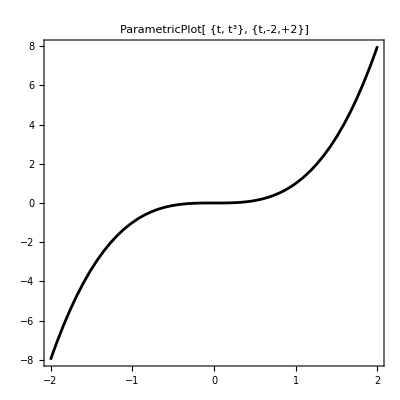

```mathematica
ParametricPlot[{t,t^3},{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {t, t^3}, {t,-2,+2}]"],16]]
```

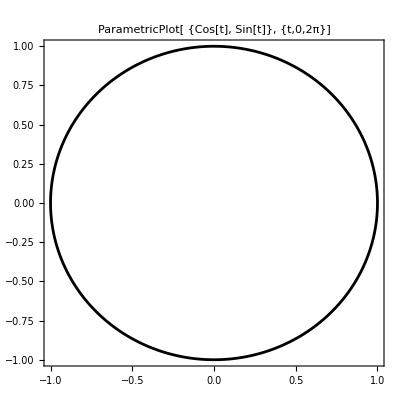

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {Cos[t], Sin[t]}, {t,0,2π}]"],16]]
```

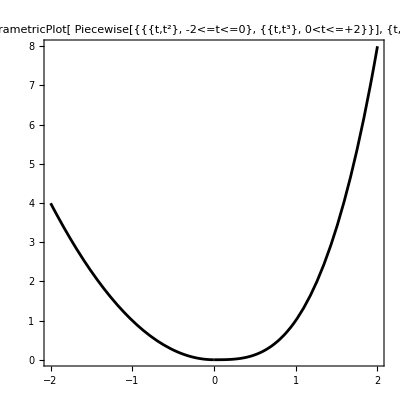

```mathematica
ParametricPlot[Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}], {t,-2,+2}]"],16]]
```

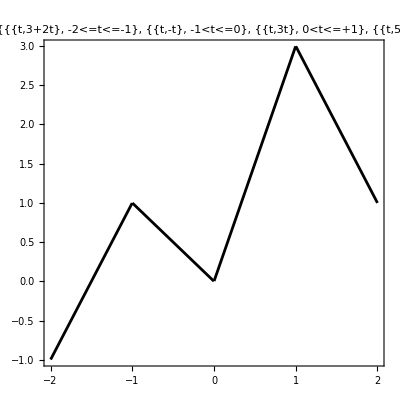

```mathematica
ParametricPlot[Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}], {t,-2,+2}]"],16]]
```

### 1.1.2 Path integrals

The scalar line integral of the function f along a curve C={r(u)∈ℝ^n,a≤u≤b} is given by:

-Graphics-"∮_C f(x)ⅆx=∫_a^b f(r(u)) Norm[r'(u)]ⅆu"

∫_a^b f(X_t) ⅆ X_t=∫_a^b f(X_t) ⅆt=∫_a^b f(X_t)dX_t/dt ⅆt

```mathematica
LineIntegrate[t^2,{x}∈ParametricRegion[{t^3},{{t,0,1}}]]
```

3/5

### 1.2.2 Examples

```mathematica
Table[nrsign[2,k],{k,1,12}]
```

{2,6,14,30,62,126,254,510,1022,2046,4094,8190}

```mathematica
nrsign[5,9]
```

2441405

```mathematica
Map[tensorfold,{{1},{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}}]
```

{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}}

```mathematica
Map[tensorfold[#,3]&,{{1},Range[3],Range[9],Range[27]}]
```

{{1},{1,2,3},{{1,2,3},{4,5,6},{7,8,9}},{{{1,2,3},{4,5,6},{7,8,9}},{{10,11,12},{13,14,15},{16,17,18}},{{19,20,21},{22,23,24},{25,26,27}}}}

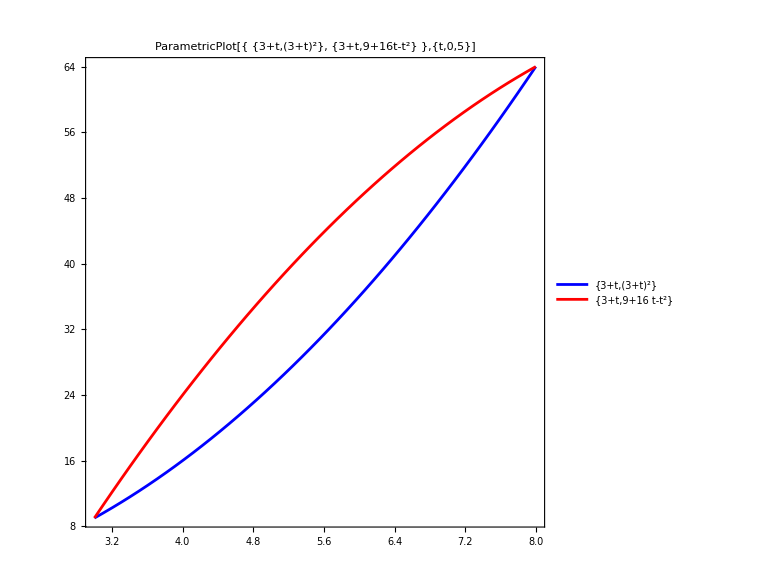

```mathematica
ParametricPlot[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{t,0,5},
Frame->True,AspectRatio->1,PlotLegends->"Expressions",
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
AxesOrigin->{3,9},PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"ParametricPlot[{
{3+t,(3+t)^2},
{3+t,9+16t-t^2}
},{t,0,5}]"],16]]
```

```mathematica
signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}]
```

{{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}},{{1},{5,55},{{25/2,350/3},{475/3,3025/2}},{{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}}}

### Sin

#### Plot and Signatures

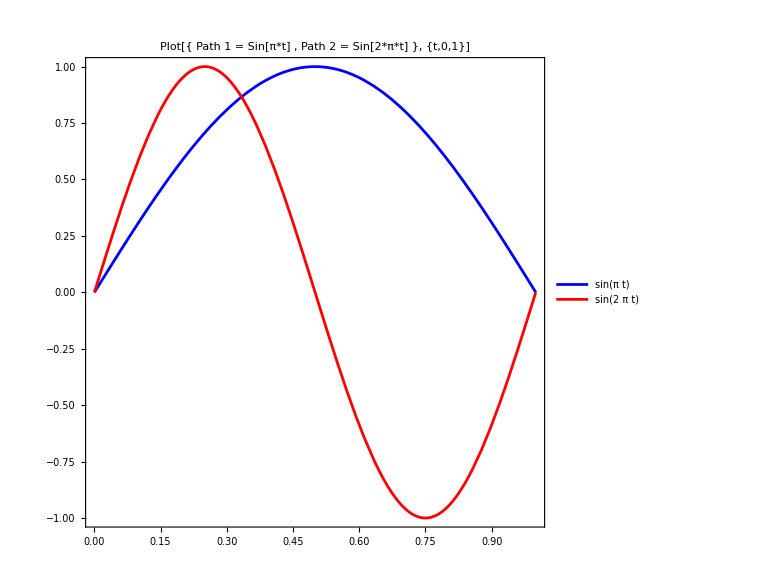

```mathematica
Plot[{Sin[π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π*t] ,
Path 2 = Sin[2*π*t] 
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins=signat[{{t,Sin[π t]},{t,Sin[2π t]}},{0,1},5];]
```

{124.057,Null}

```mathematica
{sigsins1f,sigsins2f}=sigsins;
```

```mathematica
sigsins1f
```

{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins2f
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}

```mathematica
getcore6[sigsins1f,5]
```

{{1,0},{-2/π},{-1/π,1/4},{-(-4+π^2)/(2 π^3),1/8,-2/(9 π)},{1/π^3-1/(6 π),1/48 (2-3/π^2),-1/12+7/(8 π^2),-1/(9 π),1/(12 π),1/64}}

```mathematica
getcore6[sigsins2f,5]
```

{{1,0},{0},{1/(2 π),1/4},{1/(4 π),1/8,0},{(-3+2 π^2)/(24 π^3),1/24-1/(64 π^2),-1/12+7/(32 π^2),1/(18 π),-7/(24 π),1/64}}

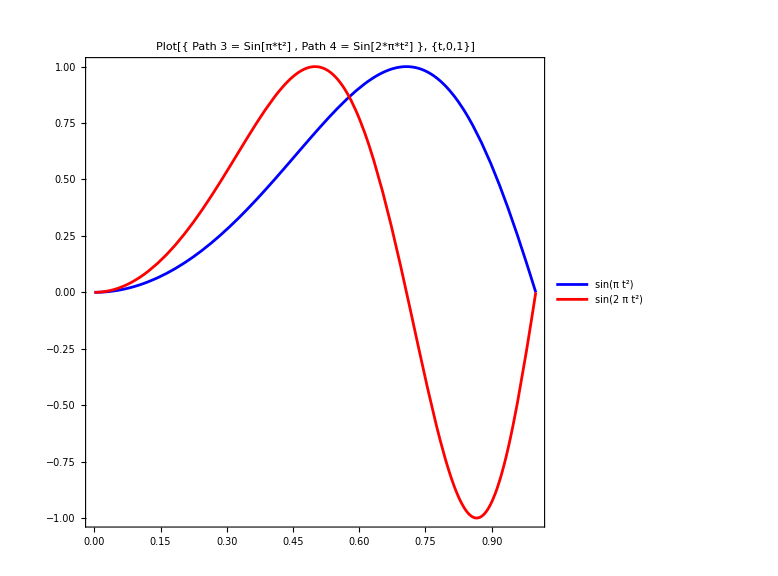

```mathematica
Plot[{Sin[π t^2],Sin[2π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 3 = Sin[π*t^2] ,
Path 4 = Sin[2*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins2=signat[{{t,Sin[π t^2]},{t,Sin[2π t^2]}},{0,1},5];]
```

{187.639,Null}

```mathematica
{sigsins1f2,sigsins2f2}={Append[Most[sigsins2[[1]]],N[Last[sigsins2[[1]]]]],Append[Most[sigsins2[[2]]],N[Last[sigsins2[[2]]]]]};
```

```mathematica
sigsins1f2
```

{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}},{{{{{0.00833333,-0.0265258},{-0.00323478,0.0433747}},{{0.00970435,-0.0200633},{0.0149393,-0.0353678}}},{{{0.0122565,-0.0393579},{-0.00371852,0.0546304}},{{0.0176846,-0.0470862},{0.010783,0.0114517}}}},{{{{0.00779975,-0.0273282},{-0.00609675,0.0514729}},{{0.00770722,-0.0150884},{0.0147373,-0.0458067}}},{{{0.0128588,-0.0439287},{-0.00719308,0.06871}},{{0.0170406,-0.0458067},{0.0114517,0.}}}}}}

```mathematica
sigsins2f2
```

{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}},{{{{{0.00833333,0.0132629},{-0.0229764,0.0423489}},{{-0.0106483,-0.0764914},{0.0744448,0.}}},{{{0.00855611,-0.024619},{-0.0330373,-0.0448062}},{{0.0377995,0.0990138},{-0.0707599,0.0126234}}}},{{{{0.0118056,0.0164127},{-0.0393608,0.0448062}},{{-0.0179426,-0.108415},{0.113266,-0.0504936}}},{{{0.0204454,0.00940129},{-0.0590584,0.0757405}},{{0.0165524,-0.0504936},{0.0126234,0.}}}}}}

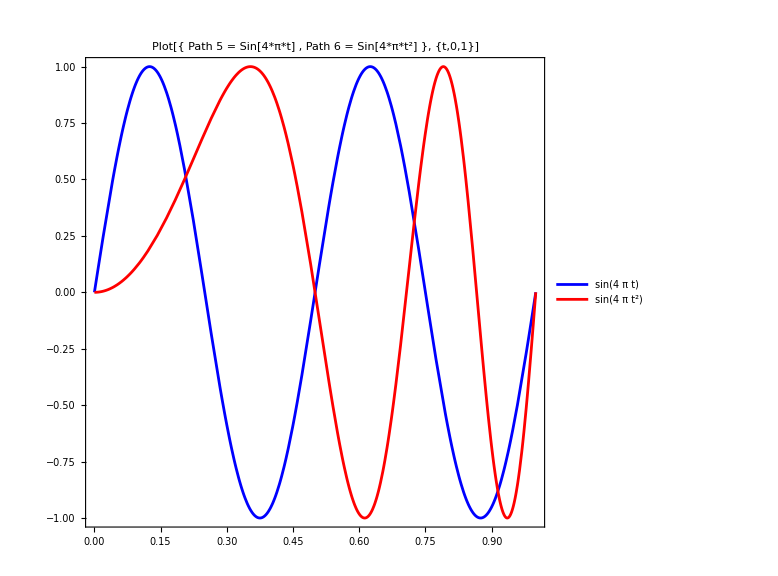

```mathematica
Plot[{Sin[4π t],Sin[4π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 5 = Sin[4*π*t] ,
Path 6 = Sin[4*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins42=signat[{{t,Sin[4π t]},{t,Sin[4π t^2]}},{0,1},4]]
```

{47.1755,{{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}},{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}}}

```mathematica
{sigsins1f42,sigsins2f42}=sigsins42;
```

```mathematica
Grid[{{sigsins1f[[2]]},{sigsins2f[[2]]},{sigsins1f2[[2]]},{sigsins2f2[[2]]},{sigsins1f42[[2]]},{sigsins2f42[[2]]}}]
```

{1,0}
{1,0}
{1,0}
{1,0}
{1,0}
{1,0}

```mathematica
Grid[{{sigsins1f[[3]]},{sigsins2f[[3]]},{sigsins1f2[[3]]},{sigsins2f2[[3]]},{sigsins1f42[[3]]},{sigsins2f42[[3]]}},Frame->All]
```

{{1/2,-2/π},{2/π,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}}
{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}}

```mathematica
Grid[Expand[{{sigsins1f[[4]]},{sigsins2f[[4]]},{sigsins1f2[[4]]},{sigsins2f2[[4]]},{sigsins1f42[[4]]},{sigsins2f42[[4]]}}],Frame->All]
```

{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}}
{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}}
{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/4-FresnelC[2]/8}},{{-1/π+FresnelS[√2]/(√2),-1/2+FresnelC[2]/4},{1/4-FresnelC[2]/8,0}}}
{{{1/6,0},{-FresnelS[2]/2,1/4-FresnelC[2 √2]/(8 √2)}},{{FresnelS[2]/2,-1/2+FresnelC[2 √2]/(4 √2)},{1/4-FresnelC[2 √2]/(8 √2),0}}}
{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}}
{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/4-FresnelC[4]/16}},{{FresnelS[2 √2]/(2 √2),-1/2+FresnelC[4]/8},{1/4-FresnelC[4]/16,0}}}

```mathematica
Grid[Expand[{{sigsins1f[[5]]},{sigsins2f[[5]]},{sigsins1f2[[5]]},{sigsins2f2[[5]]},{sigsins1f42[[5]]},{sigsins2f42[[5]]}}],Frame->All]
```

{{{{1/24,2/π^3-1/(2 π)},{-6/π^3+1/(2 π),1/8}},{{6/π^3-1/(2 π),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{-2/π^3+1/(2 π),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}
{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,-1/(4 π)-FresnelC[√2]/(4 √2 π)},{-1/(4 π)+(3 FresnelC[√2])/(4 √2 π),1/8}},{{5/(4 π)-(3 FresnelC[√2])/(4 √2 π)-FresnelS[√2]/(2 √2),-1/4+1/4 FresnelS[√2]^2},{1/4-FresnelC[2]/8-1/4 FresnelS[√2]^2,-FresnelS[√2]/(8 √2)+FresnelS[√6]/(24 √6)}}},{{{-3/(4 π)+FresnelC[√2]/(4 √2 π)+FresnelS[√2]/(2 √2),-1/4 FresnelS[√2]^2},{-1/4+FresnelC[2]/4+1/4 FresnelS[√2]^2,(3 FresnelS[√2])/(8 √2)-FresnelS[√6]/(8 √6)}},{{1/8-FresnelC[2]/8,-(3 FresnelS[√2])/(8 √2)+FresnelS[√6]/(8 √6)},{FresnelS[√2]/(8 √2)-FresnelS[√6]/(24 √6),0}}}}
{{{{1/24,1/(8 π)-FresnelC[2]/(16 π)},{-3/(8 π)+(3 FresnelC[2])/(16 π),1/8}},{{3/(8 π)-(3 FresnelC[2])/(16 π)-FresnelS[2]/4,-1/4+FresnelS[2]^2/8},{1/4-FresnelC[2 √2]/(8 √2)-FresnelS[2]^2/8,-FresnelS[2]/16+FresnelS[2 √3]/(48 √3)}}},{{{-1/(8 π)+FresnelC[2]/(16 π)+FresnelS[2]/4,-1/8 FresnelS[2]^2},{-1/4+FresnelC[2 √2]/(4 √2)+FresnelS[2]^2/8,(3 FresnelS[2])/16-FresnelS[2 √3]/(16 √3)}},{{1/8-FresnelC[2 √2]/(8 √2),-(3 FresnelS[2])/16+FresnelS[2 √3]/(16 √3)},{FresnelS[2]/16-FresnelS[2 √3]/(48 √3),0}}}}
{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,1/(16 π)-FresnelC[2 √2]/(32 √2 π)},{-3/(16 π)+(3 FresnelC[2 √2])/(32 √2 π),1/8}},{{3/(16 π)-(3 FresnelC[2 √2])/(32 √2 π)-FresnelS[2 √2]/(4 √2),-1/4+1/16 FresnelS[2 √2]^2},{1/4-FresnelC[4]/16-1/16 FresnelS[2 √2]^2,-FresnelS[2 √2]/(16 √2)+FresnelS[2 √6]/(48 √6)}}},{{{-1/(16 π)+FresnelC[2 √2]/(32 √2 π)+FresnelS[2 √2]/(4 √2),-1/16 FresnelS[2 √2]^2},{-1/4+FresnelC[4]/8+1/16 FresnelS[2 √2]^2,(3 FresnelS[2 √2])/(16 √2)-FresnelS[2 √6]/(16 √6)}},{{1/8-FresnelC[4]/16,-(3 FresnelS[2 √2])/(16 √2)+FresnelS[2 √6]/(16 √6)},{FresnelS[2 √2]/(16 √2)-FresnelS[2 √6]/(48 √6),0}}}}

```mathematica
Timing[sigline=signat[{{Subscript[a, 1]+Subscript[b, 1]*t,Subscript[a, 2]+Subscript[b, 2]*t}},{0,T},3]]
```

{0.002467,{{{1},{T b_1,T b_2},{{1/2 T^2 b_1^2,1/2 T^2 b_1 b_2},{1/2 T^2 b_1 b_2,1/2 T^2 b_2^2}},{{{1/6 T^3 b_1^3,1/6 T^3 b_1^2 b_2},{1/6 T^3 b_1^2 b_2,1/6 T^3 b_1 b_2^2}},{{1/6 T^3 b_1^2 b_2,1/6 T^3 b_1 b_2^2},{1/6 T^3 b_1 b_2^2,1/6 T^3 b_2^3}}}}}}

## Shuffle Product

### Typesetting

Enter ⧢

```mathematica
{1,2}⧢{a}={{a,1,2},{1,a,2},{1,2,a}}
```

### Functions

#### Much better shuffle product (Mathematica Stack Exchange)

```mathematica
shp[u:{a_,x___},v:{b_,y___},c___]:=Join[shp[{x},v,c,a],shp[u,{y},c,b]];
shp[{x___},{y___},c___]:={{c,x,y}} ;(*rule for empty-set termination*)
```

```mathematica
shp[{1,2},{3}]
```

{{1,2,3},{1,3,2},{3,1,2}}

```mathematica
shp[{1,2},{2,1}]
```

{{1,2,2,1},{1,2,2,1},{1,2,1,2},{2,1,2,1},{2,1,1,2},{2,1,1,2}}

```mathematica
shp[{2},{1,2}]
```

{{2,1,2},{1,2,2},{1,2,2}}

```mathematica
55 475/3
```

26125/3

```mathematica
7250/3+18875/6+18875/6
```

26125/3

```mathematica
Timing[Map[Length,
{shp[{a},{f}],
shp[{a,b},{f,g}],
shp[{a,b,c},{f,g,h}],
shp[{a,b,c,d},{f,g,h,i}],
shp[{a,b,c,d,e},{f,g,h,i,j}]}]]
```

{0.001594,{2,6,20,70,252}}

#### Subscript manipulation

```mathematica
inds[s_]:=Rest[Apply[List,s]];
```

```mathematica
sind[list_]:=Apply[Subscript,Prepend[list,s]];
```

#### Shuffle product identity

```mathematica
shuffles[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]==w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shuffles[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
shufflespol[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]-w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shufflespol[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{-s_1 s_(1,1)+3 s_(1,1,1),-s_1 s_(1,2)+2 s_(1,1,2)+s_(1,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_1 s_(2,2)+s_(1,2,2)+s_(2,1,2)+s_(2,2,1),-s_2 s_(1,1)+s_(1,1,2)+s_(1,2,1)+s_(2,1,1),-s_2 s_(1,2)+2 s_(1,2,2)+s_(2,1,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(2,2)+3 s_(2,2,2)}

## Concatenation of Signatures (Chen)

### Exploring

```mathematica
vind[list_,var_:s]:=Apply[Subscript,Prepend[list,var]];
```

```mathematica
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]]
```

{x_(1,1),x_(1,2),x_(2,1),x_(2,2)}

```mathematica
Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},y],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{y_(1,1,1),y_(1,1,2)},{y_(1,2,1),y_(1,2,2)}},{{y_(2,1,1),y_(2,1,2)},{y_(2,2,1),y_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},x],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{x_(1,1,1,1),x_(1,1,1,2)},{x_(1,1,2,1),x_(1,1,2,2)}},{{x_(1,2,1,1),x_(1,2,1,2)},{x_(1,2,2,1),x_(1,2,2,2)}}},{{{x_(2,1,1,1),x_(2,1,1,2)},{x_(2,1,2,1),x_(2,1,2,2)}},{{x_(2,2,1,1),x_(2,2,1,2)},{x_(2,2,2,1),x_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},y],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{y_(1,1,1,1),y_(1,1,1,2)},{y_(1,1,2,1),y_(1,1,2,2)}},{{y_(1,2,1,1),y_(1,2,1,2)},{y_(1,2,2,1),y_(1,2,2,2)}}},{{{y_(2,1,1,1),y_(2,1,1,2)},{y_(2,1,2,1),y_(2,1,2,2)}},{{y_(2,2,1,1),y_(2,2,1,2)},{y_(2,2,2,1),y_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{x_1 y_1,x_1 y_2},{x_2 y_1,x_2 y_2}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{{y_1 x_(1,1),y_2 x_(1,1)},{y_1 x_(1,2),y_2 x_(1,2)}},{{y_1 x_(2,1),y_2 x_(2,1)},{y_1 x_(2,2),y_2 x_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{x_1 y_(1,1),x_1 y_(1,2)},{x_1 y_(2,1),x_1 y_(2,2)}},{{x_2 y_(1,1),x_2 y_(1,2)},{x_2 y_(2,1),x_2 y_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{{x_(1,1) y_(1,1),x_(1,1) y_(1,2)},{x_(1,1) y_(2,1),x_(1,1) y_(2,2)}},{{x_(1,2) y_(1,1),x_(1,2) y_(1,2)},{x_(1,2) y_(2,1),x_(1,2) y_(2,2)}}},{{{x_(2,1) y_(1,1),x_(2,1) y_(1,2)},{x_(2,1) y_(2,1),x_(2,1) y_(2,2)}},{{x_(2,2) y_(1,1),x_(2,2) y_(1,2)},{x_(2,2) y_(2,1),x_(2,2) y_(2,2)}}}}

### Functions

```mathematica
sigchen[sig1_,sig2_,levelout_:4,dim_:2]:=
Take[
Table[tensorfold[Sum[Flatten[TensorProduct[sig1[[k]],sig2[[j+1-k]]]],
{k,1,j}],dim],{j,1,Length[sig1]}]
,levelout+1];
```

```mathematica
chainchen[sigs_,levelout_:4,dim_:2]:=
Fold[sigchen[#1,#2,levelout,dim]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chainchenN[sigs_,levelout_:4,dim_:2]:=
Fold[sigchen[#1,#2,levelout,dim]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chen2[sig1_,sig2_,index_]:=Module[{level,parts},
level=Length[index];
(*parts=Table[{sigtake[sig1,Take[index,j]],sigtake[sig2,Drop[index,j]]},{j,0,level}];*)
Sum[sigtake[sig1,Take[index,j]]*sigtake[sig2,Drop[index,j]],{j,0,level}]];
```

### Examples

```mathematica
dinv=3;
```

```mathematica
sigx4={{{1}},
Table[{vind[{i},x]},{i,1,dinv}],
tensorfold[Flatten[Table[vind[{i,j},x],{i,1,dinv},{j,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k},x],{i,1,dinv},{j,1,dinv},{k,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k,l},x],{i,1,dinv},{j,1,dinv},{k,1,dinv},{l,1,dinv}]],dinv]};
```

```mathematica
sigy4={{{1}},
Table[{vind[{i},y]},{i,1,dinv}],
tensorfold[Flatten[Table[vind[{i,j},y],{i,1,dinv},{j,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k},y],{i,1,dinv},{j,1,dinv},{k,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k,l},y],{i,1,dinv},{j,1,dinv},{k,1,dinv},{l,1,dinv}]],dinv]};
```

```mathematica
chenz4=sigchen[sigx4,sigy4,4,dinv]
```

{{1},{x_1+y_1,x_2+y_2,x_3+y_3},{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2),x_1 y_3+x_(1,3)+y_(1,3)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2),x_2 y_3+x_(2,3)+y_(2,3)},{x_3 y_1+x_(3,1)+y_(3,1),x_3 y_2+x_(3,2)+y_(3,2),x_3 y_3+x_(3,3)+y_(3,3)}},{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2),y_3 x_(1,1)+x_1 y_(1,3)+x_(1,1,3)+y_(1,1,3)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2),y_3 x_(1,2)+x_1 y_(2,3)+x_(1,2,3)+y_(1,2,3)},{y_1 x_(1,3)+x_1 y_(3,1)+x_(1,3,1)+y_(1,3,1),y_2 x_(1,3)+x_1 y_(3,2)+x_(1,3,2)+y_(1,3,2),y_3 x_(1,3)+x_1 y_(3,3)+x_(1,3,3)+y_(1,3,3)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2),y_3 x_(2,1)+x_2 y_(1,3)+x_(2,1,3)+y_(2,1,3)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2),y_3 x_(2,2)+x_2 y_(2,3)+x_(2,2,3)+y_(2,2,3)},{y_1 x_(2,3)+x_2 y_(3,1)+x_(2,3,1)+y_(2,3,1),y_2 x_(2,3)+x_2 y_(3,2)+x_(2,3,2)+y_(2,3,2),y_3 x_(2,3)+x_2 y_(3,3)+x_(2,3,3)+y_(2,3,3)}},{{y_1 x_(3,1)+x_3 y_(1,1)+x_(3,1,1)+y_(3,1,1),y_2 x_(3,1)+x_3 y_(1,2)+x_(3,1,2)+y_(3,1,2),y_3 x_(3,1)+x_3 y_(1,3)+x_(3,1,3)+y_(3,1,3)},{y_1 x_(3,2)+x_3 y_(2,1)+x_(3,2,1)+y_(3,2,1),y_2 x_(3,2)+x_3 y_(2,2)+x_(3,2,2)+y_(3,2,2),y_3 x_(3,2)+x_3 y_(2,3)+x_(3,2,3)+y_(3,2,3)},{y_1 x_(3,3)+x_3 y_(3,1)+x_(3,3,1)+y_(3,3,1),y_2 x_(3,3)+x_3 y_(3,2)+x_(3,3,2)+y_(3,3,2),y_3 x_(3,3)+x_3 y_(3,3)+x_(3,3,3)+y_(3,3,3)}}},{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2),x_(1,1) y_(1,3)+y_3 x_(1,1,1)+x_1 y_(1,1,3)+x_(1,1,1,3)+y_(1,1,1,3)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2),x_(1,1) y_(2,3)+y_3 x_(1,1,2)+x_1 y_(1,2,3)+x_(1,1,2,3)+y_(1,1,2,3)},{x_(1,1) y_(3,1)+y_1 x_(1,1,3)+x_1 y_(1,3,1)+x_(1,1,3,1)+y_(1,1,3,1),x_(1,1) y_(3,2)+y_2 x_(1,1,3)+x_1 y_(1,3,2)+x_(1,1,3,2)+y_(1,1,3,2),x_(1,1) y_(3,3)+y_3 x_(1,1,3)+x_1 y_(1,3,3)+x_(1,1,3,3)+y_(1,1,3,3)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2),x_(1,2) y_(1,3)+y_3 x_(1,2,1)+x_1 y_(2,1,3)+x_(1,2,1,3)+y_(1,2,1,3)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2),x_(1,2) y_(2,3)+y_3 x_(1,2,2)+x_1 y_(2,2,3)+x_(1,2,2,3)+y_(1,2,2,3)},{x_(1,2) y_(3,1)+y_1 x_(1,2,3)+x_1 y_(2,3,1)+x_(1,2,3,1)+y_(1,2,3,1),x_(1,2) y_(3,2)+y_2 x_(1,2,3)+x_1 y_(2,3,2)+x_(1,2,3,2)+y_(1,2,3,2),x_(1,2) y_(3,3)+y_3 x_(1,2,3)+x_1 y_(2,3,3)+x_(1,2,3,3)+y_(1,2,3,3)}},{{x_(1,3) y_(1,1)+y_1 x_(1,3,1)+x_1 y_(3,1,1)+x_(1,3,1,1)+y_(1,3,1,1),x_(1,3) y_(1,2)+y_2 x_(1,3,1)+x_1 y_(3,1,2)+x_(1,3,1,2)+y_(1,3,1,2),x_(1,3) y_(1,3)+y_3 x_(1,3,1)+x_1 y_(3,1,3)+x_(1,3,1,3)+y_(1,3,1,3)},{x_(1,3) y_(2,1)+y_1 x_(1,3,2)+x_1 y_(3,2,1)+x_(1,3,2,1)+y_(1,3,2,1),x_(1,3) y_(2,2)+y_2 x_(1,3,2)+x_1 y_(3,2,2)+x_(1,3,2,2)+y_(1,3,2,2),x_(1,3) y_(2,3)+y_3 x_(1,3,2)+x_1 y_(3,2,3)+x_(1,3,2,3)+y_(1,3,2,3)},{x_(1,3) y_(3,1)+y_1 x_(1,3,3)+x_1 y_(3,3,1)+x_(1,3,3,1)+y_(1,3,3,1),x_(1,3) y_(3,2)+y_2 x_(1,3,3)+x_1 y_(3,3,2)+x_(1,3,3,2)+y_(1,3,3,2),x_(1,3) y_(3,3)+y_3 x_(1,3,3)+x_1 y_(3,3,3)+x_(1,3,3,3)+y_(1,3,3,3)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2),x_(2,1) y_(1,3)+y_3 x_(2,1,1)+x_2 y_(1,1,3)+x_(2,1,1,3)+y_(2,1,1,3)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2),x_(2,1) y_(2,3)+y_3 x_(2,1,2)+x_2 y_(1,2,3)+x_(2,1,2,3)+y_(2,1,2,3)},{x_(2,1) y_(3,1)+y_1 x_(2,1,3)+x_2 y_(1,3,1)+x_(2,1,3,1)+y_(2,1,3,1),x_(2,1) y_(3,2)+y_2 x_(2,1,3)+x_2 y_(1,3,2)+x_(2,1,3,2)+y_(2,1,3,2),x_(2,1) y_(3,3)+y_3 x_(2,1,3)+x_2 y_(1,3,3)+x_(2,1,3,3)+y_(2,1,3,3)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2),x_(2,2) y_(1,3)+y_3 x_(2,2,1)+x_2 y_(2,1,3)+x_(2,2,1,3)+y_(2,2,1,3)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2),x_(2,2) y_(2,3)+y_3 x_(2,2,2)+x_2 y_(2,2,3)+x_(2,2,2,3)+y_(2,2,2,3)},{x_(2,2) y_(3,1)+y_1 x_(2,2,3)+x_2 y_(2,3,1)+x_(2,2,3,1)+y_(2,2,3,1),x_(2,2) y_(3,2)+y_2 x_(2,2,3)+x_2 y_(2,3,2)+x_(2,2,3,2)+y_(2,2,3,2),x_(2,2) y_(3,3)+y_3 x_(2,2,3)+x_2 y_(2,3,3)+x_(2,2,3,3)+y_(2,2,3,3)}},{{x_(2,3) y_(1,1)+y_1 x_(2,3,1)+x_2 y_(3,1,1)+x_(2,3,1,1)+y_(2,3,1,1),x_(2,3) y_(1,2)+y_2 x_(2,3,1)+x_2 y_(3,1,2)+x_(2,3,1,2)+y_(2,3,1,2),x_(2,3) y_(1,3)+y_3 x_(2,3,1)+x_2 y_(3,1,3)+x_(2,3,1,3)+y_(2,3,1,3)},{x_(2,3) y_(2,1)+y_1 x_(2,3,2)+x_2 y_(3,2,1)+x_(2,3,2,1)+y_(2,3,2,1),x_(2,3) y_(2,2)+y_2 x_(2,3,2)+x_2 y_(3,2,2)+x_(2,3,2,2)+y_(2,3,2,2),x_(2,3) y_(2,3)+y_3 x_(2,3,2)+x_2 y_(3,2,3)+x_(2,3,2,3)+y_(2,3,2,3)},{x_(2,3) y_(3,1)+y_1 x_(2,3,3)+x_2 y_(3,3,1)+x_(2,3,3,1)+y_(2,3,3,1),x_(2,3) y_(3,2)+y_2 x_(2,3,3)+x_2 y_(3,3,2)+x_(2,3,3,2)+y_(2,3,3,2),x_(2,3) y_(3,3)+y_3 x_(2,3,3)+x_2 y_(3,3,3)+x_(2,3,3,3)+y_(2,3,3,3)}}},{{{x_(3,1) y_(1,1)+y_1 x_(3,1,1)+x_3 y_(1,1,1)+x_(3,1,1,1)+y_(3,1,1,1),x_(3,1) y_(1,2)+y_2 x_(3,1,1)+x_3 y_(1,1,2)+x_(3,1,1,2)+y_(3,1,1,2),x_(3,1) y_(1,3)+y_3 x_(3,1,1)+x_3 y_(1,1,3)+x_(3,1,1,3)+y_(3,1,1,3)},{x_(3,1) y_(2,1)+y_1 x_(3,1,2)+x_3 y_(1,2,1)+x_(3,1,2,1)+y_(3,1,2,1),x_(3,1) y_(2,2)+y_2 x_(3,1,2)+x_3 y_(1,2,2)+x_(3,1,2,2)+y_(3,1,2,2),x_(3,1) y_(2,3)+y_3 x_(3,1,2)+x_3 y_(1,2,3)+x_(3,1,2,3)+y_(3,1,2,3)},{x_(3,1) y_(3,1)+y_1 x_(3,1,3)+x_3 y_(1,3,1)+x_(3,1,3,1)+y_(3,1,3,1),x_(3,1) y_(3,2)+y_2 x_(3,1,3)+x_3 y_(1,3,2)+x_(3,1,3,2)+y_(3,1,3,2),x_(3,1) y_(3,3)+y_3 x_(3,1,3)+x_3 y_(1,3,3)+x_(3,1,3,3)+y_(3,1,3,3)}},{{x_(3,2) y_(1,1)+y_1 x_(3,2,1)+x_3 y_(2,1,1)+x_(3,2,1,1)+y_(3,2,1,1),x_(3,2) y_(1,2)+y_2 x_(3,2,1)+x_3 y_(2,1,2)+x_(3,2,1,2)+y_(3,2,1,2),x_(3,2) y_(1,3)+y_3 x_(3,2,1)+x_3 y_(2,1,3)+x_(3,2,1,3)+y_(3,2,1,3)},{x_(3,2) y_(2,1)+y_1 x_(3,2,2)+x_3 y_(2,2,1)+x_(3,2,2,1)+y_(3,2,2,1),x_(3,2) y_(2,2)+y_2 x_(3,2,2)+x_3 y_(2,2,2)+x_(3,2,2,2)+y_(3,2,2,2),x_(3,2) y_(2,3)+y_3 x_(3,2,2)+x_3 y_(2,2,3)+x_(3,2,2,3)+y_(3,2,2,3)},{x_(3,2) y_(3,1)+y_1 x_(3,2,3)+x_3 y_(2,3,1)+x_(3,2,3,1)+y_(3,2,3,1),x_(3,2) y_(3,2)+y_2 x_(3,2,3)+x_3 y_(2,3,2)+x_(3,2,3,2)+y_(3,2,3,2),x_(3,2) y_(3,3)+y_3 x_(3,2,3)+x_3 y_(2,3,3)+x_(3,2,3,3)+y_(3,2,3,3)}},{{x_(3,3) y_(1,1)+y_1 x_(3,3,1)+x_3 y_(3,1,1)+x_(3,3,1,1)+y_(3,3,1,1),x_(3,3) y_(1,2)+y_2 x_(3,3,1)+x_3 y_(3,1,2)+x_(3,3,1,2)+y_(3,3,1,2),x_(3,3) y_(1,3)+y_3 x_(3,3,1)+x_3 y_(3,1,3)+x_(3,3,1,3)+y_(3,3,1,3)},{x_(3,3) y_(2,1)+y_1 x_(3,3,2)+x_3 y_(3,2,1)+x_(3,3,2,1)+y_(3,3,2,1),x_(3,3) y_(2,2)+y_2 x_(3,3,2)+x_3 y_(3,2,2)+x_(3,3,2,2)+y_(3,3,2,2),x_(3,3) y_(2,3)+y_3 x_(3,3,2)+x_3 y_(3,2,3)+x_(3,3,2,3)+y_(3,3,2,3)},{x_(3,3) y_(3,1)+y_1 x_(3,3,3)+x_3 y_(3,3,1)+x_(3,3,3,1)+y_(3,3,3,1),x_(3,3) y_(3,2)+y_2 x_(3,3,3)+x_3 y_(3,3,2)+x_(3,3,3,2)+y_(3,3,3,2),x_(3,3) y_(3,3)+y_3 x_(3,3,3)+x_3 y_(3,3,3)+x_(3,3,3,3)+y_(3,3,3,3)}}}}}

```mathematica
z3=sigchen[
{{{1}},{{Subscript[x, 1]},{Subscript[x, 2]}},{{Subscript[x, 1,1],Subscript[x, 1,2]},{Subscript[x, 2,1],Subscript[x, 2,2]}},{{{Subscript[x, 1,1,1],Subscript[x, 1,1,2]},{Subscript[x, 1,2,1],Subscript[x, 1,2,2]}},{{Subscript[x, 2,1,1],Subscript[x, 2,1,2]},{Subscript[x, 2,2,1],Subscript[x, 2,2,2]}}},
{{{{Subscript[x, 1,1,1,1],Subscript[x, 1,1,1,2]},{Subscript[x, 1,1,2,1],Subscript[x, 1,1,2,2]}},{{Subscript[x, 1,2,1,1],Subscript[x, 1,2,1,2]},{Subscript[x, 1,2,2,1],Subscript[x, 1,2,2,2]}}},{{{Subscript[x, 2,1,1,1],Subscript[x, 2,1,1,2]},{Subscript[x, 2,1,2,1],Subscript[x, 2,1,2,2]}},{{Subscript[x, 2,2,1,1],Subscript[x, 2,2,1,2]},{Subscript[x, 2,2,2,1],Subscript[x, 2,2,2,2]}}}}},
{{{1}},{{Subscript[y, 1]},{Subscript[y, 2]}},{{Subscript[y, 1,1],Subscript[y, 1,2]},{Subscript[y, 2,1],Subscript[y, 2,2]}},
{{{Subscript[y, 1,1,1],Subscript[y, 1,1,2]},{Subscript[y, 1,2,1],Subscript[y, 1,2,2]}},{{Subscript[y, 2,1,1],Subscript[y, 2,1,2]},{Subscript[y, 2,2,1],Subscript[y, 2,2,2]}}},
{{{{Subscript[y, 1,1,1,1],Subscript[y, 1,1,1,2]},{Subscript[y, 1,1,2,1],Subscript[y, 1,1,2,2]}},{{Subscript[y, 1,2,1,1],Subscript[y, 1,2,1,2]},{Subscript[y, 1,2,2,1],Subscript[y, 1,2,2,2]}}},{{{Subscript[y, 2,1,1,1],Subscript[y, 2,1,1,2]},{Subscript[y, 2,1,2,1],Subscript[y, 2,1,2,2]}},{{Subscript[y, 2,2,1,1],Subscript[y, 2,2,1,2]},{Subscript[y, 2,2,2,1],Subscript[y, 2,2,2,2]}}}}},4]
```

{{1},{x_1+y_1,x_2+y_2},{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}},{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}},{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}}

```mathematica
z3[[2]]
```

{x_1+y_1,x_2+y_2}

```mathematica
z3[[3]]
```

{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}}

```mathematica
z3[[4]]
```

{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}}

```mathematica
z3[[5]]
```

{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}

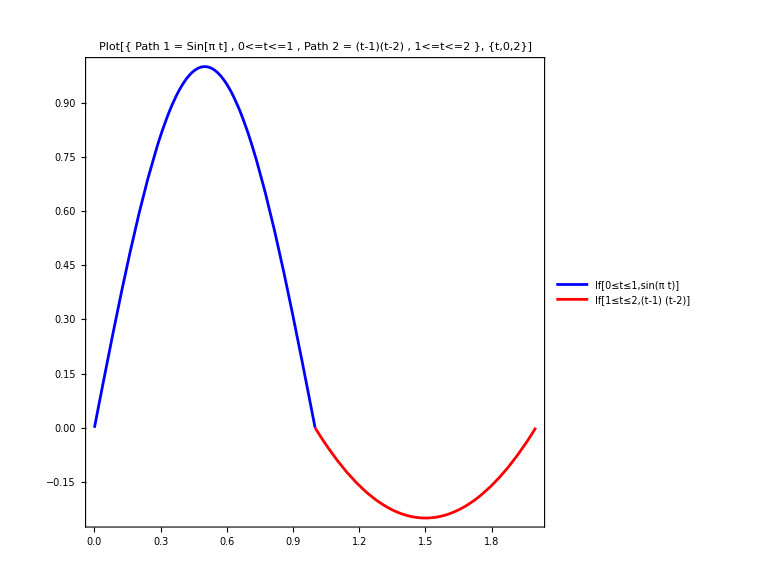

```mathematica
Plot[{If[0<=t<=1,Sin[π t]],If[1<=t<=2,(t-1)(t-2)]},{t,0,2},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π t] , 0<=t<=1 ,
Path 2 = (t-1)(t-2) , 1<=t<=2
}, {t,0,2}]"],16]]
```

```mathematica
Timing[spath01=signat[{{t,Sin[π t]}},{0,1},5][[1]]]
```

{67.9748,{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}}

```mathematica
Timing[spath12=signat[{{t,(t-1)(t-2)}},{1,2},5][[1]]]
```

{73.3911,{{1},{1,0},{{1/2,1/6},{-1/6,0}},{{{1/6,1/12},{0,1/60}},{{-1/12,-1/30},{1/60,0}}},{{{{1/24,1/40},{1/120,1/120}},{{-1/120,-1/360},{1/360,1/840}}},{{{-1/40,-1/72},{-1/360,-1/280}},{{1/120,1/280},{-1/840,0}}}},{{{{{1/120,1/180},{1/360,1/420}},{{0,1/2520},{1/1260,1/1680}}},{{{-1/360,-1/630},{-1/2520,-1/2520}},{{1/1260,1/2520},{0,1/15120}}}},{{{{-1/180,-1/280},{-1/630,-1/720}},{{1/2520,0},{-1/2520,-1/3780}}},{{{1/420,1/720},{1/2520,1/2520}},{{-1/1680,-1/3780},{1/15120,0}}}}}}}

```mathematica
Timing[spath02=signat[{{t,Piecewise[{{Sin[π t], 0<=t<=1}, {(t-1)(t-2), 1<=t<=2}}]}},{0,2},5][[1]]]
```

{207.914,{{1},{2,0},{{2,(-12+π)/(6 π)},{(12-π)/(6 π),0}},{{{4/3,(-4+π)/(4 π)},{(-12-π)/(6 π),4/15}},{{(36-π)/(12 π),-8/15},{4/15,0}}},{{{{2/3,(240-60 π^2+23 π^3)/(120 π^3)},{(-240-20 π^2-3 π^3)/(40 π^3),3/20}},{{(720-180 π^2-11 π^3)/(120 π^3),(720-120 π-103 π^2)/(360 π^2)},{(-720+120 π+187 π^2)/(360 π^2),(-560+3 π)/(2520 π)}}},{{{(-80+100 π^2-π^3)/(40 π^3),(-144+24 π-π^2)/(72 π^2)},{(720-120 π-271 π^2)/(360 π^2),(560-3 π)/(840 π)}},{{23/60,(-560+3 π)/(840 π)},{(560-3 π)/(2520 π),0}}}},{{{{{4/15,(30-5 π^2+3 π^3)/(30 π^3)},{(-20-π)/(60 π),(-35+34 π^2)/(560 π^2)}},{{(-120-π^3)/(20 π^3),(735-140 π-86 π^2)/(840 π^2)},{(-231+56 π+74 π^2)/(336 π^2),(-560+9 π)/(5040 π)}}},{{{(288-36 π^2-π^3)/(36 π^3),(-210-140 π-13 π^2)/(840 π^2)},{(3465-424 π^2)/(1260 π^2),(63-5 π)/(1260 π)}},{{(-13545+840 π+2356 π^2)/(5040 π^2),(-42+115 π)/(2520 π)},{(-161-27 π)/(630 π),949/60480}}}},{{{{(-540+270 π^2-π^3)/(180 π^3),(-420+280 π-3 π^2)/(840 π^2)},{(-2835-210 π-2 π^2)/(1260 π^2),(204-π)/(720 π)}},{{(7245-420 π-1469 π^2)/(2520 π^2),(-4-5 π)/(60 π)},{(1974+209 π)/(2520 π),-949/15120}}},{{{(-105+494 π^2)/(1680 π^2),(-180+31 π)/(720 π)},{(-945-52 π)/(1260 π),949/10080}},{{(560-π)/(1680 π),-949/15120},{949/60480,0}}}}}}}

```mathematica
sigtake[spath01,{1,1,2}]
```

-1/π

```mathematica
sigtake[spath01,{}]
```

1

```mathematica
FullSimplify[{chen2[spath01,spath12,{1,1,2}],sigtake[spath02,{1,1,2}]}]
```

{1/4-1/π,1/4-1/π}

```mathematica
Expand[{chen2[spath01,spath12,{2,1,1,2}],sigtake[spath02,{2,1,1,2}]}]
```

{-1/72-2/π^2+1/(3 π),-1/72-2/π^2+1/(3 π)}

## Solving the sparse linear systems

### Functions

```mathematica
netgroebner[pols_,vars_,method_:"Buchberger"]:=Module[{basis,basisv},
basis=GroebnerBasis[pols,vars,Method->method];
basisv=Map[(Length[Intersection[vars,Variables[#]]]>0)&,basis];
Pick[basis,basisv]];
```

```mathematica
pickvars[pol_,level_]:=Module[{polvars,mask},
polvars=Variables[pol];
mask=Map[(Length[inds[#]]==level)&,polvars];
Pick[polvars,mask]];
```

```mathematica
graphgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
graphgroebner2[vars_,level_,grbasis_]:=Module[{pairs},
pairs=Select[Map[pickvars[#,level]&,grbasis],(Length[#]==2)&];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
adjgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
AdjacencyMatrix[Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name"]]];
```

### d=2

#### Level 1

```mathematica
vars1=Flatten[Table[sind[{i}],{i,1,2}]]
```

{s_1,s_2}

```mathematica
fund1=vars1
```

{s_1,s_2}

#### Level 2

```mathematica
vars2=Flatten[Table[sind[{i,j}],{i,1,2},{j,1,2}]]
```

{s_(1,1),s_(1,2),s_(2,1),s_(2,2)}

```mathematica
eqs2=shuffles[vars1,vars1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2}

```mathematica
Transpose[{eqs2}]
```

{{2 s_(1,1)==s_1^2},{s_(1,2)+s_(2,1)==s_1 s_2},{s_(1,2)+s_(2,1)==s_1 s_2},{2 s_(2,2)==s_2^2}}

```mathematica
TableForm[netgroebner[shufflespol[vars1,vars1],vars2]]
```

-s_2^2+2 s_(2,2)
-s_1 s_2+s_(1,2)+s_(2,1)
-s_1^2+2 s_(1,1)

```mathematica
sols2=First[Solve[eqs2,vars2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2}

```mathematica
Transpose[{sols2}]
```

{{s_(1,1)→s_1^2/2},{s_(2,1)→s_1 s_2-s_(1,2)},{s_(2,2)→s_2^2/2}}

```mathematica
fund2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols2]]]
```

{s_1,s_2,s_(1,2)}

#### Level 3

```mathematica
vars3=Flatten[Table[sind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]]
```

{s_(1,1,1),s_(1,1,2),s_(1,2,1),s_(1,2,2),s_(2,1,1),s_(2,1,2),s_(2,2,1),s_(2,2,2)}

```mathematica
eqs3=shuffles[vars1,vars2]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
Transpose[{eqs3}]
```

{{3 s_(1,1,1)==s_1 s_(1,1)},{2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2)},{s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1)},{s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2)},{s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1)},{2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2)},{s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1)},{3 s_(2,2,2)==s_2 s_(2,2)}}

```mathematica
Length[eqs3]
```

8

```mathematica
Timing[netgroebner[shufflespol[vars1,vars2],vars3,"GroebnerWalk"]]
```

{0.086945,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
Timing[ngb3=netgroebner[shufflespol[vars1,vars2],vars3,"Buchberger"]]
```

{0.007345,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
TableForm[ngb3]
```

-s_2 s_(2,2)+3 s_(2,2,2)
-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1)
-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1)
-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1)
-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1)
-s_1 s_(1,1)+3 s_(1,1,1)

```mathematica
Map[pickvars[#,3]&,ngb3]
```

{{s_(2,2,2)},{s_(2,1,2),s_(2,2,1)},{s_(1,2,2),s_(2,2,1)},{s_(1,2,1),s_(2,1,1)},{s_(1,1,2),s_(2,1,1)},{s_(1,1,1)}}

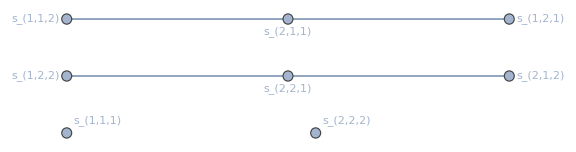

```mathematica
graphgroebner[vars3,3,ngb3]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars3,3,ngb3]]]
```

{3,3,1,1}

```mathematica
shp[{1,1},{2}]
```

{{1,1,2},{1,2,1},{2,1,1}}

```mathematica
shp[{1},{2,2}]
```

{{1,2,2},{2,1,2},{2,2,1}}

```mathematica
sols3new=First[Solve[eqs3/.sols2,vars3]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1,1)→s_1^3/6,s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2),s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2),s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2),s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2),s_(2,2,2)→s_2^3/6}

```mathematica
Transpose[{sols3new}]
```

{{s_(1,1,1)→s_1^3/6},{s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2)},{s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2)},{s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2)},{s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2)},{s_(2,2,2)→s_2^3/6}}

```mathematica
sols3=Join[sols2,sols3new];
```

```mathematica
fund3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2)}

#### Level 4

```mathematica
vars4=Flatten[Table[sind[{i,j,k,l}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
```

```mathematica
eqs4s13=shuffles[vars1,vars3];
```

```mathematica
sols4news13=First[Solve[eqs4s13/.sols3,vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news13]
```

12

```mathematica
eqs4s22=shuffles[vars2,vars2];
```

```mathematica
Length[Join[eqs4s13,eqs4s22]]
```

32

```mathematica
Timing[ngb4=netgroebner[Join[shufflespol[vars1,vars3],shufflespol[vars2,vars2]],vars4]]
```

{0.03109,{-s_(2,2)^2+6 s_(2,2,2,2),-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1),-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1),-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1),s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2),-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1),s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1),-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1),-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1),-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1),-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1),-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1),-s_(1,1)^2+6 s_(1,1,1,1)}}

```mathematica
TableForm[ngb4]
```

-s_(2,2)^2+6 s_(2,2,2,2)
-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1)
-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1)
-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1)
s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2)
-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1)
s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1)
-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1)
-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1)
-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1)
-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1)
-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1)
-s_(1,1)^2+6 s_(1,1,1,1)

```mathematica
Length[ngb4]
```

13

```mathematica
Map[pickvars[#,4]&,ngb4]
```

{{s_(2,2,2,2)},{s_(2,2,1,2),s_(2,2,2,1)},{s_(2,1,2,2),s_(2,2,2,1)},{s_(2,1,2,1),s_(2,2,1,1)},{s_(2,1,1,2)},{s_(1,2,2,2),s_(2,2,2,1)},{s_(1,2,2,1)},{s_(1,2,1,2),s_(2,2,1,1)},{s_(1,2,1,1),s_(2,1,1,1)},{s_(1,1,2,2),s_(2,2,1,1)},{s_(1,1,2,1),s_(2,1,1,1)},{s_(1,1,1,2),s_(2,1,1,1)},{s_(1,1,1,1)}}

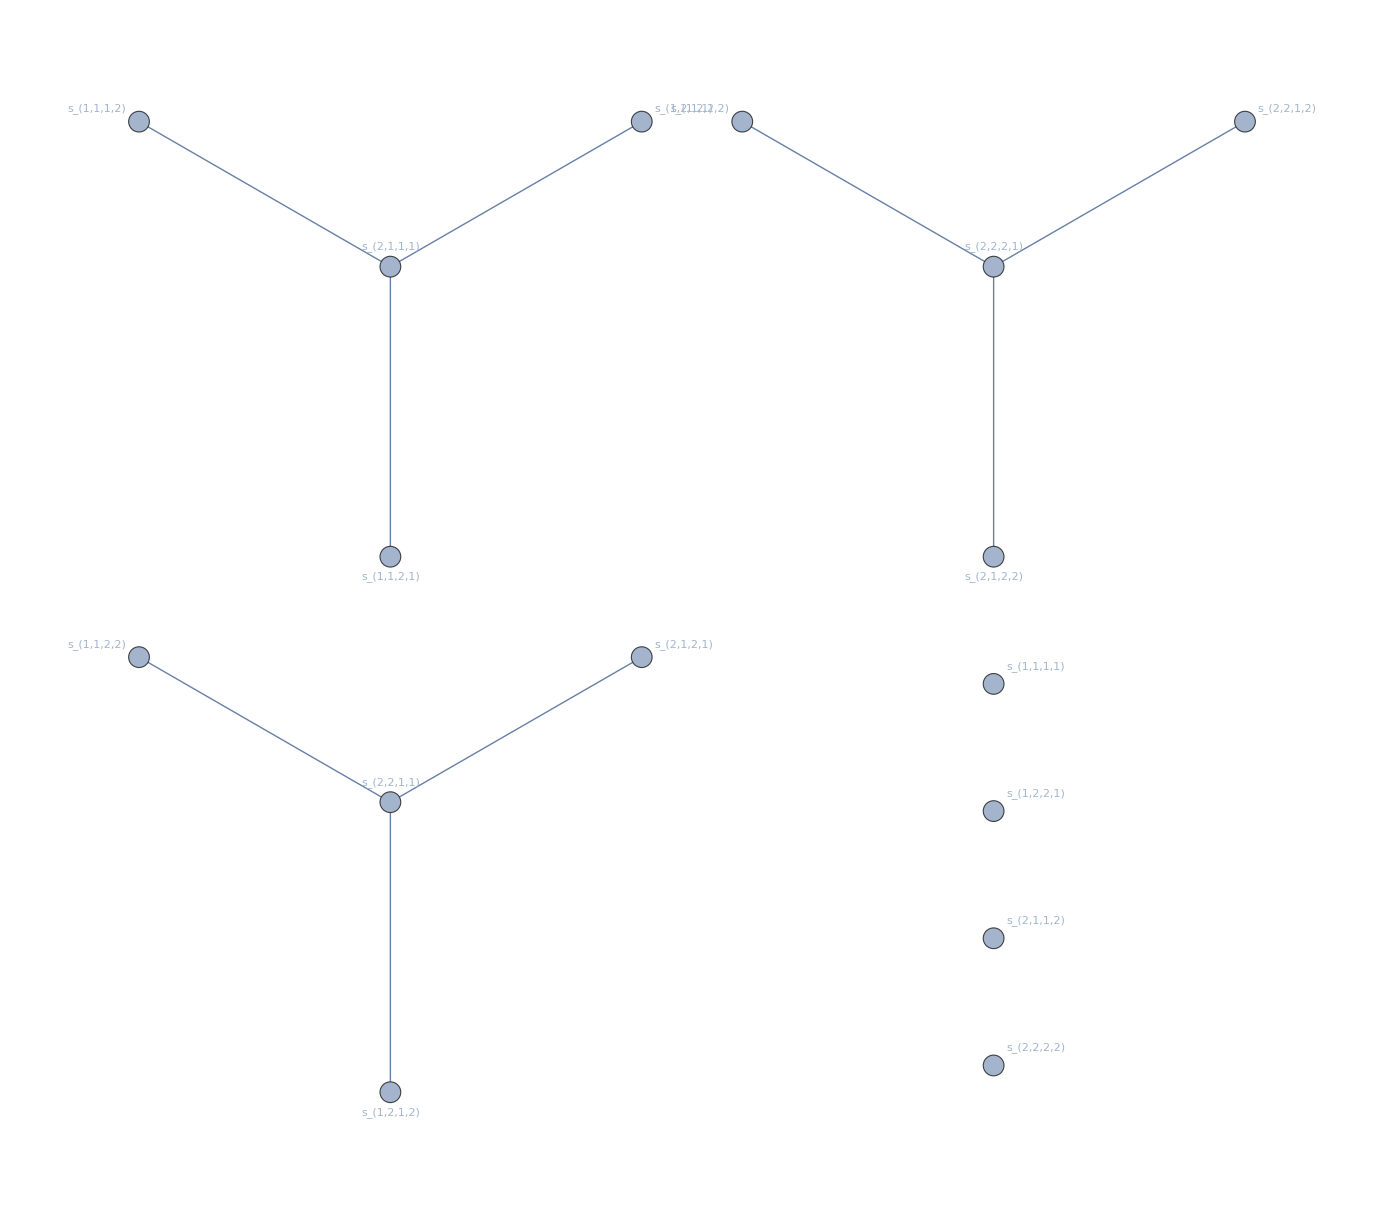

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars4,4,ngb4]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars4,4,ngb4]]]
```

{4,4,4,1,1,1,1}

```mathematica
shp[{1,1,1},{2}]
```

{{1,1,1,2},{1,1,2,1},{1,2,1,1},{2,1,1,1}}

```mathematica
shp[{1,1},{2,2}]
```

{{1,1,2,2},{1,2,1,2},{1,2,2,1},{2,1,1,2},{2,1,2,1},{2,2,1,1}}

```mathematica
shp[{1},{2,2,2}]
```

{{1,2,2,2},{2,1,2,2},{2,2,1,2},{2,2,2,1}}

```mathematica
sols4news22=First[Solve[eqs4s22/.Join[sols3,sols4news13],vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news22]
```

1

```mathematica
Length[Join[sols4news13/.sols4news22,sols4news22]]
```

13

```mathematica
sols4=Join[sols3,sols4news13/.sols4news22,sols4news22];
```

```mathematica
fund4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2)}

#### Level 5

```mathematica
vars5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}]];
```

```mathematica
eqs5s14=shuffles[vars1,vars4];
```

```mathematica
Timing[sols5news14=First[Solve[eqs5s14/.sols4,vars5]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.022789,Null}

```mathematica
Length[sols5news14]
```

24

```mathematica
eqs5s23=shuffles[vars2,vars3];
```

```mathematica
Length[Join[eqs5s14,eqs5s23]]
```

64

```mathematica
Timing[ngb5=netgroebner[Join[shufflespol[vars1,vars4],shufflespol[vars2,vars3]],vars5]]
```

{8.27739,{-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2),-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1),-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1),-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1),2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1),-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1),-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1),-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1),s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1),s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1),-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1),4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1),-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1),s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1),-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1),-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1),s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1),-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1),-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1),-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1),-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1),-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)}}

```mathematica
TableForm[ngb5]
```

-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2)
-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1)
-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1)
-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1)
2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1)
-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1)
-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1)
-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1)
s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1)
s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1)
-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1)
4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1)
-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1)
-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1)
-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1)
-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1)
-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1)
-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)

```mathematica
Map[pickvars[#,5]&,ngb5]
```

{{s_(2,2,2,2,2)},{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,1,1)}}

```mathematica
groups5=Select[Map[pickvars[#,5]&,ngb5],(Length[#]>1)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==2)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==3)&]
```

{{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)}}

```mathematica
pairs5=Union[Flatten[Map[Subsets[#,{2}]&,groups5],1]]
```

{{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,2,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1)},{s_(1,2,1,1,2),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1)},{s_(1,2,1,2,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1)},{s_(1,2,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1)},{s_(1,2,2,1,2),s_(2,2,2,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1)},{s_(1,2,2,2,1),s_(2,2,2,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1)},{s_(2,1,1,1,2),s_(2,2,1,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1)},{s_(2,1,1,2,1),s_(2,2,1,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1)},{s_(2,1,1,2,2),s_(2,2,2,1,1)},{s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1)},{s_(2,1,2,1,2),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1)},{s_(2,1,2,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1)},{s_(2,2,1,1,2),s_(2,2,2,1,1)},{s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,2,1,2),s_(2,2,2,2,1)}}

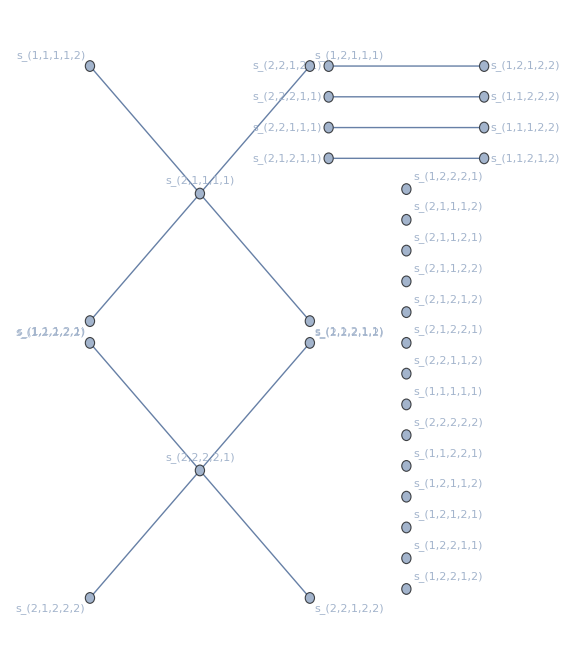

```mathematica
graphgroebner2[vars5,5,ngb5]
```

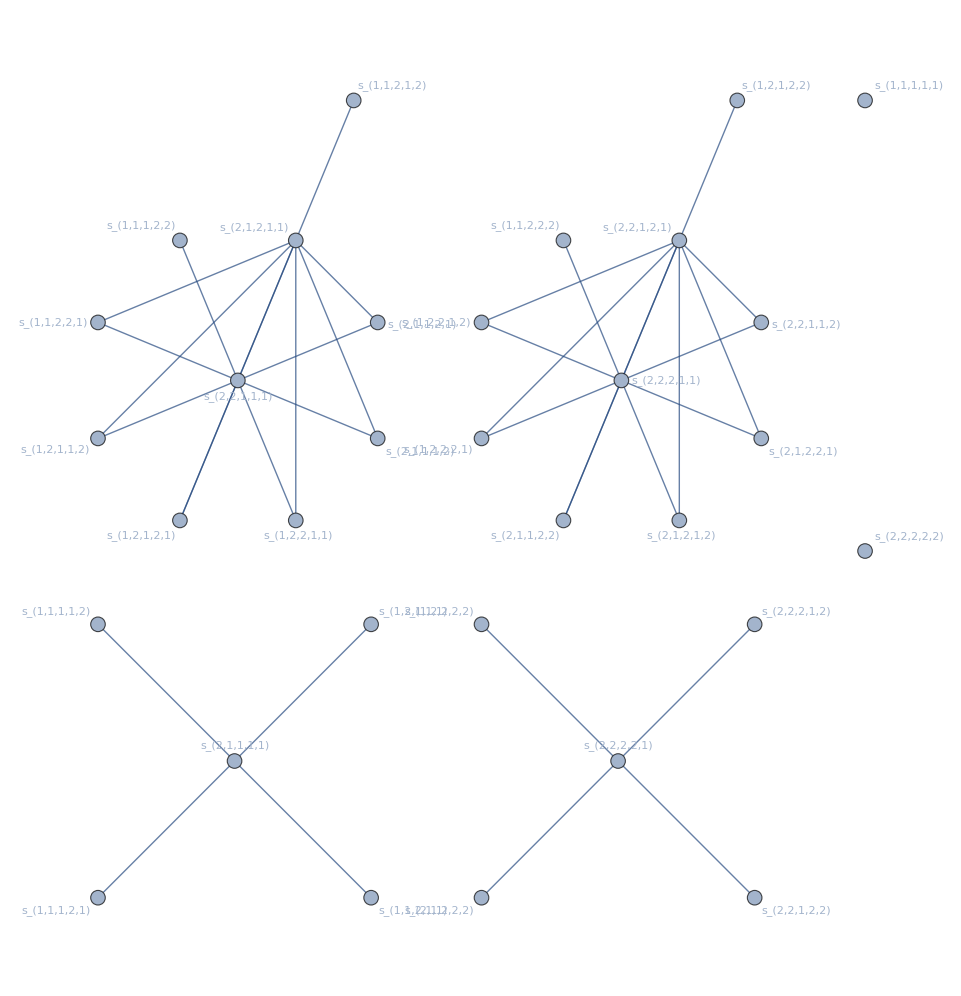

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars5,5,ngb5]
```

```mathematica
ArrayPlot[adjgroebner[vars5,5,ngb5],Mesh->True]
```

-Graphics-

```mathematica
Transpose[{vars5,Map[Total,adjgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Transpose[{vars5,VertexDegree[graphgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]]]
```

{10,10,5,5,1,1}

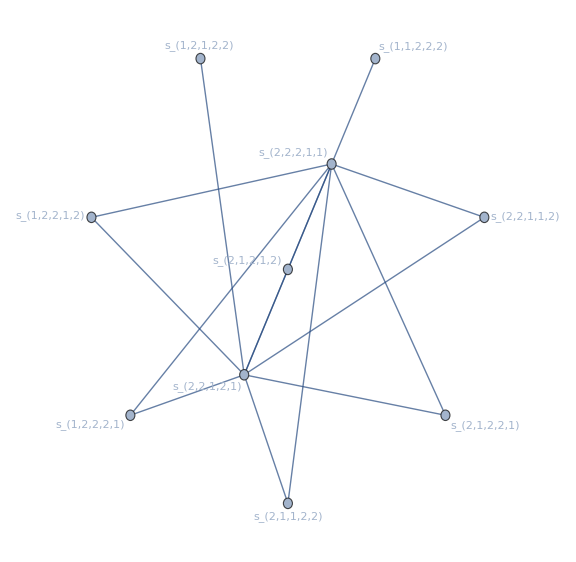

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[1]]
```

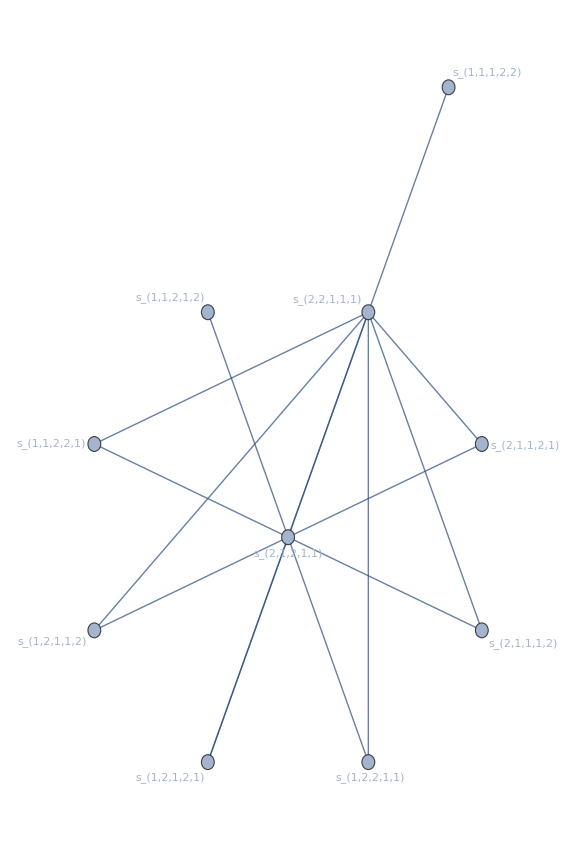

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[2]]
```

```mathematica
sols5news23=First[Solve[eqs5s23/.Join[sols4,sols5news14],vars5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols5news23]
```

2

```mathematica
sols5=Join[sols4,sols5news14/.sols5news23,sols5news23];
```

```mathematica
Length[Join[sols5news14/.sols5news23,sols5news23]]
```

26

```mathematica
fund5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2)}

#### Level 6

```mathematica
vars6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2}]];
```

```mathematica
eqs6s15=shuffles[vars1,vars5];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s15]]]],vars6]]],
ImageSize->Large]
```

-Graphics-

```mathematica
sols6news15=First[Solve[eqs6s15/.sols5,vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news15]
```

48

```mathematica
eqs6s24=shuffles[vars2,vars4];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s24]]]],vars6]]]]
```

-Graphics-

```mathematica
Timing[sols6news24=First[Solve[eqs6s24/.Join[sols5,sols6news15],vars6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.180305,Null}

```mathematica
Length[sols6news24]
```

4

```mathematica
eqs6s33=shuffles[vars3,vars3];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s33]]]],vars6]]]]
```

-Graphics-

```mathematica
sols6news33=First[Solve[eqs6s33/.Join[sols5,sols6news15/.sols6news24,sols6news24],vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news33]
```

3

```mathematica
{{Length[shufflespol[vars1,vars5]],Length[DeleteDuplicates[shufflespol[vars1,vars5]]]},
{Length[shufflespol[vars2,vars4]],Length[DeleteDuplicates[shufflespol[vars2,vars4]]]},
{Length[shufflespol[vars3,vars3]],Length[DeleteDuplicates[shufflespol[vars3,vars3]]]}}
```

{{64,64},{64,64},{64,36}}

```mathematica
Timing[ngb6s15=netgroebner[shufflespol[vars1,vars5],vars6];]
```

{9.46901,Null}

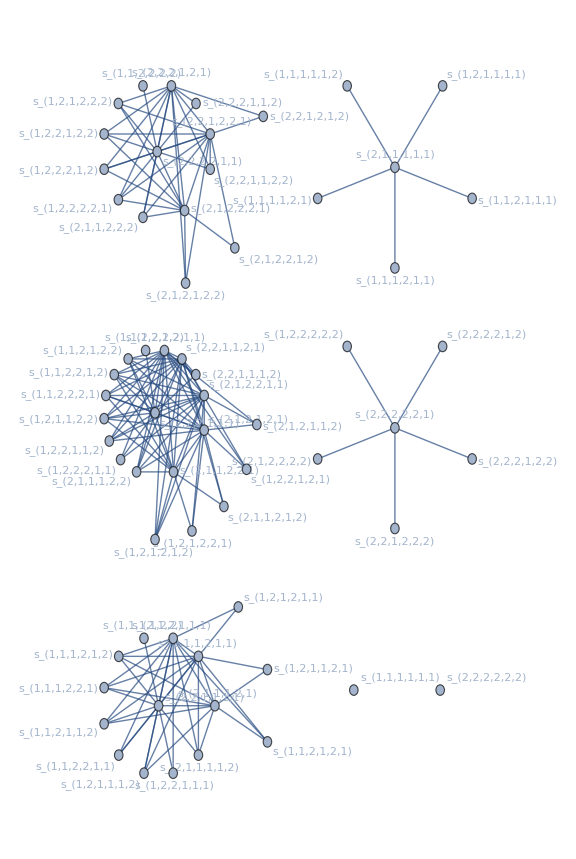

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars6,6,ngb6s15]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s15]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s24=netgroebner[shufflespol[vars2,vars4],vars6];]
```

{0.706315,Null}

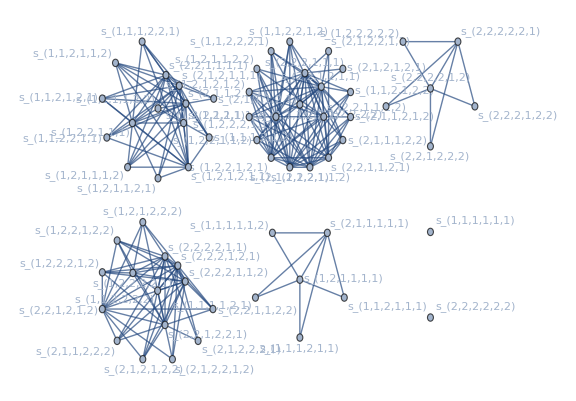

```mathematica
graphgroebner[vars6,6,ngb6s24]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s24]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s33=netgroebner[DeleteDuplicates[shufflespol[vars3,vars3]],vars6];]
```

{0.025654,Null}

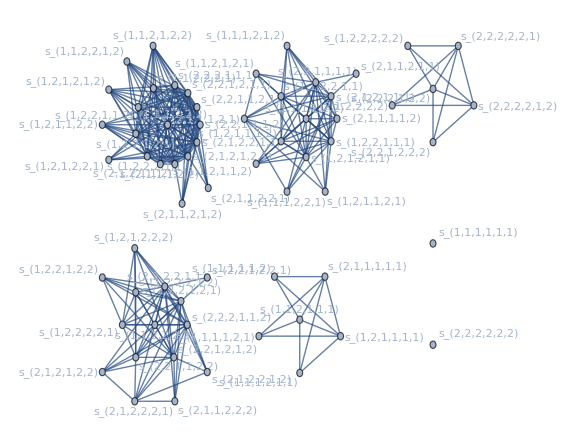

```mathematica
graphgroebner[vars6,6,ngb6s33]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s33]]]
```

{20,15,15,6,6,1,1}

```mathematica
Length[Join[sols6news15/.sols6news24/.sols6news33,sols6news24/.sols6news33,sols6news33]]
```

55

```mathematica
sols6=Join[sols5,sols6news15/.sols6news24/.sols6news33,sols6news24/.sols6news33,sols6news33];
```

```mathematica
fund6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2),s_(1,1,1,1,1,2),s_(1,1,1,1,2,2),s_(1,1,1,2,1,2),s_(1,1,1,2,2,2),s_(1,1,2,1,2,2),s_(1,1,2,2,1,2),s_(1,1,2,2,2,2),s_(1,2,1,2,2,2),s_(1,2,2,2,2,2)}

#### Size of core

```mathematica
Map[Length,{fund1,fund2,fund3,fund4,fund5,fund6}]
```

{2,3,5,8,14,23}

```mathematica
TableForm[Table[Binomial[n,m],{n,0,10},{m,0,n}]]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1

```mathematica
TableForm[Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  | 
1 | 2 | 2 | 1 |  |  |  |  | 
1 | 2 | 3 | 2 | 1 |  |  |  | 
1 | 3 | 5 | 5 | 3 | 1 |  |  | 
1 | 3 | 7 | 8 | 7 | 3 | 1 |  | 
1 | 4 | 9 | 14 | 14 | 9 | 4 | 1 | 
1 | 4 | 12 | 21 | 25 | 21 | 12 | 4 | 1

```mathematica
Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

{1,2,3,6,9,18,30,56,101}

```mathematica
2+Accumulate[Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,12},{m,1,n-1}]]]
```

{3,5,8,14,23,41,71,127,228,414,753}

```mathematica
2+∑_(n=2)^12 ∑_(k=1)^(n-1) ⌊Binomial[n,k]/n⌋
```

753

```mathematica
2+∑_(n=2)^m ∑_(k=1)^(n-1) ⌊1/n Binomial[n,k]⌋
```

### d=3

#### Level 1

```mathematica
vars3d1=Flatten[Table[sind[{i}],{i,1,3}]]
```

{s_1,s_2,s_3}

```mathematica
fund3d1=vars3d1
```

{s_1,s_2,s_3}

#### Level 2

```mathematica
vars3d2=Flatten[Table[sind[{i,j}],{i,1,3},{j,1,3}]]
```

{s_(1,1),s_(1,2),s_(1,3),s_(2,1),s_(2,2),s_(2,3),s_(3,1),s_(3,2),s_(3,3)}

```mathematica
eqs3d2=shuffles[vars3d1,vars3d1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,3)+s_(3,1)==s_1 s_3,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2,s_(2,3)+s_(3,2)==s_2 s_3,s_(1,3)+s_(3,1)==s_1 s_3,s_(2,3)+s_(3,2)==s_2 s_3,2 s_(3,3)==s_3^2}

```mathematica
sols3d2=First[Solve[eqs3d2,vars3d2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2,s_(3,1)→s_1 s_3-s_(1,3),s_(3,2)→s_2 s_3-s_(2,3),s_(3,3)→s_3^2/2}

```mathematica
fund3d2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d2]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3)}

#### Level 3

```mathematica
vars3d3=Flatten[Table[sind[{i,j,k}],{i,1,3},{j,1,3},{k,1,3}]];
```

```mathematica
eqs3d3=shuffles[vars3d1,vars3d2];
```

```mathematica
sols3d3new=First[Solve[eqs3d3/.sols3d2,vars3d3]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sols3d3=Join[sols3d2,sols3d3new];
```

```mathematica
fund3d3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d3]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3)}

#### Level 4

```mathematica
vars3d4=Flatten[Table[sind[{i,j,k,l}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]];
```

```mathematica
eqs3d4s13=shuffles[vars3d1,vars3d3];
```

```mathematica
sols3d4news13=First[Solve[eqs3d4s13/.sols3d3,vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news13]
```

57

```mathematica
eqs3d4s22=shuffles[vars3d2,vars3d2];
```

```mathematica
sols3d4news22=First[Solve[eqs3d4s22/.Join[sols3d3,sols3d4news13],vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news22]
```

6

```mathematica
sols3d4=Join[sols3d3,sols3d4news13/.sols3d4news22,sols3d4news22];
```

```mathematica
fund3d4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d4]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3)}

#### Level 5

```mathematica
vars3d5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3}]];
```

```mathematica
eqs3d5s14=shuffles[vars3d1,vars3d4];
```

```mathematica
sols3d5news14=First[Solve[eqs3d5s14/.sols3d4,vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news14]
```

171

```mathematica
eqs3d5s23=shuffles[vars3d2,vars3d3];
```

```mathematica
sols3d5news23=First[Solve[eqs3d5s23/.Join[sols3d4,sols3d5news14],vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news23]
```

24

```mathematica
sols3d5=Join[sols3d4,sols3d5news14/.sols3d5news23,sols3d5news23];
```

```mathematica
fund3d5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d5]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3)}

#### Level 6

```mathematica
vars3d6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3}]];
```

```mathematica
eqs3d6s15=shuffles[vars3d1,vars3d5];
```

```mathematica
Timing[sols3d6news15=First[Solve[eqs3d6s15/.sols3d5,vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.51999,Null}

```mathematica
Length[sols3d6news15]
```

513

```mathematica
eqs3d6s24=shuffles[vars3d2,vars3d4];
```

```mathematica
Length[eqs3d6s24]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]]]
```

469

```mathematica
Timing[sols3d6news24=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.613537,Null}

```mathematica
Length[sols3d6news24]
```

64

```mathematica
eqs3d6s33=shuffles[vars3d3,vars3d3];
```

```mathematica
Length[eqs3d6s33]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]]]
```

301

```mathematica
Timing[sols3d6news33=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.0498,Null}

```mathematica
Length[sols3d6news33]
```

36

```mathematica
sols3d6=Join[sols3d5,sols3d6news15/.sols3d6news24/.sols3d6news33,sols3d6news24/.sols3d6news33,sols3d6news33];
```

```mathematica
fund3d6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d6]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3),s_(1,1,1,1,1,2),s_(1,1,1,1,1,3),s_(1,1,1,1,2,2),s_(1,1,1,1,2,3),s_(1,1,1,1,3,2),s_(1,1,1,1,3,3),s_(1,1,1,2,1,2),s_(1,1,1,2,1,3),s_(1,1,1,2,2,2),s_(1,1,1,2,2,3),s_(1,1,1,2,3,2),s_(1,1,1,2,3,3),s_(1,1,1,3,1,2),s_(1,1,1,3,1,3),s_(1,1,1,3,2,2),s_(1,1,1,3,2,3),s_(1,1,1,3,3,2),s_(1,1,1,3,3,3),s_(1,1,2,1,1,3),s_(1,1,2,1,2,2),s_(1,1,2,1,2,3),s_(1,1,2,1,3,2),s_(1,1,2,1,3,3),s_(1,1,2,2,1,2),s_(1,1,2,2,1,3),s_(1,1,2,2,2,2),s_(1,1,2,2,2,3),s_(1,1,2,2,3,2),s_(1,1,2,2,3,3),s_(1,1,2,3,1,2),s_(1,1,2,3,1,3),s_(1,1,2,3,2,2),s_(1,1,2,3,2,3),s_(1,1,2,3,3,2),s_(1,1,2,3,3,3),s_(1,1,3,1,2,2),s_(1,1,3,1,2,3),s_(1,1,3,1,3,2),s_(1,1,3,1,3,3),s_(1,1,3,2,1,2),s_(1,1,3,2,1,3),s_(1,1,3,2,2,2),s_(1,1,3,2,2,3),s_(1,1,3,2,3,2),s_(1,1,3,2,3,3),s_(1,1,3,3,1,2),s_(1,1,3,3,1,3),s_(1,1,3,3,2,2),s_(1,1,3,3,2,3),s_(1,1,3,3,3,2),s_(1,1,3,3,3,3),s_(1,2,1,2,1,3),s_(1,2,1,2,2,2),s_(1,2,1,2,2,3),s_(1,2,1,2,3,2),s_(1,2,1,2,3,3),s_(1,2,1,3,1,3),s_(1,2,1,3,2,2),s_(1,2,1,3,2,3),s_(1,2,1,3,3,2),s_(1,2,1,3,3,3),s_(1,2,2,1,2,3),s_(1,2,2,1,3,2),s_(1,2,2,1,3,3),s_(1,2,2,2,1,3),s_(1,2,2,2,2,2),s_(1,2,2,2,2,3),s_(1,2,2,2,3,2),s_(1,2,2,2,3,3),s_(1,2,2,3,1,3),s_(1,2,2,3,2,2),s_(1,2,2,3,2,3),s_(1,2,2,3,3,2),s_(1,2,2,3,3,3),s_(1,2,3,1,3,2),s_(1,2,3,1,3,3),s_(1,2,3,2,1,3),s_(1,2,3,2,2,2),s_(1,2,3,2,2,3),s_(1,2,3,2,3,2),s_(1,2,3,2,3,3),s_(1,2,3,3,1,3),s_(1,2,3,3,2,2),s_(1,2,3,3,2,3),s_(1,2,3,3,3,2),s_(1,2,3,3,3,3),s_(1,3,1,3,2,2),s_(1,3,1,3,2,3),s_(1,3,1,3,3,2),s_(1,3,1,3,3,3),s_(1,3,2,1,3,3),s_(1,3,2,2,2,2),s_(1,3,2,2,2,3),s_(1,3,2,2,3,2),s_(1,3,2,2,3,3),s_(1,3,2,3,2,2),s_(1,3,2,3,2,3),s_(1,3,2,3,3,2),s_(1,3,2,3,3,3),s_(1,3,3,2,2,2),s_(1,3,3,2,2,3),s_(1,3,3,2,3,2),s_(1,3,3,2,3,3),s_(1,3,3,3,2,2),s_(1,3,3,3,2,3),s_(1,3,3,3,3,2),s_(1,3,3,3,3,3),s_(2,2,2,2,2,3),s_(2,2,2,2,3,3),s_(2,2,2,3,2,3),s_(2,2,2,3,3,3),s_(2,2,3,2,3,3),s_(2,2,3,3,2,3),s_(2,2,3,3,3,3),s_(2,3,2,3,3,3),s_(2,3,3,3,3,3)}

#### Size of core

```mathematica
Map[Length,{fund3d1,fund3d2,fund3d3,fund3d4,fund3d5,fund3d6}]
```

{3,6,14,32,80,196}

## Inversion

### Functions

```mathematica
fpointspath[sollist_]:=Map[Last,sollist];
```

```mathematica
flengthpath[sollist_]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Total[MapThread[EuclideanDistance,{Most[pts],Rest[pts]}]]];
```

```mathematica
flengthpathpts[pts_]:=Total[MapThread[EuclideanDistance,{Most[pts],Rest[pts]}]];
```

```mathematica
flistpath[sollist_,init_]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Accumulate[Prepend[pts,init]]];
```

```mathematica
flistbetat[sollist_,init_:{0,0}]:=Module[{n,ptsbetat,pts},
n=Length[sollist]/2;
ptsbetat=Transpose[Partition[Map[Last,sollist],n]];
pts=Accumulate[Prepend[Map[{#[[2]],#[[1]]*#[[2]]}&,ptsbetat],init]];
pts];
```

```mathematica
fpw2[sollist_,t_]:=Module[{T,t1,β1,β2},
{T,t1,β1,β2}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤T}}]];
```

## d=2, X_1(t)=Y_1(t)=t

### 2 lines

#### Solution

```mathematica
sigx4=sigvarsubscr6[x,4]
```

{{1},{x_1,x_2},{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)}},{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}},{{{{x_(1,1,1,1),x_(1,1,1,2)},{x_(1,1,2,1),x_(1,1,2,2)}},{{x_(1,2,1,1),x_(1,2,1,2)},{x_(1,2,2,1),x_(1,2,2,2)}}},{{{x_(2,1,1,1),x_(2,1,1,2)},{x_(2,1,2,1),x_(2,1,2,2)}},{{x_(2,2,1,1),x_(2,2,1,2)},{x_(2,2,2,1),x_(2,2,2,2)}}}}}

```mathematica
sigy4=sigvarsubscr6[y,4]
```

{{1},{y_1,y_2},{{y_(1,1),y_(1,2)},{y_(2,1),y_(2,2)}},{{{y_(1,1,1),y_(1,1,2)},{y_(1,2,1),y_(1,2,2)}},{{y_(2,1,1),y_(2,1,2)},{y_(2,2,1),y_(2,2,2)}}},{{{{y_(1,1,1,1),y_(1,1,1,2)},{y_(1,1,2,1),y_(1,1,2,2)}},{{y_(1,2,1,1),y_(1,2,1,2)},{y_(1,2,2,1),y_(1,2,2,2)}}},{{{y_(2,1,1,1),y_(2,1,1,2)},{y_(2,1,2,1),y_(2,1,2,2)}},{{y_(2,2,1,1),y_(2,2,1,2)},{y_(2,2,2,1),y_(2,2,2,2)}}}}}

```mathematica
chenz4=sigchen[sigx4,sigy4,4];
```

```mathematica
chenz4core=getcore6[chenz4,4];
```

```mathematica
Grid[chenz4core,Frame->All]
```

x_1+y_1 | x_2+y_2 | 
x_1 y_2+x_(1,2)+y_(1,2) |  | 
y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2) | y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2) | 
x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2) | x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2) | x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)

```mathematica
line2d4=signat[{{t,β t}},{0,T},4][[1]]
```

{{1},{T,T β},{{T^2/2,(T^2 β)/2},{(T^2 β)/2,(T^2 β^2)/2}},{{{T^3/6,(T^3 β)/6},{(T^3 β)/6,(T^3 β^2)/6}},{{(T^3 β)/6,(T^3 β^2)/6},{(T^3 β^2)/6,(T^3 β^3)/6}}},{{{{T^4/24,(T^4 β)/24},{(T^4 β)/24,(T^4 β^2)/24}},{{(T^4 β)/24,(T^4 β^2)/24},{(T^4 β^2)/24,(T^4 β^3)/24}}},{{{(T^4 β)/24,(T^4 β^2)/24},{(T^4 β^2)/24,(T^4 β^3)/24}},{{(T^4 β^2)/24,(T^4 β^3)/24},{(T^4 β^3)/24,(T^4 β^4)/24}}}}}

```mathematica
{sigtake[line2d4,{2,1,1,1}],signatline[{1,β},{2,1,1,1},T]}
```

{(T^4 β)/24,(T^4 β)/24}

```mathematica
varslinechen={Subscript[β, 1],Subscript[β, 2],Subscript[t, 1],T};
```

```mathematica
eqslinechen23={T==Subscript[z, 1],
signatline[{1,Subscript[β, 1]},{2},Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]==Subscript[z, 2],
signatline[{1,Subscript[β, 1]},{1,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,2},T-Subscript[t, 1]]==Subscript[z, 1,2],
signatline[{1,Subscript[β, 1]},{1,1,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1,1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{1,2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,1,2},T-Subscript[t, 1]]==Subscript[z, 1,1,2],
signatline[{1,Subscript[β, 1]},{1,2,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1,2},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2,2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,2,2},T-Subscript[t, 1]]==Subscript[z, 1,2,2]};
```

```mathematica
Grid[Transpose[{eqslinechen23}],Frame->All]
```

T==z_1
t_1 β_1+(T-t_1) β_2==z_2
1/2 t_1^2 β_1+1/2 (T-t_1)^2 β_2+(T-t_1) t_1 β_2==z_(1,2)
1/6 t_1^3 β_1+1/6 (T-t_1)^3 β_2+1/2 (T-t_1)^2 t_1 β_2+1/2 (T-t_1) t_1^2 β_2==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 (T-t_1) t_1^2 β_1 β_2+1/6 (T-t_1)^3 β_2^2+1/2 (T-t_1)^2 t_1 β_2^2==z_(1,2,2)

```mathematica
FullSimplify[Solve[eqslinechen23,varslinechen]]
```

{}

```mathematica
sol3symbex5=First[FullSimplify[Solve[Delete[eqslinechen23,5],varslinechen]]]
```

{β_1→(z_1^2 z_2^2-2 z_1 z_2 z_(1,2)+4 z_(1,2)^2-6 z_2 z_(1,1,2))/(2 z_1^2 z_(1,2)-6 z_1 z_(1,1,2)),β_2→(-4 z_(1,2)^2+6 z_2 z_(1,1,2))/(z_1 (z_1^2 z_2-4 z_1 z_(1,2)+6 z_(1,1,2))),t_1→(2 z_1 z_(1,2)-6 z_(1,1,2))/(z_1 z_2-2 z_(1,2)),T→z_1}

```mathematica
sol3symbex4=First[FullSimplify[Solve[Delete[eqslinechen23,4],varslinechen]]]
```

{β_1→(z_2 (z_1 z_2^2-4 z_2 z_(1,2)+6 z_(1,2,2)))/(-4 z_(1,2)^2+6 z_1 z_(1,2,2)),β_2→(2 z_2 (z_2 z_(1,2)-3 z_(1,2,2)))/(z_1^2 z_2^2+4 z_(1,2)^2-2 z_1 (z_2 z_(1,2)+3 z_(1,2,2))),t_1→(-4 z_(1,2)^2+6 z_1 z_(1,2,2))/(z_2 (z_1 z_2-2 z_(1,2))),T→z_1}

```mathematica
FullSimplify[eqslinechen23[[5]]/.{Subscript[β, 1]->(Subscript[z, 1]^2 Subscript[z, 2]^2-2 Subscript[z, 1] Subscript[z, 2] Subscript[z, 1,2]+4 Subscript[z, 1,2]^2-6 Subscript[z, 2] Subscript[z, 1,1,2])/(2 Subscript[z, 1]^2 Subscript[z, 1,2]-6 Subscript[z, 1] Subscript[z, 1,1,2]),Subscript[β, 2]->(-4 Subscript[z, 1,2]^2+6 Subscript[z, 2] Subscript[z, 1,1,2])/(Subscript[z, 1] (Subscript[z, 1]^2 Subscript[z, 2]-4 Subscript[z, 1] Subscript[z, 1,2]+6 Subscript[z, 1,1,2])),Subscript[t, 1]->(2 Subscript[z, 1] Subscript[z, 1,2]-6 Subscript[z, 1,1,2])/(Subscript[z, 1] Subscript[z, 2]-2 Subscript[z, 1,2]),T->Subscript[z, 1]}]
```

(2 z_(1,2)^2+z_2 (z_1 z_(1,2)-3 z_(1,1,2)))/z_1==3 z_(1,2,2)

```mathematica
FullSimplify[eqslinechen23[[4]]/.{Subscript[β, 1]->(Subscript[z, 2] (Subscript[z, 1] Subscript[z, 2]^2-4 Subscript[z, 2] Subscript[z, 1,2]+6 Subscript[z, 1,2,2]))/(-4 Subscript[z, 1,2]^2+6 Subscript[z, 1] Subscript[z, 1,2,2]),Subscript[β, 2]->(2 Subscript[z, 2] (Subscript[z, 2] Subscript[z, 1,2]-3 Subscript[z, 1,2,2]))/(Subscript[z, 1]^2 Subscript[z, 2]^2+4 Subscript[z, 1,2]^2-2 Subscript[z, 1] (Subscript[z, 2] Subscript[z, 1,2]+3 Subscript[z, 1,2,2])),Subscript[t, 1]->(-4 Subscript[z, 1,2]^2+6 Subscript[z, 1] Subscript[z, 1,2,2])/(Subscript[z, 2] (Subscript[z, 1] Subscript[z, 2]-2 Subscript[z, 1,2])),T->Subscript[z, 1]}]
```

(2 z_(1,2)^2+z_1 (z_2 z_(1,2)-3 z_(1,2,2)))/(3 z_2)==z_(1,1,2)

```mathematica
pts3symbex5=FullSimplify[{{Subscript[t, 1],Subscript[β, 1]*Subscript[t, 1]},
{T,Subscript[β, 1]*Subscript[t, 1]+Subscript[β, 2]*(T-Subscript[t, 1])}}/.sol3symbex5]
```

{{(2 z_1 z_(1,2)-6 z_(1,1,2))/(z_1 z_2-2 z_(1,2)),(z_1^2 z_2^2-2 z_1 z_2 z_(1,2)+4 z_(1,2)^2-6 z_2 z_(1,1,2))/(z_1^2 z_2-2 z_1 z_(1,2))},{z_1,z_2}}

```mathematica
pts3symbex4=FullSimplify[{{Subscript[t, 1],Subscript[β, 1]*Subscript[t, 1]},
{T,Subscript[β, 1]*Subscript[t, 1]+Subscript[β, 2]*(T-Subscript[t, 1])}}/.sol3symbex4]
```

{{(-4 z_(1,2)^2+6 z_1 z_(1,2,2))/(z_2 (z_1 z_2-2 z_(1,2))),(z_1 z_2^2-4 z_2 z_(1,2)+6 z_(1,2,2))/(z_1 z_2-2 z_(1,2))},{z_1,z_2}}

```mathematica
solsts2p[core3_]:=Module[{z1,z2,z12,z112,z122,solsno5,solsno4},
{z1,z2,z12,z112,z122}=core3;
solsno5={z1,(2 z1 z12-6 z112)/(z1 z2-2 z12),(z1^2  z2^2-2 z1 z2 z12+4 z12^2-6 z2 z112)/(2 z1^2 z12-6 z1 z112),(-4 z12^2+6 z2 z112)/(z1 (z1^2 z2-4 z1 z12+6 z112))};
solsno4={z1,(-4 z12^2+6 z1 z122)/(z2 (z1 z2-2z12)),(z2 (z1 z2^2-4 z2 z12+6 z122))/(-4 z12^2+6 z1 z122),(2 z2 (z2 z12-3 z122))/(z1^2 z2^2+4 z12^2-2 z1 (z2 z12+3z122))};
{solsno5,solsno4}
];
```

```mathematica
solsts2pts[core3_,init_:{0,0}]:=Module[{z1,z2,z12,z112,z122,solsno5,solsno4},
{z1,z2,z12,z112,z122}=core3;
solsno5=Map[(init+#)&,{{0,0},{(2 z1 z12-6 z112)/(z1 z2-2z12),(z1^2  z2^2-2 z1 z2 z12+4 z12^2-6 z2 z112)/(z1 (z1 z2-2z12))},{z1,z2}}];
solsno4=Map[(init+#)&,{{0,0},{(-4 z12^2+6 z1 z122)/(z2 (z1 z2-2z12)),(z1 z2^2-4 z2 z12+6 z122)/(z1 z2-2 z12)},{z1,z2}}];
{solsno5,solsno4}
];
```

#### Sin[π t]

```mathematica
sinp1core=getcore6[sigsins1f,3];
```

```mathematica
sinp1core
```

{{1,0},{-2/π},{-1/π,1/4}}

```mathematica
solsts2p[Flatten[sinp1core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{1,1/2,8/π,-8/π},{1,ComplexInfinity,0,0}}

```mathematica
{sinpit2sa,sinpit2sb}=solsts2pts[Flatten[sinp1core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{{0,0},{1/2,4/π},{1,0}},{{0,0},{ComplexInfinity,(3 π)/8},{1,0}}}

```mathematica
N[flengthpathpts[sinpit2sa]]
```

2.73579

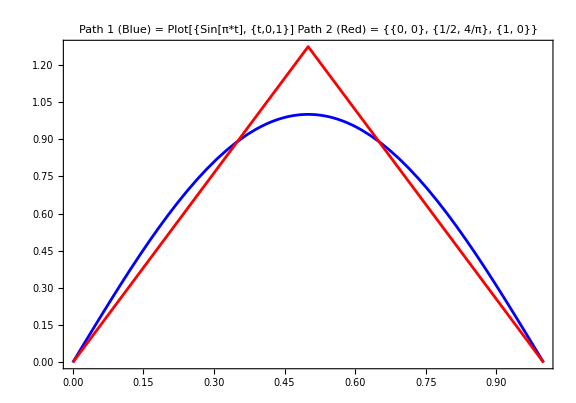

```mathematica
Show[Plot[Sin[π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t], {t,0,1}]
Path 2 (Red) = {{0, 0}, {1/2, 4/π}, {1, 0}}"],16]],
ListLinePlot[sinpit2sa,
PlotStyle->{ Red}]]
```

#### Sin[π t^2]

```mathematica
sinp3core=getcore6[sigsins1f2,3];
```

```mathematica
sinp3core
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])}}

```mathematica
solsts2p[Flatten[sinp3core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{1,(6/π-√2 FresnelS[√2])/(√2 FresnelS[√2]),(2 FresnelS[√2]^2)/(6/π-√2 FresnelS[√2]),-(2 FresnelS[√2]^2)/(-6/π+2 √2 FresnelS[√2])},{1,ComplexInfinity,0,0}}

```mathematica
{sinpitsq2sa,sinpitsq2sb}=solsts2pts[Flatten[sinp3core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{{0,0},{(6/π-√2 FresnelS[√2])/(√2 FresnelS[√2]),√2 FresnelS[√2]},{1,0}},{{0,0},{ComplexInfinity,(3 (2-FresnelC[2]))/(4 √2 FresnelS[√2])},{1,0}}}

```mathematica
N[flengthpathpts[sinpitsq2sa]]
```

2.36247

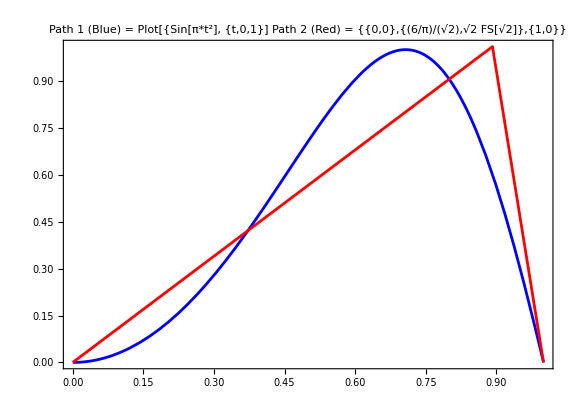

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2], {t,0,1}]
Path 2 (Red) = {{0,0},{(6/π)/(√2),√2 FS[√2]},{1,0}}"],16]],
ListLinePlot[sinpitsq2sa,
PlotStyle->{ Red}]]
```

#### Sin[π t^2]+1-t

```mathematica
Timing[sigsins2p1=signat[{{t,Sin[π (t)^2]+1-t}},{0,1},4][[1]]]
```

{55.9089,{{1},{1,-1},{{1/2,-1/2-FresnelS[√2]/(√2)},{-1/2+FresnelS[√2]/(√2),1/2}},{{{1/6,-(6+π)/(6 π)},{-1/6+2/π-FresnelS[√2]/(√2),5/12-1/π-FresnelC[2]/8+FresnelS[√2]/(√2)}},{{-1/6-1/π+FresnelS[√2]/(√2),-1/3+2/π+FresnelC[2]/4-FresnelS[√2]/(√2)},{5/12-1/π-FresnelC[2]/8,-1/6}}},{{{{1/24,-(6+π+3 √2 FresnelC[√2])/(24 π)},{-(6+π-9 √2 FresnelC[√2])/(24 π),(3+π-(3 FresnelC[√2])/(√2))/(6 π)}},{{-(-30+π+9 √2 FresnelC[√2]+6 √2 π FresnelS[√2])/(24 π),-(6-3 √2 FresnelC[√2]+1/4 π (5-6 FresnelS[√2] (√2+FresnelS[√2])))/(6 π)},{-1/π+1/24 (7-3 FresnelC[2]+6 √2 FresnelS[√2]-6 FresnelS[√2]^2),1/144 (-24+18 FresnelC[2]-(18 (-6+√2 FresnelC[√2]))/π-45 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{-(18+π-3 √2 FresnelC[√2]-6 √2 π FresnelS[√2])/(24 π),1/π+1/24 (1-6 √2 FresnelS[√2]-6 FresnelS[√2]^2)},{(24-12 √2 FresnelC[√2]+π (-5+6 FresnelC[2]-6 √2 FresnelS[√2]+6 FresnelS[√2]^2))/(24 π),(-60+18 √2 FresnelC[√2]+π (4-12 FresnelC[2]+21 √2 FresnelS[√2]-√6 FresnelS[√6]))/(48 π)}},{{(-12+4 π-3 π FresnelC[2]+6 √2 FresnelC[√2])/(24 π),1/24 (2+3 FresnelC[2]+(6-9 √2 FresnelC[√2])/π-(9 FresnelS[√2])/(√2)+√(3/2) FresnelS[√6])},{1/144 (-24+(18 (2+√2 FresnelC[√2]))/π+9 √2 FresnelS[√2]-√6 FresnelS[√6]),1/24}}}}}}

```mathematica
sinp7core=getcore6[sigsins2p1,3]
```

{{1,-1},{-1/2-FresnelS[√2]/(√2)},{-(6+π)/(6 π),5/12-1/π-FresnelC[2]/8+FresnelS[√2]/(√2)}}

```mathematica
FullSimplify[solsts2p[Flatten[sinp7core]]]
```

{{1,-1+(3 √2)/(π FresnelS[√2]),(6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]),(3-π FresnelS[√2] (√2+FresnelS[√2]))/(-3+√2 π FresnelS[√2])},{1,(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]),-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)),-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2])))}}

```mathematica
{sinpitsqp1mt2sa,sinpitsqp1mt2sb}=FullSimplify[solsts2pts[Flatten[sinp7core],{0,1}]]
```

{{{0,1},{-1+(3 √2)/(π FresnelS[√2]),2+(√2 (-3+π FresnelS[√2]^2))/(π FresnelS[√2])},{1,0}},{{0,1},{(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]),(-24+π (6-3 FresnelC[2]+8 √2 FresnelS[√2]))/(4 √2 π FresnelS[√2])},{1,0}}}

```mathematica
N[{sinpitsqp1mt2sa,sinpitsqp1mt2sb}]
```

{{{0.,1.},{0.891494,1.11821},{1.,0.}},{{0.,1.},{0.778296,1.23141},{1.,0.}}}

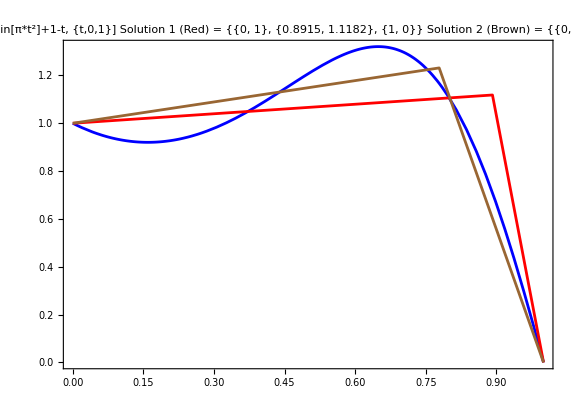

```mathematica
Show[Plot[Sin[π t^2]+1-t,{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2]+1-t, {t,0,1}]
Solution 1 (Red) = {{0, 1}, {0.8915, 1.1182}, {1, 0}}
Solution 2 (Brown) = {{0, 1}, {0.7783, 1.2314}, {1, 0}}"],16]],
ListLinePlot[{sinpitsqp1mt2sa,sinpitsqp1mt2sb},
PlotStyle->{ Red,Brown}]]
```

```mathematica
D[Sin[π*t^2]+1-t,{t,2}]
```

2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2]

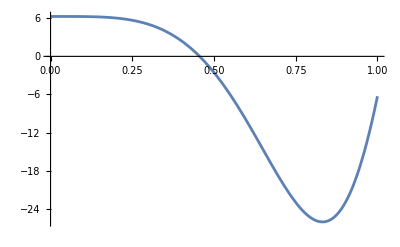

```mathematica
Plot[2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2],{t,0,1}]
```

```mathematica
NMinimize[{2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2],0<=t<=1},t]
```

{-26.0624,{t→0.831989}}

```mathematica
FindRoot[(Sin[π t^2]+1-t)-(1+((6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]))t),{t,0.9},WorkingPrecision->10]
```

{t→0.7996158802}

```mathematica
FindRoot[(Sin[π t^2]+1-t)-(1+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)))((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]))+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2]))))(t-((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2])))),{t,0.85},WorkingPrecision->10]
```

{t→0.8025343779}

```mathematica
FindRoot[(1+((6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]))t)-(1+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)))((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]))+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2]))))(t-((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2])))),{t,0.85},WorkingPrecision->10]
```

FindRoot::bddir: The search direction {-3.416419792×10^-17} is not a descent direction for the merit function. The step will be taken without the line search.

{t→0.8008406871}

#### Two segments (Chen)

```mathematica
getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]
```

{{t_1+t_2,t_1 β_1+t_2 β_2},{1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2},{1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2,1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2}}

```mathematica
FullSimplify[solsts2p[Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]]]]
```

{{t_1+t_2,t_1,β_1,β_2},{t_1+t_2,t_1,β_1,β_2}}

```mathematica
FullSimplify[solsts2pts[Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]]]]
```

{{{0,0},{t_1,t_1 β_1},{t_1+t_2,t_1 β_1+t_2 β_2}},{{0,0},{t_1,t_1 β_1},{t_1+t_2,t_1 β_1+t_2 β_2}}}

```mathematica
eqschen2=MapThread[Equal,{Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]],{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2]}}]
```

{t_1+t_2==z_1,t_1 β_1+t_2 β_2==z_2,1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2==z_(1,2),1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2==z_(1,1,2),1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2==z_(1,2,2)}

### d=2, X_1(t)=Y_1(t)=t, 3 lines

```mathematica
chen3z4=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},4][[1]]},
4];
```

```mathematica
chen3z4core=getcore6[chen3z4,4];
```

```mathematica
Grid[Expand[chen3z4core],Frame->All]
```

t_1+t_2+t_3 | t_1 β_1+t_2 β_2+t_3 β_3 | 
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3 |  | 
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3 | 1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2 | 
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3 | 1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2 | 1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3

```mathematica
vars3linechen={Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]};
```

```mathematica
eqs3linechen234=MapThread[Equal,{
Expand[Flatten[chen3z4core]],
{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]}}];
```

```mathematica
Grid[Transpose[{eqs3linechen234}],Frame->All]
```

t_1+t_2+t_3==z_1
t_1 β_1+t_2 β_2+t_3 β_3==z_2
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3==z_(1,2)
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2==z_(1,2,2)
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3==z_(1,1,1,2)
1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2==z_(1,1,2,2)
1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3==z_(1,2,2,2)

```mathematica
cores4={Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]};
```

```mathematica
solve3lines[eqsleft_,cores_,vars_,delpos_:{},bounds_:{},precis_:Automatic]:=Module[{eqs},
eqs=MapThread[Equal,{eqsleft,cores}];
NSolve[Join[Delete[eqs,delpos],bounds],vars,Reals,WorkingPrecision->precis]];
```

```mathematica
fpw3[sollist_,t_]:=Module[{β1,β2,β3,t1,t2,t3},
{β1,β2,β3,t1,t2,t3}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤(t1+t2)}, {β1 t1+β2 t2+β3(t-(t1+t2)), (t1+t2)<t≤(t1+t2+t3)}}]];
```

#### Sin[π t]

```mathematica
sigsins1fcore=getcore6[sigsins1f,4]
```

{{1,0},{-2/π},{-1/π,1/4},{-(-4+π^2)/(2 π^3),1/8,-2/(9 π)}}

```mathematica
sol4sin1ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→3.39259,β_2→0.92707,β_3→-2.77485,t_1→0.20166,t_2→0.413595,t_3→0.38474}

```mathematica
sol4sin1ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→3.277,β_2→0.918,β_3→-2.8572,t_1→0.20877,t_2→0.41758,t_3→0.37365}

```mathematica
sol4sin1ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→2.97825,β_2→0.04578,β_3→-2.9547,t_1→0.30772,t_2→0.37627,t_3→0.316}

```mathematica
sol4sin1ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→2.915,β_2→-0.223,β_3→-2.9801,t_1→0.33267,t_2→0.36954,t_3→0.29779}

```mathematica
sol4sin1ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→3.0137,β_2→0.3755,β_3→-2.9005,t_1→0.28308,t_2→0.37433,t_3→0.34259}

```mathematica
sol4sin1ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→2.92534,β_2→-0.174,β_3→-2.97651,t_1→0.32837,t_2→0.3706,t_3→0.3011}

```mathematica
ptssol4sint=Map[flistbetat,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58}]
```

{{{0,0},{0.20166,0.68417},{0.61526,1.0676},{1.,0.}},{{0,0},{0.20877,0.6842},{0.62635,1.068},{1.,0.}},{{0,0},{0.30772,0.91647},{0.684,0.9337},{1.,0.}},{{0,0},{0.33267,0.9698},{0.70221,0.8874},{1.,0.}},{{0,0},{0.28308,0.85312},{0.65741,0.9937},{1.,0.}},{{0,0},{0.32837,0.96058},{0.6989,0.89609},{1.,0.}}}

```mathematica
Map[flengthpathpts[flistbetat[#]]&,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58}]
```

{2.4121,2.41,2.329,2.34,2.35,2.337}

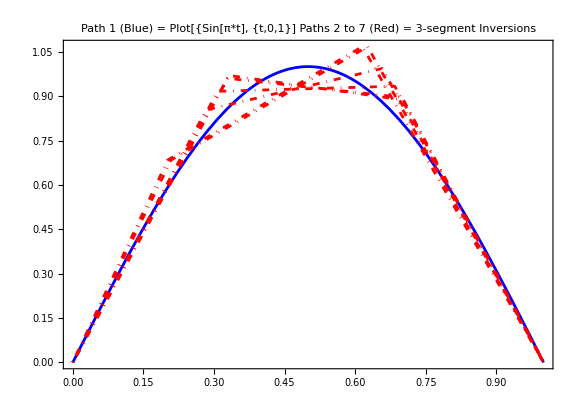

```mathematica
Show[Plot[Sin[π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t], {t,0,1}]
Paths 2 to 7 (Red) = 3-segment Inversions"],16]],
ListLinePlot[ptssol4sint,
PlotStyle->{ {DotDashed,Red}}]]
```

#### Sin[2 π t]

```mathematica
sigsins2fcore=getcore6[sigsins2f,4]
```

{{1,0},{0},{1/(2 π),1/4},{1/(4 π),1/8,0}}

```mathematica
sol4sin2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 t_1)/30458+(20993 t_2)/30458-(27178 t_3)/45687-(71297 β_1)/91374-(173881 β_2)/182748+(11342 β_3)/15229 == 1.

{β_1→-77.68,β_2→2.5292,β_3→-77.68,t_1→0.0158,t_2→0.96847,t_3→0.0158}

```mathematica
sol4sin2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}

```mathematica
sol4sin2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}

```mathematica
sol4sin2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}

```mathematica
sol4sin2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 t_1)/30458+(20993 t_2)/30458-(27178 t_3)/45687-(71297 β_1)/91374-(173881 β_2)/182748+(11342 β_3)/15229 == 1.

{β_1→44.353,β_2→-2.0428,β_3→44.353,t_1→0.022,t_2→0.95597,t_3→0.022}

```mathematica
sol4sin2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}

```mathematica
ptssol4sin2t=Map[flistbetat,{(*sol4sin2ex46,*)sol4sin2ex47,sol4sin2ex48,sol4sin2ex56,(*sol4sin2ex57,*)sol4sin2ex58}]
```

{{{0,0},{0.2203,1.2247},{0.7797,-1.2247},{1.,0.}},{{0,0},{0.2203,1.2247},{0.7797,-1.2247},{1.,0.}},{{0,0},{0.2203,1.2247},{0.7797,-1.2247},{1.,0.}},{{0,0},{0.2203,1.2247},{0.7797,-1.2247},{1.,0.}}}

```mathematica
Map[flengthpathpts[flistbetat[#]]&,{(*sol4sin2ex46,*)sol4sin2ex47,sol4sin2ex48,sol4sin2ex56,(*sol4sin2ex57,*)sol4sin2ex58}]
```

{5.0014,5.0014,5.0014,5.0014}

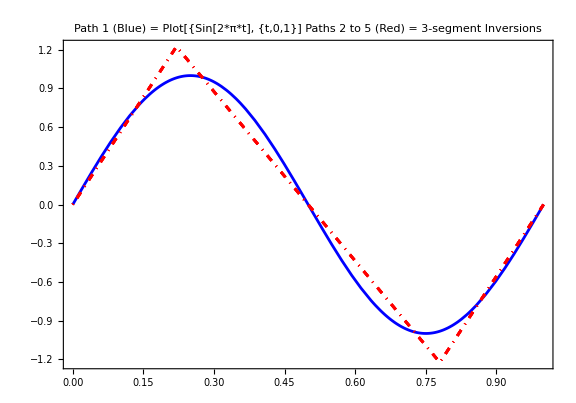

```mathematica
Show[Plot[Sin[2π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t], {t,0,1}]
Paths 2 to 5 (Red) = 3-segment Inversions"],16]],
ListLinePlot[ptssol4sin2t,
PlotStyle->{ {DotDashed,Red}}]]
```

#### Sin[π t^2]

```mathematica
sigsins1f2fcore=getcore6[sigsins1f2,4]
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}

```mathematica
sol4sin1f2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→1.287,β_2→-20.277,β_3→1.6104,t_1→0.86332,t_2→0.0608,t_3→0.075878}

```mathematica
sol4sin1f2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→-32.57,β_2→1.564,β_3→-5.3466,t_1→0.0037518,t_2→0.78851,t_3→0.20774}

```mathematica
sol4sin1f2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
sol4sin1f2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
sol4sin1f2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→-10.055,β_2→1.566,β_3→-5.3478,t_1→0.011166,t_2→0.78108,t_3→0.20776}

```mathematica
sol4sin1f2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
ptssol4sintsq=Map[flistbetat,{sol4sin1f2ex46,sol4sin1f2ex47,(*sol4sin1f2ex48,sol4sin1f2ex56,*)sol4sin1f2ex57(*,sol4sin1f2ex58*)}]
```

{{{0,0},{0.86332,1.111},{0.92412,-0.122},{1.,0.}},{{0,0},{0.0037518,-0.1222},{0.79226,1.111},{1.,0.}},{{0,0},{0.011166,-0.11227},{0.79224,1.111},{1.,0.}}}

```mathematica
Map[flengthpathpts[flistbetat[#]]&,{sol4sin1f2ex46,sol4sin1f2ex47,(*sol4sin1f2ex48,sol4sin1f2ex56,*)sol4sin1f2ex57(*,sol4sin1f2ex58*)}]
```

{2.78,2.716,2.695}

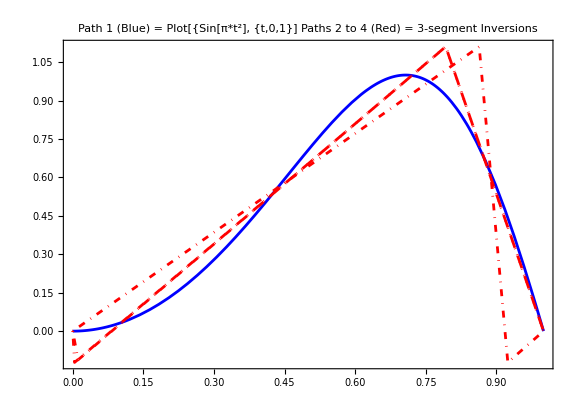

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2], {t,0,1}]
Paths 2 to 4 (Red) = 3-segment Inversions"],16]],
ListLinePlot[ptssol4sintsq,
PlotStyle->{ {DotDashed,Red}}]]
```

#### Sin[π t^2]

```mathematica
sigsins2f2fcore=getcore6[sigsins2f2,4]
```

{{1,0},{-FresnelS[2]/2},{0,1/16 (4-√2 FresnelC[2 √2])},{-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}

```mathematica
sol4sin2f2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
sol4sin2f2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→2.0024,β_2→-10.209,β_3→4.9044,t_1→0.55124,t_2→0.21867,t_3→0.23009}

```mathematica
sol4sin2f2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→1.7897,β_2→-9.98152,β_3→6.74742,t_1→0.58653,t_2→0.2295,t_3→0.18395}

```mathematica
sol4sin2f2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→1.8399,β_2→-23.925,β_3→3.9917,t_1→0.61178,t_2→0.095831,t_3→0.29239}

```mathematica
sol4sin2f2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
sol4sin2f2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6][[1]]
```

{β_1→1.54076,β_2→-7.28173,β_3→18.2845,t_1→0.6106,t_2→0.31529,t_3→0.074109}

```mathematica
ptssol4sin2tsq=Map[flistbetat,{(*sol4sin2f2ex46,*)sol4sin2f2ex47,sol4sin2f2ex48,sol4sin2f2ex56,(*sol4sin2f2ex57,*)sol4sin2f2ex58}]
```

{{{0,0},{0.55124,1.1038},{0.76991,-1.128},{1.,0.}},{{0,0},{0.58653,1.0497},{0.81605,-1.241},{1.,0.}},{{0,0},{0.61178,1.1256},{0.70761,-1.167},{1.,0.}},{{0,0},{0.6106,0.94079},{0.92589,-1.355},{1.,0.}}}

```mathematica
Map[flengthpathpts[flistbetat[#]]&,{(*sol4sin2f2ex46,*)sol4sin2f2ex47,sol4sin2f2ex48,sol4sin2f2ex56,(*sol4sin2f2ex57,*)sol4sin2f2ex58}]
```

{4.628,4.76,4.779,4.796}

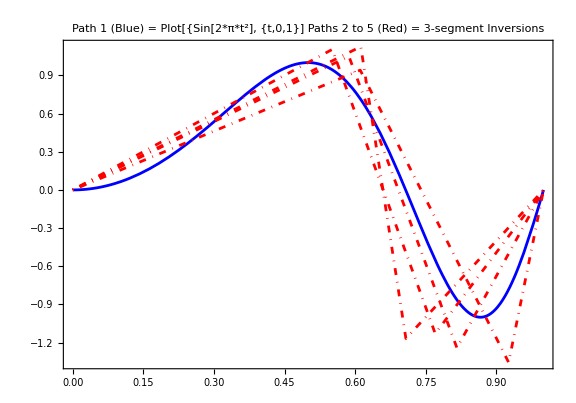

```mathematica
Show[Plot[Sin[2π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t^2], {t,0,1}]
Paths 2 to 5 (Red) = 3-segment Inversions"],16]],
ListLinePlot[ptssol4sin2tsq,
PlotStyle->{ {DotDashed,Red}}]]
```

### d=2, X_1(t)=Y_1(t)=t, 4 lines

```mathematica
dinv=2;
```

```mathematica
signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]]
```

{{1},{t_1,t_1 β_1},{{t_1^2/2,1/2 t_1^2 β_1},{1/2 t_1^2 β_1,1/2 t_1^2 β_1^2}},{{{t_1^3/6,1/6 t_1^3 β_1},{1/6 t_1^3 β_1,1/6 t_1^3 β_1^2}},{{1/6 t_1^3 β_1,1/6 t_1^3 β_1^2},{1/6 t_1^3 β_1^2,1/6 t_1^3 β_1^3}}},{{{{t_1^4/24,1/24 t_1^4 β_1},{1/24 t_1^4 β_1,1/24 t_1^4 β_1^2}},{{1/24 t_1^4 β_1,1/24 t_1^4 β_1^2},{1/24 t_1^4 β_1^2,1/24 t_1^4 β_1^3}}},{{{1/24 t_1^4 β_1,1/24 t_1^4 β_1^2},{1/24 t_1^4 β_1^2,1/24 t_1^4 β_1^3}},{{1/24 t_1^4 β_1^2,1/24 t_1^4 β_1^3},{1/24 t_1^4 β_1^3,1/24 t_1^4 β_1^4}}}},{{{{{t_1^5/120,1/120 t_1^5 β_1},{1/120 t_1^5 β_1,1/120 t_1^5 β_1^2}},{{1/120 t_1^5 β_1,1/120 t_1^5 β_1^2},{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3}}},{{{1/120 t_1^5 β_1,1/120 t_1^5 β_1^2},{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3}},{{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3},{1/120 t_1^5 β_1^3,1/120 t_1^5 β_1^4}}}},{{{{1/120 t_1^5 β_1,1/120 t_1^5 β_1^2},{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3}},{{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3},{1/120 t_1^5 β_1^3,1/120 t_1^5 β_1^4}}},{{{1/120 t_1^5 β_1^2,1/120 t_1^5 β_1^3},{1/120 t_1^5 β_1^3,1/120 t_1^5 β_1^4}},{{1/120 t_1^5 β_1^3,1/120 t_1^5 β_1^4},{1/120 t_1^5 β_1^4,1/120 t_1^5 β_1^5}}}}}}

```mathematica
chen4z5=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},5][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},5][[1]],
signat[{{t,Subscript[β, 4] t}},{0,Subscript[t, 4]},5][[1]]},
5,dinv];
```

```mathematica
chen4z5core={{sigtake[chen4z5,{1}],sigtake[chen4z5,{2}]},
{sigtake[chen4z5,{1,2}]},
{sigtake[chen4z5,{1,1,2}],sigtake[chen4z5,{1,2,2}]},
{sigtake[chen4z5,{1,1,1,2}],sigtake[chen4z5,{1,1,2,2}],sigtake[chen4z5,{1,2,2,2}]},
{sigtake[chen4z5,{1,1,1,1,2}],sigtake[chen4z5,{1,1,1,2,2}],sigtake[chen4z5,{1,1,2,1,2}],sigtake[chen4z5,{1,1,2,2,2}],sigtake[chen4z5,{1,2,1,2,2}],sigtake[chen4z5,{1,2,2,2,2}]}};
```

```mathematica
vars4linechen={Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[β, 4],Subscript[t, 1],Subscript[t, 2],Subscript[t, 3],Subscript[t, 4]};
```

```mathematica
eqs4linechen2345=MapThread[Equal,{
Expand[Flatten[chen4z5core]],
{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2]}}];
```

```mathematica
cores5={Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2]};
```

```mathematica
solve4lines[eqsleft_,cores_,vars_,delpos_:{},bounds_:{}]:=Module[{eqs},
eqs=MapThread[Equal,{eqsleft,cores}];
NSolve[Join[Delete[eqs,delpos],bounds],vars,Reals]];
```

```mathematica
fpw4[sollist_,t_]:=Module[{β1,β2,β3,β4,t1,t2,t3,t4},
{β1,β2,β3,β4,t1,t2,t3,t4}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤(t1+t2)}, {β1 t1+β2 t2+β3(t-(t1+t2)), (t1+t2)<t≤(t1+t2+t3)}, {β1 t1+β2 t2+β3 t3+β4(t-(t1+t2+t3)), (t1+t2+t3)<t≤(t1+t2+t3+t4)}}]];
```

```mathematica
sigsins1f2;
```

```mathematica
sigsins1f2fcore5={{sigtake[sigsins1f2,{1}],sigtake[sigsins1f2,{2}]},
{sigtake[sigsins1f2,{1,2}]},
{sigtake[sigsins1f2,{1,1,2}],sigtake[sigsins1f2,{1,2,2}]},
{sigtake[sigsins1f2,{1,1,1,2}],sigtake[sigsins1f2,{1,1,2,2}],sigtake[sigsins1f2,{1,2,2,2}]},
{sigtake[sigsins1f2,{1,1,1,1,2}],sigtake[sigsins1f2,{1,1,1,2,2}],sigtake[sigsins1f2,{1,1,2,1,2}],sigtake[sigsins1f2,{1,1,2,2,2}],sigtake[sigsins1f2,{1,2,1,2,2}],sigtake[sigsins1f2,{1,2,2,2,2}]}};
```

```mathematica
sigsins1f2fcore5
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{-1/(12 π),1/24+FresnelS[2]/(64 π),-(8 π+15 FresnelS[2]-24 √2 FresnelS[√2])/(96 π),-1/(9 π),Integrate[1/4 Cos[π t_5^2] t_5 (-3 Sin[2 π t_5^2]-4 Sin[π t_5^2] (-2+√2 π FresnelS[√2 t_5] t_5)+2 π (FresnelS[√2 t_5]^2-t_5^2)),{t_5,0,1},Assumptions→0≤t_1≤1&&0≤t_2≤1&&0≤t_3≤1&&0≤t_4≤1&&0≤t_5≤1],1/768 (12-8 FresnelC[2]+√2 FresnelC[2 √2])}}

```mathematica
NIntegrate[1/4 Cos[π Subscript[t, 5]^2] Subscript[t, 5] (-3 Sin[2 π Subscript[t, 5]^2]-4 Sin[π Subscript[t, 5]^2] (-2+√2 π FresnelS[√2 Subscript[t, 5]] Subscript[t, 5])+2 π (FresnelS[√2 Subscript[t, 5]]^2-Subscript[t, 5]^2)),{Subscript[t, 5],0,1}]
```

0.0546304

```mathematica
sigsins1f2fcore5N={{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{-1/(12 π),1/24+FresnelS[2]/(64 π),-(8 π+15 FresnelS[2]-24 √2 FresnelS[√2])/(96 π),-1/(9 π),0.0546304224360678,1/768 (12-8 FresnelC[2]+√2 FresnelC[2 √2])}}
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{-1/(12 π),1/24+FresnelS[2]/(64 π),-(8 π+15 FresnelS[2]-24 √2 FresnelS[√2])/(96 π),-1/(9 π),0.0546304,1/768 (12-8 FresnelC[2]+√2 FresnelC[2 √2])}}

```mathematica
Timing[solN4lindirect0=solve3lines[Expand[Flatten[chen4z5core]],Flatten[sigsins1f2fcore5N],vars4linechen,
{{5},{8},{10},{12},{13},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0}]]
```

{573.399,{{β_1→0.367259,β_2→2.00438,β_3→-1.52412,β_4→-5.81245,t_1→0.187113,t_2→0.490988,t_3→0.190792,t_4→0.131107}}}

```mathematica
Map[Last,{Subscript[β, 1]->0.3672591327051559,Subscript[β, 2]->2.0043753423057216,Subscript[β, 3]->-1.524119876148797,Subscript[β, 4]->-5.812454210443576,Subscript[t, 1]->0.18711327751603507,Subscript[t, 2]->0.4909875450174028,Subscript[t, 3]->0.19079245622954283,Subscript[t, 4]->0.13110672123701936}]
```

{0.367259,2.00438,-1.52412,-5.81245,0.187113,0.490988,0.190792,0.131107}

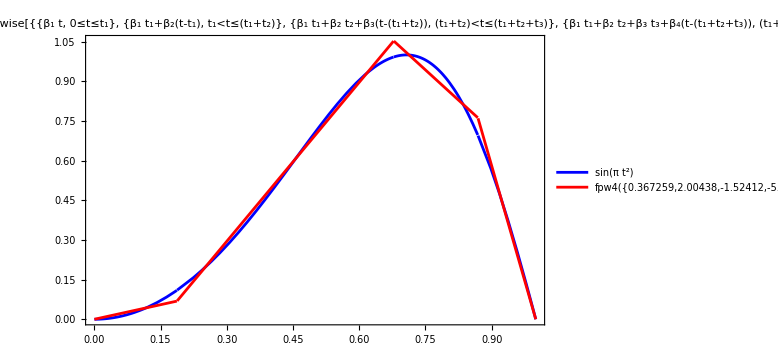

```mathematica
Plot[{Sin[π t^2],
fpw4[{0.3672591327051559,2.0043753423057216,-1.524119876148797,-5.812454210443576,0.18711327751603507,0.4909875450174028,0.19079245622954283,0.13110672123701936},t]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π*t^2] ,
Path 2 = Piecewise[{{β_1 t, 0≤t≤t_1}, {β_1 t_1+β_2(t-t_1), t_1<t≤(t_1+t_2)}, {β_1 t_1+β_2 t_2+β_3(t-(t_1+t_2)), (t_1+t_2)<t≤(t_1+t_2+t_3)}, {β_1 t_1+β_2 t_2+β_3 t_3+β_4(t-(t_1+t_2+t_3)), (t_1+t_2+t_3)<t≤1}}] 
}, {t,0,1}]"],16]]
```

```mathematica
sigsins2f2fcore5={{sigtake[sigsins2f2,{1}],sigtake[sigsins2f2,{2}]},
{sigtake[sigsins2f2,{1,2}]},
{sigtake[sigsins2f2,{1,1,2}],sigtake[sigsins2f2,{1,2,2}]},
{sigtake[sigsins2f2,{1,1,1,2}],sigtake[sigsins2f2,{1,1,2,2}],sigtake[sigsins2f2,{1,2,2,2}]},
{sigtake[sigsins2f2,{1,1,1,1,2}],sigtake[sigsins2f2,{1,1,1,2,2}],sigtake[sigsins2f2,{1,1,2,1,2}],sigtake[sigsins2f2,{1,1,2,2,2}],sigtake[sigsins2f2,{1,2,1,2,2}],sigtake[sigsins2f2,{1,2,2,2,2}]}};
```

```mathematica
sigsins2f2fcore5
```

{{1,0},{-FresnelS[2]/2},{0,1/16 (4-√2 FresnelC[2 √2])},{-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/(24 π),1/768 (32+(3 √2 FresnelS[2 √2])/π),-(32 π-48 FresnelS[2]+15 √2 FresnelS[2 √2])/(384 π),0,Integrate[1/4 Cos[2 π t_5^2] t_5 (-3 Sin[4 π t_5^2]-8 Sin[2 π t_5^2] (-1+π FresnelS[2 t_5] t_5)+2 π (FresnelS[2 t_5]^2-2 t_5^2)),{t_5,0,1},Assumptions→0≤t_1≤1&&0≤t_2≤1&&0≤t_3≤1&&0≤t_4≤1&&0≤t_5≤1],1/768 (12+FresnelC[4]-4 √2 FresnelC[2 √2])}}

```mathematica
NIntegrate[1/4 Cos[2 π Subscript[t, 5]^2] Subscript[t, 5] (-3 Sin[4 π Subscript[t, 5]^2]-8 Sin[2 π Subscript[t, 5]^2] (-1+π FresnelS[2 Subscript[t, 5]] Subscript[t, 5])+2 π (FresnelS[2 Subscript[t, 5]]^2-2 Subscript[t, 5]^2)),{Subscript[t, 5],0,1}]
```

-0.0448062

```mathematica
sigsins2f2fcore5N={{1,0},{-FresnelS[2]/2},{0,1/16 (4-√2 FresnelC[2 √2])},{-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/(24 π),1/768 (32+(3 √2 FresnelS[2 √2])/π),-(32 π-48 FresnelS[2]+15 √2 FresnelS[2 √2])/(384 π),0,-0.04480624557257676,1/768 (12+FresnelC[4]-4 √2 FresnelC[2 √2])}}
```

{{1,0},{-FresnelS[2]/2},{0,1/16 (4-√2 FresnelC[2 √2])},{-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/(24 π),1/768 (32+(3 √2 FresnelS[2 √2])/π),-(32 π-48 FresnelS[2]+15 √2 FresnelS[2 √2])/(384 π),0,-0.0448062,1/768 (12+FresnelC[4]-4 √2 FresnelC[2 √2])}}

```mathematica
Timing[solN4lindirect1=solve3lines[Expand[Flatten[chen4z5core]],Flatten[sigsins2f2fcore5N],vars4linechen,
{{5},{8},{10},{12},{13},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0}]]
```

{546.068,{{β_1→0.606296,β_2→2.89647,β_3→-6.43566,β_4→10.8239,t_1→0.144742,t_2→0.375215,t_3→0.369099,t_4→0.110943}}}

```mathematica
Map[Last,{Subscript[β, 1]->0.6062955763138922,Subscript[β, 2]->2.896473190595218,Subscript[β, 3]->-6.435656503531899,Subscript[β, 4]->10.823920075724823,Subscript[t, 1]->0.1447422168205849,Subscript[t, 2]->0.3752152060147192,Subscript[t, 3]->0.3690994277647256,Subscript[t, 4]->0.11094314939997016}]
```

{0.606296,2.89647,-6.43566,10.8239,0.144742,0.375215,0.369099,0.110943}

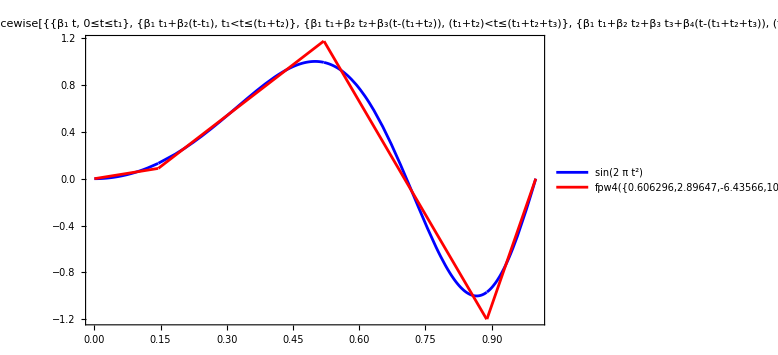

```mathematica
Plot[{Sin[2π t^2],
fpw4[{0.6062955763138922,2.896473190595218,-6.435656503531899,10.823920075724823,0.1447422168205849,0.3752152060147192,0.3690994277647256,0.11094314939997016},t]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[2*π*t^2] ,
Path 2 = Piecewise[{{β_1 t, 0≤t≤t_1}, {β_1 t_1+β_2(t-t_1), t_1<t≤(t_1+t_2)}, {β_1 t_1+β_2 t_2+β_3(t-(t_1+t_2)), (t_1+t_2)<t≤(t_1+t_2+t_3)}, {β_1 t_1+β_2 t_2+β_3 t_3+β_4(t-(t_1+t_2+t_3)), (t_1+t_2+t_3)<t≤1}}] 
}, {t,0,1}]"],16]]
```

### d=2

```mathematica
dinv=2;
```

```mathematica
signat[{{Subscript[α, 1] t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]]
```

{{1},{t_1 α_1,t_1 β_1},{{1/2 t_1^2 α_1^2,1/2 t_1^2 α_1 β_1},{1/2 t_1^2 α_1 β_1,1/2 t_1^2 β_1^2}},{{{1/6 t_1^3 α_1^3,1/6 t_1^3 α_1^2 β_1},{1/6 t_1^3 α_1^2 β_1,1/6 t_1^3 α_1 β_1^2}},{{1/6 t_1^3 α_1^2 β_1,1/6 t_1^3 α_1 β_1^2},{1/6 t_1^3 α_1 β_1^2,1/6 t_1^3 β_1^3}}},{{{{1/24 t_1^4 α_1^4,1/24 t_1^4 α_1^3 β_1},{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2}},{{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2},{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3}}},{{{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2},{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3}},{{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3},{1/24 t_1^4 α_1 β_1^3,1/24 t_1^4 β_1^4}}}},{{{{{1/120 t_1^5 α_1^5,1/120 t_1^5 α_1^4 β_1},{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2}},{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}}},{{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}},{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}}}},{{{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}},{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}}},{{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}},{{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4},{1/120 t_1^5 α_1 β_1^4,1/120 t_1^5 β_1^5}}}}}}

```mathematica
signat[{{a t,b t}},{0,1},5][[1]]
```

{{1},{a,b},{{a^2/2,(a b)/2},{(a b)/2,b^2/2}},{{{a^3/6,(a^2 b)/6},{(a^2 b)/6,(a b^2)/6}},{{(a^2 b)/6,(a b^2)/6},{(a b^2)/6,b^3/6}}},{{{{a^4/24,(a^3 b)/24},{(a^3 b)/24,(a^2 b^2)/24}},{{(a^3 b)/24,(a^2 b^2)/24},{(a^2 b^2)/24,(a b^3)/24}}},{{{(a^3 b)/24,(a^2 b^2)/24},{(a^2 b^2)/24,(a b^3)/24}},{{(a^2 b^2)/24,(a b^3)/24},{(a b^3)/24,b^4/24}}}},{{{{{a^5/120,(a^4 b)/120},{(a^4 b)/120,(a^3 b^2)/120}},{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}}},{{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}},{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}}}},{{{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}},{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}}},{{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}},{{(a^2 b^3)/120,(a b^4)/120},{(a b^4)/120,b^5/120}}}}}}

d=2 - Chen

```mathematica
chen2z3=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},3][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},3][[1]]},
3,dinv];
```

```mathematica
chen2z3core={{sigtake[chen2z3,{1}],sigtake[chen2z3,{2}]},
{sigtake[chen2z3,{1,2}]},
{sigtake[chen2z3,{1,1,2}],sigtake[chen2z3,{1,2,2}]}};
```

```mathematica
chen3z4=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},4][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},4][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},4][[1]]},
4,dinv];
```

```mathematica
chen3z4core={{sigtake[chen3z4,{1}],sigtake[chen3z4,{2}]},
{sigtake[chen3z4,{1,2}]},
{sigtake[chen3z4,{1,1,2}],sigtake[chen3z4,{1,2,2}]},
{sigtake[chen3z4,{1,1,1,2}],sigtake[chen3z4,{1,1,2,2}],sigtake[chen3z4,{1,2,2,2}]}};
```

```mathematica
chen4z5=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},5][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},5][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},5][[1]],
signat[{{Subscript[a, 4] t,Subscript[b, 4] t}},{0,1},5][[1]]},
5,dinv];
```

```mathematica
chen4z5core={{sigtake[chen4z5,{1}],sigtake[chen4z5,{2}]},
{sigtake[chen4z5,{1,2}]},
{sigtake[chen4z5,{1,1,2}],sigtake[chen4z5,{1,2,2}]},
{sigtake[chen4z5,{1,1,1,2}],sigtake[chen4z5,{1,1,2,2}],sigtake[chen4z5,{1,2,2,2}]},
{sigtake[chen4z5,{1,1,1,1,2}],sigtake[chen4z5,{1,1,1,2,2}],sigtake[chen4z5,{1,1,2,1,2}],sigtake[chen4z5,{1,1,2,2,2}],sigtake[chen4z5,{1,2,1,2,2}],sigtake[chen4z5,{1,2,2,2,2}]}};
```

```mathematica
chen5z5=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},5][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},5][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},5][[1]],
signat[{{Subscript[a, 4] t,Subscript[b, 4] t}},{0,1},5][[1]],
signat[{{Subscript[a, 5] t,Subscript[b, 5] t}},{0,1},5][[1]]},
5,dinv];
```

```mathematica
chen5z5core={{sigtake[chen5z5,{1}],sigtake[chen5z5,{2}]},
{sigtake[chen5z5,{1,2}]},
{sigtake[chen5z5,{1,1,2}],sigtake[chen5z5,{1,2,2}]},
{sigtake[chen5z5,{1,1,1,2}],sigtake[chen5z5,{1,1,2,2}],sigtake[chen5z5,{1,2,2,2}]},
{sigtake[chen5z5,{1,1,1,1,2}],sigtake[chen5z5,{1,1,1,2,2}],sigtake[chen5z5,{1,1,2,1,2}],sigtake[chen5z5,{1,1,2,2,2}],sigtake[chen5z5,{1,2,1,2,2}],sigtake[chen5z5,{1,2,2,2,2}]}};
```

```mathematica
chen5z6=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},6][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},6][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},6][[1]],
signat[{{Subscript[a, 4] t,Subscript[b, 4] t}},{0,1},6][[1]],
signat[{{Subscript[a, 5] t,Subscript[b, 5] t}},{0,1},6][[1]]},
6,dinv];
```

```mathematica
chen5z6core={{sigtake[chen5z6,{1}],sigtake[chen5z6,{2}]},
{sigtake[chen5z6,{1,2}]},
{sigtake[chen5z6,{1,1,2}],sigtake[chen5z6,{1,2,2}]},
{sigtake[chen5z6,{1,1,1,2}],sigtake[chen5z6,{1,1,2,2}],sigtake[chen5z6,{1,2,2,2}]},
{sigtake[chen5z6,{1,1,1,1,2}],sigtake[chen5z6,{1,1,1,2,2}],sigtake[chen5z6,{1,1,2,1,2}],sigtake[chen5z6,{1,1,2,2,2}],sigtake[chen5z6,{1,2,1,2,2}],sigtake[chen5z6,{1,2,2,2,2}]},
{sigtake[chen5z6,{1,1,1,1,1,2}],sigtake[chen5z6,{1,1,1,1,2,2}],sigtake[chen5z6,{1,1,1,2,1,2}],sigtake[chen5z6,{1,1,1,2,2,2}],sigtake[chen5z6,{1,1,2,1,2,2}],sigtake[chen5z6,{1,1,2,2,1,2}],sigtake[chen5z6,{1,1,2,2,2,2}],sigtake[chen5z6,{1,2,1,2,2,2}],sigtake[chen5z6,{1,2,2,2,2,2}]}};
```

d=2 - Vars

```mathematica
vars2line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[b, 1],Subscript[b, 2]};
```

```mathematica
vars3line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]};
```

```mathematica
vars4line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]};
```

```mathematica
vars5line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4],Subscript[b, 5]};
```

```mathematica
cores3={
Subscript[z, 1],Subscript[z, 2],
Subscript[z, 1,2],
Subscript[z, 1,1,2],Subscript[z, 1,2,2]};
```

```mathematica
cores4={
Subscript[z, 1],Subscript[z, 2],
Subscript[z, 1,2],
Subscript[z, 1,1,2],Subscript[z, 1,2,2],
Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]};
```

```mathematica
cores5={
Subscript[z, 1],Subscript[z, 2],
Subscript[z, 1,2],
Subscript[z, 1,1,2],Subscript[z, 1,2,2],
Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],
Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2]};
```

```mathematica
cores6={
Subscript[z, 1],Subscript[z, 2],
Subscript[z, 1,2],
Subscript[z, 1,1,2],Subscript[z, 1,2,2],
Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],
Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2],
Subscript[z, 1,1,1,1,1,2],Subscript[z, 1,1,1,1,2,2],Subscript[z, 1,1,1,2,1,2],Subscript[z, 1,1,1,2,2,2],Subscript[z, 1,1,2,1,2,2],Subscript[z, 1,1,2,2,1,2],Subscript[z, 1,1,2,2,2,2],Subscript[z, 1,2,1,2,2,2],Subscript[z, 1,2,2,2,2,2]};
```

```mathematica
eqs5lineschen23456=MapThread[Equal,{Expand[Flatten[chen5z6core]],cores6}];
```

```mathematica
solve5lines[eqsleft_,cores_,vars_,delpos_:{},bounds_:{}]:=Module[{eqs},
eqs=MapThread[Equal,{eqsleft,cores}];
NSolve[Join[Delete[eqs,delpos],bounds],vars,Reals]];
```

```mathematica
fpw5[sollist_,t_]:=Module[{α1,α2,α3,α4,α5,β1,β2,β3,β4,β5,t1,t2,t3,t4,t5},
{α1,α2,α3,α4,α5,β1,β2,β3,β4,β5,t1,t2,t3,t4,t5}=sollist;
Piecewise[{{{α1 t,β1 t}, 0≤t≤t1}, {{α1 t1+α2(t-t1),β1 t1+β2(t-t1)}, t1<t≤(t1+t2)}, {{α1 t1+α2 t2+α3(t-(t1+t2)),β1 t1+β2 t2+β3(t-(t1+t2))}, (t1+t2)<t≤(t1+t2+t3)}, {{α1 t1+α2 t2+α3 t3+α4(t-(t1+t2+t3)),β1 t1+β2 t2+β3 t3+β4(t-(t1+t2+t3))}, (t1+t2+t3)<t≤(t1+t2+t3+t4)}, {{α1 t1+α2 t2+α3 t3+α4 t4+α5(t-(t1+t2+t3+t4)),β1 t1+β2 t2+β3 t3+β4 t4+β5(t-(t1+t2+t3+t4))}, (t1+t2+t3+t4)<t≤(t1+t2+t3+t4+t5)}}]];
```

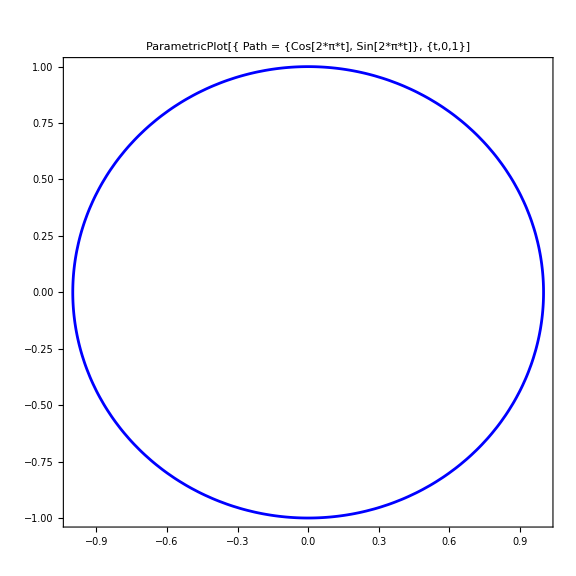

```mathematica
ParametricPlot[{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path = {Cos[2*π*t], Sin[2*π*t]},
 {t,0,1}]"],16]]
```

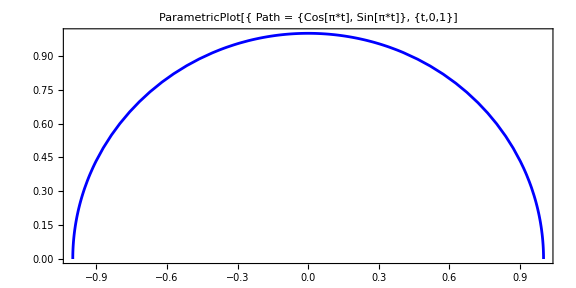

```mathematica
ParametricPlot[{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1/2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path = {Cos[π*t], Sin[π*t]},
 {t,0,1}]"],16]]
```

```mathematica
digit5=({{0, 0}, {20, -3}, {64, 13}, {79, 47}, {35, 54}, {37, 77}, {71, 96}, {100, 93}})
```

{{0,0},{20,-3},{64,13},{79,47},{35,54},{37,77},{71,96},{100,93}}

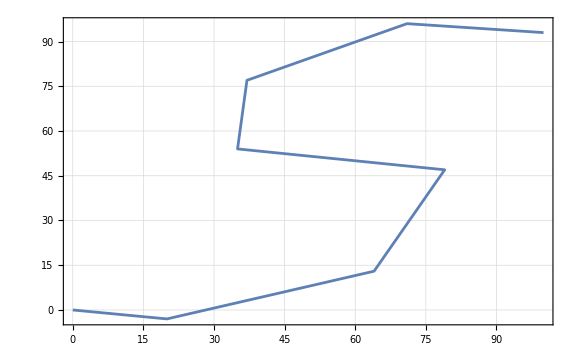

```mathematica
ListLinePlot[digit5,ImageSize->Large,GridLines->Automatic,Frame->True]
```

```mathematica
Differences[digit5]
```

{{20,-3},{44,16},{15,34},{-44,7},{2,23},{34,19},{29,-3}}

```mathematica
chendigit5l6=chainchen[Map[(signat[{#*t},{0,1},6][[1]])&,Differences[digit5]],6,dinv];
```

```mathematica
digit5core6={{sigtake[chendigit5l6,{1}],sigtake[chendigit5l6,{2}]},
{sigtake[chendigit5l6,{1,2}]},
{sigtake[chendigit5l6,{1,1,2}],sigtake[chendigit5l6,{1,2,2}]},
{sigtake[chendigit5l6,{1,1,1,2}],sigtake[chendigit5l6,{1,1,2,2}],sigtake[chendigit5l6,{1,2,2,2}]},
{sigtake[chendigit5l6,{1,1,1,1,2}],sigtake[chendigit5l6,{1,1,1,2,2}],sigtake[chendigit5l6,{1,1,2,1,2}],sigtake[chendigit5l6,{1,1,2,2,2}],sigtake[chendigit5l6,{1,2,1,2,2}],sigtake[chendigit5l6,{1,2,2,2,2}]},
{sigtake[chendigit5l6,{1,1,1,1,1,2}],sigtake[chendigit5l6,{1,1,1,1,2,2}],sigtake[chendigit5l6,{1,1,1,2,1,2}],sigtake[chendigit5l6,{1,1,1,2,2,2}],sigtake[chendigit5l6,{1,1,2,1,2,2}],sigtake[chendigit5l6,{1,1,2,2,1,2}],sigtake[chendigit5l6,{1,1,2,2,2,2}],sigtake[chendigit5l6,{1,2,1,2,2,2}],sigtake[chendigit5l6,{1,2,2,2,2,2}]}}
```

{{100,93},{10139/2},{440461/3,505767/2},{71967937/24,62070307/8,191264681/24},{715742579/15,670296411/4,-648755657/6,2440364507/10,-1063111129/30,1468494543/8},{49654623027/80,338328280853/120,-27651091731/10,377183167163/72,-133085302771/72,-21745844315/9,1320182612489/240,21385676703/80,2411176851929/720}}

```mathematica
digit5core5=Drop[digit5core6,-1]
```

{{100,93},{10139/2},{440461/3,505767/2},{71967937/24,62070307/8,191264681/24},{715742579/15,670296411/4,-648755657/6,2440364507/10,-1063111129/30,1468494543/8}}

```mathematica
digit5core4=Drop[digit5core5,-1]
```

{{100,93},{10139/2},{440461/3,505767/2},{71967937/24,62070307/8,191264681/24}}

```mathematica
digit5core3=Drop[digit5core4,-1]
```

{{100,93},{10139/2},{440461/3,505767/2}}

```mathematica
Timing[sigsemicircle5=signat[{{Cos[π t],Sin[π t]}},{0,1},5][[1]]]
```

{112.346,{{1},{-2,0},{{2,π/2},{-π/2,0}},{{{-4/3,-π/2},{0,-2/3}},{{π/2,4/3},{-2/3,0}}},{{{{2/3,(5 π)/16},{π/16,2/3}},{{-π/16,-4/3+π^2/8},{4/3-π^2/8,π/16}}},{{{-(5 π)/16,-π^2/8},{-4/3+π^2/8,-(3 π)/16}},{{2/3,(3 π)/16},{-π/16,0}}}},{{{{{-4/15,-(7 π)/48},{-π/24,-2/5}},{{0,52/45-π^2/8},{-58/45+π^2/8,-π/16}}},{{{π/24,-16/15+π^2/8},{112/45-π^2/4,π/48}},{{-58/45+π^2/8,-π/48},{0,-2/45}}}},{{{{(7 π)/48,32/45},{-16/15+π^2/8,π/6}},{{52/45-π^2/8,0},{π/48,8/45}}},{{{-2/5,-π/6},{-π/48,-4/15}},{{π/16,8/45},{-2/45,0}}}}}}}

```mathematica
Timing[sigcircle5=signat[{{Cos[2π t],Sin[2π t]}},{0,1},5][[1]]]
```

{120.63,{{1},{0,0},{{0,π},{-π,0}},{{{0,-π},{2 π,0}},{{-π,0},{0,0}}},{{{{0,(5 π)/8},{-(15 π)/8,0}},{{(15 π)/8,π^2/2},{-π^2/2,π/8}}},{{{-(5 π)/8,-π^2/2},{π^2/2,-(3 π)/8}},{{0,(3 π)/8},{-π/8,0}}}},{{{{{0,-(7 π)/24},{(7 π)/6,0}},{{-(7 π)/4,-π^2/2},{π^2/2,-π/8}}},{{{(7 π)/6,π^2/2},{0,(17 π)/24}},{{-π^2/2,-(11 π)/8},{(11 π)/12,0}}}},{{{{-(7 π)/24,0},{-π^2/2,-π/3}},{{π^2/2,(4 π)/3},{-(11 π)/8,0}}},{{{0,-π/3},{(17 π)/24,0}},{{-π/8,0},{0,0}}}}}}}

```mathematica
Timing[sigcircle6=signat[{{Cos[2π t],Sin[2π t]}},{0,1},6][[1]]]
```

{450.893,{{1},{0,0},{{0,π},{-π,0}},{{{0,-π},{2 π,0}},{{-π,0},{0,0}}},{{{{0,(5 π)/8},{-(15 π)/8,0}},{{(15 π)/8,π^2/2},{-π^2/2,π/8}}},{{{-(5 π)/8,-π^2/2},{π^2/2,-(3 π)/8}},{{0,(3 π)/8},{-π/8,0}}}},{{{{{0,-(7 π)/24},{(7 π)/6,0}},{{-(7 π)/4,-π^2/2},{π^2/2,-π/8}}},{{{(7 π)/6,π^2/2},{0,(17 π)/24}},{{-π^2/2,-(11 π)/8},{(11 π)/12,0}}}},{{{{-(7 π)/24,0},{-π^2/2,-π/3}},{{π^2/2,(4 π)/3},{-(11 π)/8,0}}},{{{0,-π/3},{(17 π)/24,0}},{{-π/8,0},{0,0}}}}},{{{{{{0,(7 π)/64},{-(35 π)/64,0}},{{(35 π)/32,(5 π^2)/16},{-(5 π^2)/16,(7 π)/96}}},{{{-(35 π)/32,-(7 π^2)/16},{-π^2/16,-(21 π)/32}},{{π^2/2,(259 π)/192},{-(175 π)/192,0}}}},{{{{(35 π)/64,π^2/4},{π^2/8,(119 π)/192}},{{-π^2/16,-(7 π)/4+π^3/6},{(175 π)/96-π^3/6,π^2/16}}},{{{-(5 π^2)/16,(7 π)/16-π^3/6},{1/96 π (-175+16 π^2),-(3 π^2)/16}},{{(175 π)/192,π^2/4},{-π^2/8,π/192}}}}},{{{{{-(7 π)/64,-π^2/8},{π^2/4,-(35 π)/192}},{{-(7 π^2)/16,(35 π)/96-π^3/6},{1/48 π (-21+8 π^2),-π^2/16}}},{{{(5 π^2)/16,1/96 π (-35+16 π^2)},{(7 π)/4-π^3/6,(3 π^2)/16}},{{-(259 π)/192,-(3 π^2)/8},{π^2/4,-(5 π)/192}}}},{{{{0,(35 π)/192},{-(119 π)/192,0}},{{(21 π)/32,(3 π^2)/16},{-(3 π^2)/16,(5 π)/96}}},{{{-(7 π)/96,-π^2/16},{π^2/16,-(5 π)/96}},{{0,(5 π)/192},{-π/192,0}}}}}}}}

```mathematica
semicirclecore3={{sigtake[sigsemicircle5,{1}],sigtake[sigsemicircle5,{2}]},
{sigtake[sigsemicircle5,{1,2}]},
{sigtake[sigsemicircle5,{1,1,2}],sigtake[sigsemicircle5,{1,2,2}]}}
```

{{-2,0},{π/2},{-π/2,-2/3}}

```mathematica
semicirclecore4={{sigtake[sigsemicircle5,{1}],sigtake[sigsemicircle5,{2}]},
{sigtake[sigsemicircle5,{1,2}]},
{sigtake[sigsemicircle5,{1,1,2}],sigtake[sigsemicircle5,{1,2,2}]},
{sigtake[sigsemicircle5,{1,1,1,2}],sigtake[sigsemicircle5,{1,1,2,2}],sigtake[sigsemicircle5,{1,2,2,2}]}}
```

{{-2,0},{π/2},{-π/2,-2/3},{(5 π)/16,2/3,π/16}}

```mathematica
circlecore4={{sigtake[sigcircle5,{1}],sigtake[sigcircle5,{2}]},
{sigtake[sigcircle5,{1,2}]},
{sigtake[sigcircle5,{1,1,2}],sigtake[sigcircle5,{1,2,2}]},
{sigtake[sigcircle5,{1,1,1,2}],sigtake[sigcircle5,{1,1,2,2}],sigtake[sigcircle5,{1,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8}}

```mathematica
semicirclecore5={{sigtake[sigsemicircle5,{1}],sigtake[sigsemicircle5,{2}]},
{sigtake[sigsemicircle5,{1,2}]},
{sigtake[sigsemicircle5,{1,1,2}],sigtake[sigsemicircle5,{1,2,2}]},
{sigtake[sigsemicircle5,{1,1,1,2}],sigtake[sigsemicircle5,{1,1,2,2}],sigtake[sigsemicircle5,{1,2,2,2}]},
{sigtake[sigsemicircle5,{1,1,1,1,2}],sigtake[sigsemicircle5,{1,1,1,2,2}],sigtake[sigsemicircle5,{1,1,2,1,2}],sigtake[sigsemicircle5,{1,1,2,2,2}],sigtake[sigsemicircle5,{1,2,1,2,2}],sigtake[sigsemicircle5,{1,2,2,2,2}]}}
```

{{-2,0},{π/2},{-π/2,-2/3},{(5 π)/16,2/3,π/16},{-(7 π)/48,-2/5,52/45-π^2/8,-π/16,π/48,-2/45}}

```mathematica
circlecore5={{sigtake[sigcircle5,{1}],sigtake[sigcircle5,{2}]},
{sigtake[sigcircle5,{1,2}]},
{sigtake[sigcircle5,{1,1,2}],sigtake[sigcircle5,{1,2,2}]},
{sigtake[sigcircle5,{1,1,1,2}],sigtake[sigcircle5,{1,1,2,2}],sigtake[sigcircle5,{1,2,2,2}]},
{sigtake[sigcircle5,{1,1,1,1,2}],sigtake[sigcircle5,{1,1,1,2,2}],sigtake[sigcircle5,{1,1,2,1,2}],sigtake[sigcircle5,{1,1,2,2,2}],sigtake[sigcircle5,{1,2,1,2,2}],sigtake[sigcircle5,{1,2,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
circlecore6={{sigtake[sigcircle6,{1}],sigtake[sigcircle6,{2}]},
{sigtake[sigcircle6,{1,2}]},
{sigtake[sigcircle6,{1,1,2}],sigtake[sigcircle6,{1,2,2}]},
{sigtake[sigcircle6,{1,1,1,2}],sigtake[sigcircle6,{1,1,2,2}],sigtake[sigcircle6,{1,2,2,2}]},
{sigtake[sigcircle6,{1,1,1,1,2}],sigtake[sigcircle6,{1,1,1,2,2}],sigtake[sigcircle6,{1,1,2,1,2}],sigtake[sigcircle6,{1,1,2,2,2}],sigtake[sigcircle6,{1,2,1,2,2}],sigtake[sigcircle6,{1,2,2,2,2}]},
{sigtake[sigcircle6,{1,1,1,1,1,2}],sigtake[sigcircle6,{1,1,1,1,2,2}],sigtake[sigcircle6,{1,1,1,2,1,2}],sigtake[sigcircle6,{1,1,1,2,2,2}],sigtake[sigcircle6,{1,1,2,1,2,2}],sigtake[sigcircle6,{1,1,2,2,1,2}],sigtake[sigcircle6,{1,1,2,2,2,2}],sigtake[sigcircle6,{1,2,1,2,2,2}],sigtake[sigcircle6,{1,2,2,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0},{(7 π)/64,0,(5 π^2)/16,(7 π)/96,-(21 π)/32,(259 π)/192,0,π^2/16,π/192}}

```mathematica
{Length[Flatten[chen3z4core]],Length[Flatten[circlecore4]],Length[vars3line2dchen]}
```

{8,8,6}

```mathematica
{Length[Flatten[chen4z5core]],Length[Flatten[circlecore5]],Length[vars4line2dchen]}
```

{14,14,8}

```mathematica
{Length[Flatten[chen5z6core]],Length[Flatten[circlecore6]],Length[vars5line2dchen]}
```

{23,23,10}

```mathematica
eqs3lineschen2345=MapThread[Equal,{Expand[Flatten[chen3z5core]],Flatten[circlecore5]}];
```

```mathematica
eqs4lineschen2345=MapThread[Equal,{Expand[Flatten[chen4z5core]],Flatten[circlecore5]}];
```

```mathematica
Grid[Transpose[{eqs3lineschen2345}],Frame->All]
```

t_1 α_1+t_2 α_2+t_3 α_3==0
t_1 β_1+t_2 β_2+t_3 β_3==0
1/2 t_1^2 α_1 β_1+t_1 t_2 α_1 β_2+1/2 t_2^2 α_2 β_2+t_1 t_3 α_1 β_3+t_2 t_3 α_2 β_3+1/2 t_3^2 α_3 β_3==π
1/6 t_1^3 α_1^2 β_1+1/2 t_1^2 t_2 α_1^2 β_2+1/2 t_1 t_2^2 α_1 α_2 β_2+1/6 t_2^3 α_2^2 β_2+1/2 t_1^2 t_3 α_1^2 β_3+t_1 t_2 t_3 α_1 α_2 β_3+1/2 t_2^2 t_3 α_2^2 β_3+1/2 t_1 t_3^2 α_1 α_3 β_3+1/2 t_2 t_3^2 α_2 α_3 β_3+1/6 t_3^3 α_3^2 β_3==-π
1/6 t_1^3 α_1 β_1^2+1/2 t_1^2 t_2 α_1 β_1 β_2+1/2 t_1 t_2^2 α_1 β_2^2+1/6 t_2^3 α_2 β_2^2+1/2 t_1^2 t_3 α_1 β_1 β_3+t_1 t_2 t_3 α_1 β_2 β_3+1/2 t_2^2 t_3 α_2 β_2 β_3+1/2 t_1 t_3^2 α_1 β_3^2+1/2 t_2 t_3^2 α_2 β_3^2+1/6 t_3^3 α_3 β_3^2==0
1/24 t_1^4 α_1^3 β_1+1/6 t_1^3 t_2 α_1^3 β_2+1/4 t_1^2 t_2^2 α_1^2 α_2 β_2+1/6 t_1 t_2^3 α_1 α_2^2 β_2+1/24 t_2^4 α_2^3 β_2+1/6 t_1^3 t_3 α_1^3 β_3+1/2 t_1^2 t_2 t_3 α_1^2 α_2 β_3+1/2 t_1 t_2^2 t_3 α_1 α_2^2 β_3+1/6 t_2^3 t_3 α_2^3 β_3+1/4 t_1^2 t_3^2 α_1^2 α_3 β_3+1/2 t_1 t_2 t_3^2 α_1 α_2 α_3 β_3+1/4 t_2^2 t_3^2 α_2^2 α_3 β_3+1/6 t_1 t_3^3 α_1 α_3^2 β_3+1/6 t_2 t_3^3 α_2 α_3^2 β_3+1/24 t_3^4 α_3^3 β_3==(5 π)/8
1/24 t_1^4 α_1^2 β_1^2+1/6 t_1^3 t_2 α_1^2 β_1 β_2+1/4 t_1^2 t_2^2 α_1^2 β_2^2+1/6 t_1 t_2^3 α_1 α_2 β_2^2+1/24 t_2^4 α_2^2 β_2^2+1/6 t_1^3 t_3 α_1^2 β_1 β_3+1/2 t_1^2 t_2 t_3 α_1^2 β_2 β_3+1/2 t_1 t_2^2 t_3 α_1 α_2 β_2 β_3+1/6 t_2^3 t_3 α_2^2 β_2 β_3+1/4 t_1^2 t_3^2 α_1^2 β_3^2+1/2 t_1 t_2 t_3^2 α_1 α_2 β_3^2+1/4 t_2^2 t_3^2 α_2^2 β_3^2+1/6 t_1 t_3^3 α_1 α_3 β_3^2+1/6 t_2 t_3^3 α_2 α_3 β_3^2+1/24 t_3^4 α_3^2 β_3^2==0
1/24 t_1^4 α_1 β_1^3+1/6 t_1^3 t_2 α_1 β_1^2 β_2+1/4 t_1^2 t_2^2 α_1 β_1 β_2^2+1/6 t_1 t_2^3 α_1 β_2^3+1/24 t_2^4 α_2 β_2^3+1/6 t_1^3 t_3 α_1 β_1^2 β_3+1/2 t_1^2 t_2 t_3 α_1 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 α_1 β_2^2 β_3+1/6 t_2^3 t_3 α_2 β_2^2 β_3+1/4 t_1^2 t_3^2 α_1 β_1 β_3^2+1/2 t_1 t_2 t_3^2 α_1 β_2 β_3^2+1/4 t_2^2 t_3^2 α_2 β_2 β_3^2+1/6 t_1 t_3^3 α_1 β_3^3+1/6 t_2 t_3^3 α_2 β_3^3+1/24 t_3^4 α_3 β_3^3==π/8
1/120 t_1^5 α_1^4 β_1+1/24 t_1^4 t_2 α_1^4 β_2+1/12 t_1^3 t_2^2 α_1^3 α_2 β_2+1/12 t_1^2 t_2^3 α_1^2 α_2^2 β_2+1/24 t_1 t_2^4 α_1 α_2^3 β_2+1/120 t_2^5 α_2^4 β_2+1/24 t_1^4 t_3 α_1^4 β_3+1/6 t_1^3 t_2 t_3 α_1^3 α_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^3 β_3+1/24 t_2^4 t_3 α_2^4 β_3+1/12 t_1^3 t_3^2 α_1^3 α_3 β_3+1/4 t_1^2 t_2 t_3^2 α_1^2 α_2 α_3 β_3+1/4 t_1 t_2^2 t_3^2 α_1 α_2^2 α_3 β_3+1/12 t_2^3 t_3^2 α_2^3 α_3 β_3+1/12 t_1^2 t_3^3 α_1^2 α_3^2 β_3+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3^2 β_3+1/12 t_2^2 t_3^3 α_2^2 α_3^2 β_3+1/24 t_1 t_3^4 α_1 α_3^3 β_3+1/24 t_2 t_3^4 α_2 α_3^3 β_3+1/120 t_3^5 α_3^4 β_3==-(7 π)/24
1/120 t_1^5 α_1^3 β_1^2+1/24 t_1^4 t_2 α_1^3 β_1 β_2+1/12 t_1^3 t_2^2 α_1^3 β_2^2+1/12 t_1^2 t_2^3 α_1^2 α_2 β_2^2+1/24 t_1 t_2^4 α_1 α_2^2 β_2^2+1/120 t_2^5 α_2^3 β_2^2+1/24 t_1^4 t_3 α_1^3 β_1 β_3+1/6 t_1^3 t_2 t_3 α_1^3 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^2 β_2 β_3+1/24 t_2^4 t_3 α_2^3 β_2 β_3+1/12 t_1^3 t_3^2 α_1^3 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1^2 α_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2^2 β_3^2+1/12 t_2^3 t_3^2 α_2^3 β_3^2+1/12 t_1^2 t_3^3 α_1^2 α_3 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3 β_3^2+1/12 t_2^2 t_3^3 α_2^2 α_3 β_3^2+1/24 t_1 t_3^4 α_1 α_3^2 β_3^2+1/24 t_2 t_3^4 α_2 α_3^2 β_3^2+1/120 t_3^5 α_3^3 β_3^2==0
1/120 t_1^5 α_1^3 β_1^2+1/24 t_1^4 t_2 α_1^3 β_1 β_2+1/12 t_1^3 t_2^2 α_1^2 α_2 β_1 β_2+1/12 t_1^2 t_2^3 α_1^2 α_2 β_2^2+1/24 t_1 t_2^4 α_1 α_2^2 β_2^2+1/120 t_2^5 α_2^3 β_2^2+1/24 t_1^4 t_3 α_1^3 β_1 β_3+1/6 t_1^3 t_2 t_3 α_1^2 α_2 β_1 β_3+1/12 t_1^3 t_3^2 α_1^2 α_3 β_1 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^2 β_2 β_3+1/24 t_2^4 t_3 α_2^3 β_2 β_3+1/4 t_1^2 t_2 t_3^2 α_1^2 α_3 β_2 β_3+1/4 t_1 t_2^2 t_3^2 α_1 α_2 α_3 β_2 β_3+1/12 t_2^3 t_3^2 α_2^2 α_3 β_2 β_3+1/12 t_1^2 t_3^3 α_1^2 α_3 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3 β_3^2+1/12 t_2^2 t_3^3 α_2^2 α_3 β_3^2+1/24 t_1 t_3^4 α_1 α_3^2 β_3^2+1/24 t_2 t_3^4 α_2 α_3^2 β_3^2+1/120 t_3^5 α_3^3 β_3^2==-π^2/2
1/120 t_1^5 α_1^2 β_1^3+1/24 t_1^4 t_2 α_1^2 β_1^2 β_2+1/12 t_1^3 t_2^2 α_1^2 β_1 β_2^2+1/12 t_1^2 t_2^3 α_1^2 β_2^3+1/24 t_1 t_2^4 α_1 α_2 β_2^3+1/120 t_2^5 α_2^2 β_2^3+1/24 t_1^4 t_3 α_1^2 β_1^2 β_3+1/6 t_1^3 t_2 t_3 α_1^2 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 β_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2 β_2^2 β_3+1/24 t_2^4 t_3 α_2^2 β_2^2 β_3+1/12 t_1^3 t_3^2 α_1^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1^2 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2 β_2 β_3^2+1/12 t_2^3 t_3^2 α_2^2 β_2 β_3^2+1/12 t_1^2 t_3^3 α_1^2 β_3^3+1/6 t_1 t_2 t_3^3 α_1 α_2 β_3^3+1/12 t_2^2 t_3^3 α_2^2 β_3^3+1/24 t_1 t_3^4 α_1 α_3 β_3^3+1/24 t_2 t_3^4 α_2 α_3 β_3^3+1/120 t_3^5 α_3^2 β_3^3==-π/8
1/120 t_1^5 α_1^2 β_1^3+1/24 t_1^4 t_2 α_1^2 β_1^2 β_2+1/12 t_1^3 t_2^2 α_1^2 β_1 β_2^2+1/12 t_1^2 t_2^3 α_1 α_2 β_1 β_2^2+1/24 t_1 t_2^4 α_1 α_2 β_2^3+1/120 t_2^5 α_2^2 β_2^3+1/24 t_1^4 t_3 α_1^2 β_1^2 β_3+1/6 t_1^3 t_2 t_3 α_1^2 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1 α_2 β_1 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2 β_2^2 β_3+1/24 t_2^4 t_3 α_2^2 β_2^2 β_3+1/12 t_1^3 t_3^2 α_1^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1 α_2 β_1 β_3^2+1/12 t_1^2 t_3^3 α_1 α_3 β_1 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2 β_2 β_3^2+1/12 t_2^3 t_3^2 α_2^2 β_2 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_3 β_2 β_3^2+1/12 t_2^2 t_3^3 α_2 α_3 β_2 β_3^2+1/24 t_1 t_3^4 α_1 α_3 β_3^3+1/24 t_2 t_3^4 α_2 α_3 β_3^3+1/120 t_3^5 α_3^2 β_3^3==(17 π)/24
1/120 t_1^5 α_1 β_1^4+1/24 t_1^4 t_2 α_1 β_1^3 β_2+1/12 t_1^3 t_2^2 α_1 β_1^2 β_2^2+1/12 t_1^2 t_2^3 α_1 β_1 β_2^3+1/24 t_1 t_2^4 α_1 β_2^4+1/120 t_2^5 α_2 β_2^4+1/24 t_1^4 t_3 α_1 β_1^3 β_3+1/6 t_1^3 t_2 t_3 α_1 β_1^2 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1 β_1 β_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 β_2^3 β_3+1/24 t_2^4 t_3 α_2 β_2^3 β_3+1/12 t_1^3 t_3^2 α_1 β_1^2 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1 β_1 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 β_2^2 β_3^2+1/12 t_2^3 t_3^2 α_2 β_2^2 β_3^2+1/12 t_1^2 t_3^3 α_1 β_1 β_3^3+1/6 t_1 t_2 t_3^3 α_1 β_2 β_3^3+1/12 t_2^2 t_3^3 α_2 β_2 β_3^3+1/24 t_1 t_3^4 α_1 β_3^4+1/24 t_2 t_3^4 α_2 β_3^4+1/120 t_3^5 α_3 β_3^4==0

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
fpw2d3[sollist_,t_]:=Module[{a1,a2,a3,b1,b2,b3},
{a1,a2,a3,b1,b2,b3}=sollist;
Piecewise[{{{a1,b1} 3t, 0≤t≤1/3}, {{a1,b1}+{a2,b2} 3(t-1/3), 1/3<t≤2/3}, {{a1,b1}+{a2,b2}+{a3,b3} 3(t-2/3), 2/3<t≤1}}]];
```

```mathematica
fpointspath[sollist_]:=Map[Last,sollist];
```

```mathematica
flengthpath[sollist_]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Total[MapThread[EuclideanDistance,{Most[pts],Rest[pts]}]]];
```

```mathematica
flistpath[sollist_,init_]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Accumulate[Prepend[pts,init]]];
```

```mathematica
{Length[Flatten[chen2z3core]],Length[Flatten[semicirclecore3]],Length[vars2line2dchen]}
```

{5,5,4}

```mathematica
{Length[Flatten[chen2z3core]],Length[Flatten[digit5core3]],Length[vars2line2dchen]}
```

{5,5,4}

```mathematica
Timing[soldigit5p2=solve3lines[Expand[Flatten[chen2z3core]],Flatten[digit5core3],vars2line2dchen,
{{3}},{},5]]
```

{0.00997,{{a_1→-98.36,a_2→198.36,b_1→207.8,b_2→-114.8},{a_1→-124.21,a_2→224.21,b_1→-135.8,b_2→228.8}}}

```mathematica
Timing[soldigit5p2v2=solve3lines[Expand[Flatten[chen2z3core]],Flatten[digit5core3],vars2line2dchen,
{{4}},{},5]]
```

{0.007074,{{a_1→-627.1,a_2→727.1,b_1→-591.59,b_2→684.59}}}

```mathematica
Timing[soldigit5p2v3=solve3lines[Expand[Flatten[chen2z3core]],Flatten[digit5core3],vars2line2dchen,
{{5}},{},5]]
```

{0.010337,{{a_1→-158.5,a_2→258.5,b_1→-155.79,b_2→248.79}}}

```mathematica
Map[flengthpath,{soldigit5p2,soldigit5p2v2,soldigit5p2v3},{2}]
```

{{438.3,504.3},{1860.8},{581.01}}

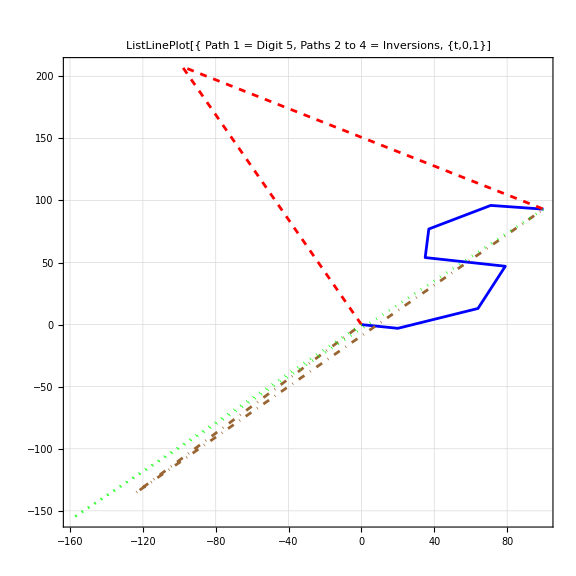

```mathematica
ListLinePlot[{
digit5,
flistpath[soldigit5p2[[1]],{0,0}],
flistpath[soldigit5p2[[2]],{0,0}],
flistpath[soldigit5p2v3[[1]],{0,0}]},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue, {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 = Digit 5,
Paths 2 to 4 = Inversions,
 {t,0,1}]"],16]]
```

```mathematica
Timing[solsemicircle2=solve3lines[Expand[Flatten[chen2z3core]],Flatten[semicirclecore3],vars2line2dchen,
{{3}},{},5]]
```

{0.013351,{{a_1→5.332,a_2→-7.3322,b_1→-1.414,b_2→1.414},{a_1→-1.332,a_2→-0.6678,b_1→1.414,b_2→-1.414}}}

```mathematica
Map[flengthpath,solsemicircle2]
```

{12.98,2.91}

```mathematica
Timing[solsemicircle2v2=solve3lines[Expand[Flatten[chen2z3core]],Flatten[semicirclecore3],vars2line2dchen,
{{4}},{},5]]
```

{0.007286,{}}

```mathematica
Timing[solsemicircle2v3=solve3lines[Expand[Flatten[chen2z3core]],Flatten[semicirclecore3],vars2line2dchen,
{{5}},{},5]]
```

{0.010781,{{a_1→-1.,a_2→-1.,b_1→1.5708,b_2→-1.5708}}}

```mathematica
Map[flengthpath,solsemicircle2v3]
```

{3.142}

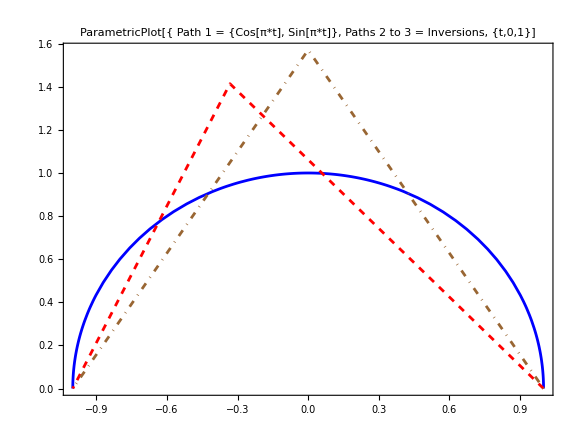

```mathematica
Show[ParametricPlot[
{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->3/4,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[π*t], Sin[π*t]},
Paths 2 to 3 = Inversions,
 {t,0,1}]"],16]],
ListLinePlot[{
flistpath[solsemicircle2[[2]],{1,0}],
flistpath[solsemicircle2v3[[1]],{1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}}]]
```

```mathematica
{Length[Flatten[chen3z4core]],Length[Flatten[digit5core4]],Length[vars3line2dchen]}
```

{8,8,6}

```mathematica
Timing[soldigit5p3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[digit5core4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.027525,{{a_1→158.42,a_2→-177.01,a_3→118.59,b_1→281.99,b_2→-327.76,b_3→138.77},{a_1→74.233,a_2→-42.21,a_3→67.977,b_1→-0.3274,b_2→83.755,b_3→9.5723}}}

```mathematica
Timing[soldigit5p3v2=solve3lines[Expand[Flatten[chen3z4core]],Flatten[digit5core4],vars3line2dchen,
{{4},{6}},{},5]]
```

{0.024454,{{a_1→102.95,a_2→-114.,a_3→111.08,b_1→186.3,b_2→-252.3,b_3→159.},{a_1→72.482,a_2→-33.593,a_3→61.111,b_1→5.3681,b_2→87.987,b_3→-0.355}}}

```mathematica
Timing[soldigit5p3v3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[digit5core4],vars3line2dchen,
{{5},{7}},{},5]]
```

{0.034771,{{a_1→95.18,a_2→-78.889,a_3→83.709,b_1→-50.51,b_2→361.55,b_3→-218.03},{a_1→71.648,a_2→-37.484,a_3→65.836,b_1→1.72,b_2→78.67,b_3→12.606}}}

```mathematica
Map[flengthpath,{soldigit5p3,soldigit5p3v2,soldigit5p3v3},{2}]
```

{{1248.2,276.5},{958.1,264.},{1049.,256.2}}

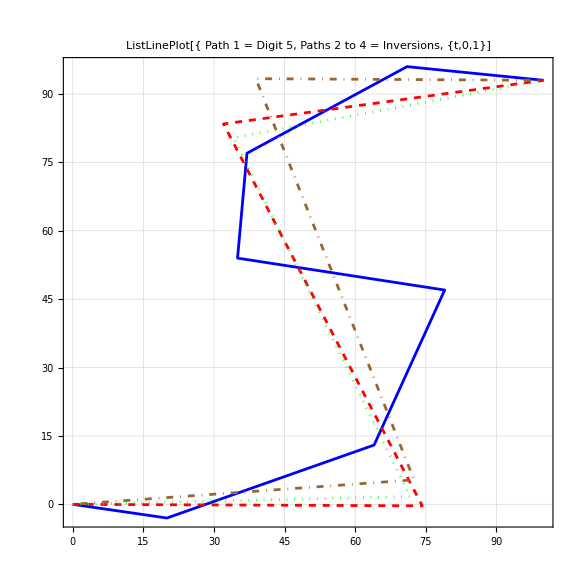

```mathematica
ListLinePlot[{
digit5,
flistpath[soldigit5p3[[2]],{0,0}],
flistpath[soldigit5p3v2[[2]],{0,0}],
flistpath[soldigit5p3v3[[2]],{0,0}]},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue, {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 = Digit 5,
Paths 2 to 4 = Inversions,
 {t,0,1}]"],16]]
```

```mathematica
Timing[solsemicircle3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{4},{8}},{},5]]
```

{0.022284,{{a_1→-1.594,a_2→0.64,a_3→-1.046,b_1→2.378,b_2→-0.2281,b_3→-2.15},{a_1→-0.1662,a_2→-1.543,a_3→-0.29071,b_1→0.82626,b_2→0.11676,b_3→-0.94302}}}

```mathematica
Map[flengthpath,solsemicircle3]
```

{5.989,3.189}

```mathematica
Timing[solsemicircle3v2=solve3lines[Expand[Flatten[chen3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.021333,{{a_1→-1.114,a_2→4.504,a_3→-5.39,b_1→1.518,b_2→7.835,b_3→-9.353},{a_1→-0.3949,a_2→-1.431,a_3→-0.174,b_1→1.0503,b_2→-0.288,b_3→-0.762}}}

```mathematica
Map[flengthpath,solsemicircle3v2]
```

{28.29,3.04}

```mathematica
Timing[solsemicircle3v3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{4},{6}},{},5]]
```

{0.024566,{{a_1→-0.483,a_2→-1.5737,a_3→0.0567,b_1→1.098,b_2→-0.5154,b_3→-0.5825},{a_1→0.0567,a_2→-1.5737,a_3→-0.483,b_1→0.5825,b_2→0.5154,b_3→-1.098}}}

```mathematica
Map[flengthpath,solsemicircle3v3]
```

{3.58,3.58}

```mathematica
flistpath[solsemicircle3[[2]],{1,0}]
```

{{1,0},{0.83376,0.82626},{-0.7093,0.94302},{-1.,0.}}

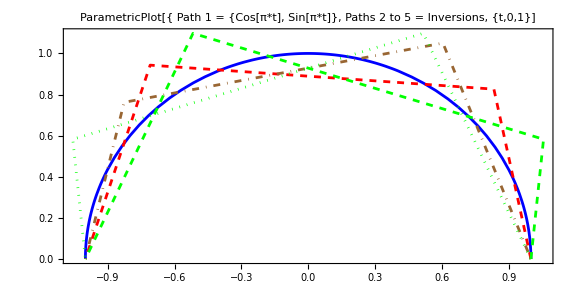

```mathematica
Show[ParametricPlot[
{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1/2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[π*t], Sin[π*t]},
Paths 2 to 5 = Inversions,
 {t,0,1}]"],16]],
ListLinePlot[{
flistpath[solsemicircle3[[2]],{1,0}],
flistpath[solsemicircle3v2[[2]],{1,0}],
flistpath[solsemicircle3v3[[1]],{1,0}],
flistpath[solsemicircle3v3[[2]],{1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}, {Dashed,Green}}]]
```

```mathematica
Timing[solcircle3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.022727,{{a_1→-0.634,a_2→-1.732,a_3→2.366,b_1→2.2477,b_2→-3.7699,b_3→1.5222},{a_1→-2.366,a_2→1.732,a_3→0.634,b_1→1.522,b_2→-3.7699,b_3→2.2477}}}

```mathematica
Map[flengthpath,solcircle3]
```

{12.81,12.81}

```mathematica
Timing[solcircle3v2=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.020837,{{a_1→-0.634,a_2→-1.732,a_3→2.366,b_1→2.2477,b_2→-3.7699,b_3→1.5222},{a_1→-2.366,a_2→1.732,a_3→0.634,b_1→1.522,b_2→-3.7699,b_3→2.2477}}}

```mathematica
Map[flengthpath,solcircle3v2]
```

{12.81,12.81}

```mathematica
Timing[solcircle3v3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{4},{8}},{},5]]
```

{0.021226,{{a_1→-1.581,a_2→0,a_3→1.581,b_1→1.987,b_2→-3.974,b_3→1.987},{a_1→1.581,a_2→0,a_3→-1.581,b_1→-1.987,b_2→3.974,b_3→-1.987}}}

```mathematica
Map[flengthpath,solcircle3v3]
```

{12.33,12.33}

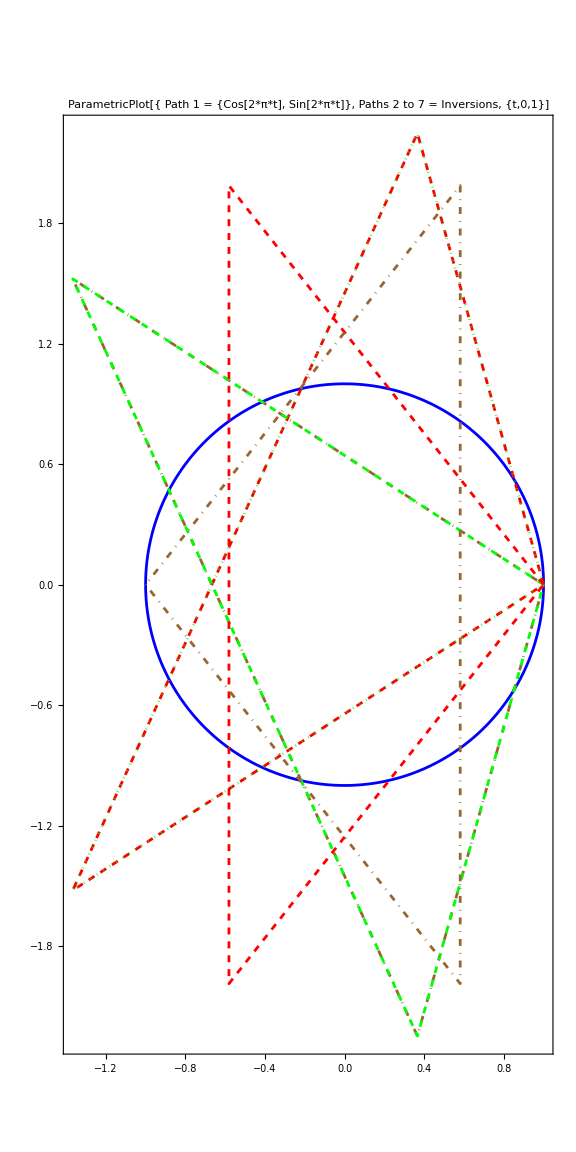

```mathematica
Show[ParametricPlot[
{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[2*π*t], Sin[2*π*t]},
Paths 2 to 7 = Inversions,
 {t,0,1}]"],16]],
ListLinePlot[{
flistpath[solcircle3[[1]],{1,0}],
flistpath[solcircle3[[2]],{1,0}],
flistpath[solcircle3v2[[1]],{1,0}],
flistpath[solcircle3v2[[2]],{1,0}],
flistpath[solcircle3v3[[1]],{1,0}],
flistpath[solcircle3v3[[2]],{-1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}, {Dashed,Green}}]]
```

```mathematica
fpw2d4[sollist_,t_]:=Module[{a1,a2,a3,a4,b1,b2,b3,b4},
{a1,a2,a3,a4,b1,b2,b3,b4}=sollist;
Piecewise[{{{a1,b1} 4t, 0≤t≤1/4}, {{a1,b1}+{a2,b2} 4(t-1/4), 1/4<t≤2/4}, {{a1,b1}+{a2,b2}+{a3,b3} 4(t-2/4), 2/4<t≤3/4}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4} 4(t-3/4), 3/4<t≤1}}]];
```

```mathematica
{Length[Flatten[chen4z5core]],Length[Flatten[circlecore5]],Length[vars4line2dchen]}
```

{14,14,8}

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
{Length[Flatten[chen4z5core]],Length[Flatten[digit5core5]],Length[vars4line2dchen]}
```

{14,14,8}

```mathematica
Timing[soldigit5p4=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[digit5core5],vars4line2dchen,
{{4},{8},{9},{11},{13},{14}},{},5],(flengthpath[#]<500)&]]
```

{1.12834,{{a_1→-5.9104,a_2→84.278,a_3→-45.735,a_4→67.367,b_1→-4.655,b_2→19.506,b_3→77.065,b_4→1.0836}}}

```mathematica
Timing[soldigit5p4v2=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[digit5core5],vars4line2dchen,
{{5},{8},{9},{11},{12},{14}},{},5],(flengthpath[#]<500)&]]
```

{0.505986,{{a_1→-9.6072,a_2→87.408,a_3→-44.055,a_4→66.254,b_1→-4.117,b_2→17.493,b_3→78.527,b_4→1.0969}}}

```mathematica
Timing[soldigit5p4v3=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[digit5core5],vars4line2dchen,
{{4},{8},{10},{11},{12},{13}},{},5],(flengthpath[#]<500)&]]
```

{6.43433,{{a_1→-47.694,a_2→124.82,a_3→-43.375,a_4→66.244,b_1→-7.6544,b_2→17.687,b_3→80.637,b_4→2.3302},{a_1→72.329,a_2→-38.87,a_3→25.561,a_4→40.98,b_1→5.6811,b_2→102.94,b_3→-19.87,b_4→4.2528},{a_1→44.752,a_2→31.177,a_3→-45.004,a_4→69.075,b_1→1.965,b_2→16.759,b_3→70.458,b_4→3.8183}}}

```mathematica
Map[flengthpath,{soldigit5p4,soldigit5p4v2,soldigit5p4v3},{2}]
```

{{371.8},{379.1},{488.7,315.,245.4}}

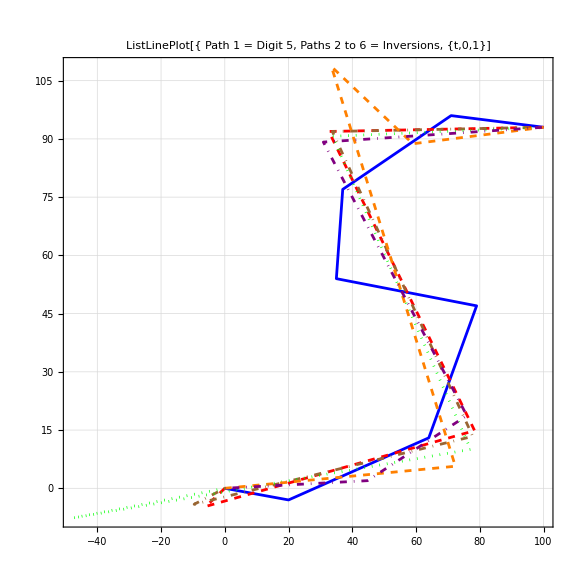

```mathematica
ListLinePlot[{
digit5,
flistpath[soldigit5p4[[1]],{0,0}],
flistpath[soldigit5p4v2[[1]],{0,0}],
flistpath[soldigit5p4v3[[1]],{0,0}],
flistpath[soldigit5p4v3[[2]],{0,0}],
flistpath[soldigit5p4v3[[3]],{0,0}]},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue, {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}, {Dashed,Orange}, {DotDashed,Purple}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 = Digit 5,
Paths 2 to 6 = Inversions,
 {t,0,1}]"],16]]
```

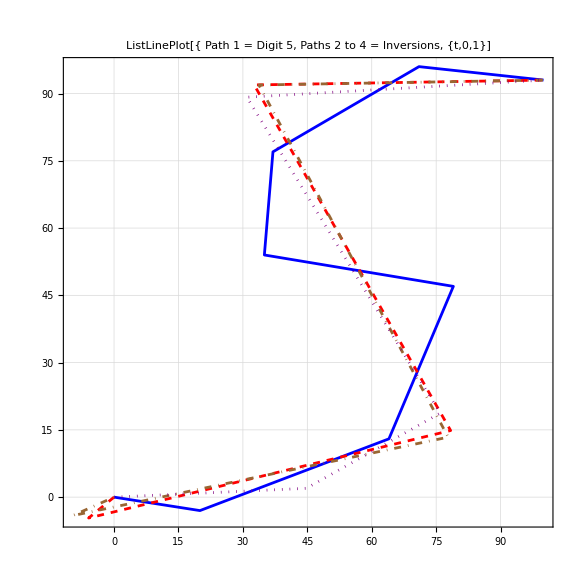

```mathematica
ListLinePlot[{
digit5,
flistpath[soldigit5p4[[1]],{0,0}],
flistpath[soldigit5p4v2[[1]],{0,0}],
flistpath[soldigit5p4v3[[3]],{0,0}]},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue, {Dashed,Red}, {DotDashed,Brown}, {Dotted,Purple}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 = Digit 5,
Paths 2 to 4 = Inversions,
 {t,0,1}]"],16]]
```

```mathematica
Timing[solsemicircle4=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{4},{8},{9},{11},{13},{14}},{},5],(flengthpath[#]<10)&]]
```

{0.524982,{{a_1→-0.026712,a_2→-0.81009,a_3→-1.0402,a_4→-0.12302,b_1→0.41934,b_2→0.68826,b_3→-0.47027,b_4→-0.63733}}}

```mathematica
Map[flengthpath,solsemicircle4]
```

{2.942}

```mathematica
Timing[solsemicircle4v2=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{5},{8},{9},{11},{12},{14}},{},5],(flengthpath[#]<10)&]]
```

{0.423189,{{a_1→-0.36407,a_2→-1.3996,a_3→-0.4883,a_4→0.25194,b_1→1.0101,b_2→-0.18515,b_3→-1.6593,b_4→0.83438},{a_1→-0.21437,a_2→-1.0178,a_3→-0.69453,a_4→-0.073264,b_1→0.7794,b_2→0.27278,b_3→-0.55794,b_4→-0.49425}}}

```mathematica
Map[flengthpath,solsemicircle4v2]
```

{5.916,2.466}

```mathematica
Timing[solsemicircle4v3=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{5},{8},{10},{11},{12},{13}},{},5],(flengthpath[#]<10)&]]
```

{1.50175,{{a_1→-0.32035,a_2→-2.3102,a_3→0.84881,a_4→-0.21827,b_1→0.96112,b_2→-0.15908,b_3→0.084112,b_4→-0.88616}}}

```mathematica
Map[flengthpath,solsemicircle4v3]
```

{6.894}

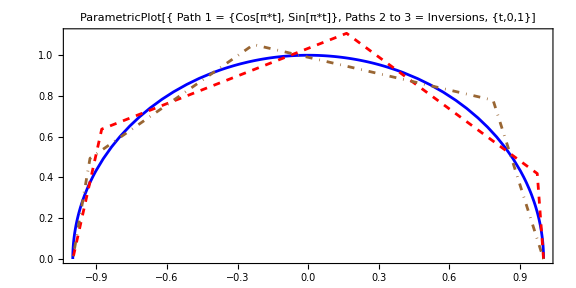

```mathematica
Show[ParametricPlot[
{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1/2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[π*t], Sin[π*t]},
Paths 2 to 3 = Inversions,
 {t,0,1}]"],16]],
ListLinePlot[{
flistpath[solsemicircle4[[1]],{1,0}],
flistpath[solsemicircle4v2[[2]],{1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}}]]
```

```mathematica
Timing[solcircle4=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[circlecore5],vars4line2dchen,
{{4},{8},{9},{12},{13},{14}},{},5],(flengthpath[#]<20)&]]
```

{0.129068,{{a_1→0.7196,a_2→-2.353,a_3→0.04134,a_4→1.592,b_1→-0.597,b_2→2.409,b_3→-3.691,b_4→1.879},{a_1→-1.419,a_2→-0.5167,a_3→4.538,a_4→-2.602,b_1→1.402,b_2→-2.443,b_3→1.362,b_4→-0.3199},{a_1→-0.634,a_2→-1.732,a_3→1.732,a_4→0.634,b_1→1.328,b_2→-1.328,b_3→-1.327,b_4→1.328}}}

```mathematica
Map[flengthpath,solcircle4]
```

{16.63,17.61,9.}

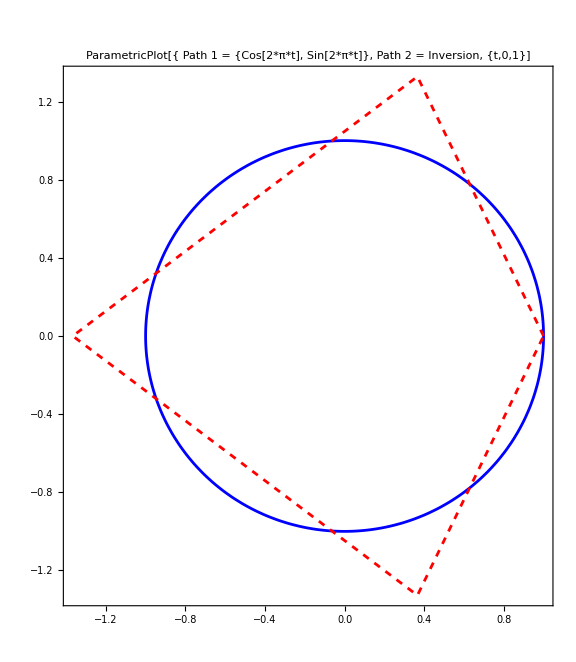

```mathematica
Show[ParametricPlot[
{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1.15,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[2*π*t], Sin[2*π*t]},
Path 2 = Inversion,
 {t,0,1}]"],16]],
ListLinePlot[{(*
flistpath[solcircle4[[1]],{1,0}],
flistpath[solcircle4[[2]],{1,0}],*)
flistpath[solcircle4[[3]],{1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}}]]
```

```mathematica
{Length[Flatten[chen5z6core]],Length[Flatten[digit5core6]],Length[vars5line2dchen]}
```

{23,23,10}

```mathematica
N[digit5core6]
```

{{100.,93.},{5069.5},{146820.,252884.},{2.99866×10^6,7.75879×10^6,7.96936×10^6},{4.77162×10^7,1.67574×10^8,-1.08126×10^8,2.44036×10^8,-3.5437×10^7,1.83562×10^8},{6.20683×10^8,2.8194×10^9,-2.76511×10^9,5.23866×10^9,-1.84841×10^9,-2.4162×10^9,5.50076×10^9,2.67321×10^8,3.34886×10^9}}

```mathematica
Timing[soldigit5p5=Select[solve3lines[Expand[Flatten[chen5z6core]],Flatten[digit5core6],vars5line2dchen,
{{4},{8},{9},{11},{13},{14},{16},{18},{19},{20},{21},{22},{23}},{},2],(flengthpath[#]<500)&]]
```

$Aborted

```mathematica
Timing[soldigit5p4v2=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[digit5core5],vars4line2dchen,
{{5},{8},{9},{11},{12},{14}},{},5],(flengthpath[#]<500)&]]
```

{0.505986,{{a_1→-9.6072,a_2→87.408,a_3→-44.055,a_4→66.254,b_1→-4.117,b_2→17.493,b_3→78.527,b_4→1.0969}}}

```mathematica
Timing[soldigit5p4v3=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[digit5core5],vars4line2dchen,
{{5},{8},{10},{11},{12},{13}},{},5],(flengthpath[#]<500)&]]
```

{1.50011,{{a_1→-41.53,a_2→118.11,a_3→-42.408,a_4→65.832,b_1→-5.8158,b_2→14.747,b_3→81.057,b_4→3.0114},{a_1→27.279,a_2→55.389,a_3→-77.323,a_4→94.656,b_1→-10.661,b_2→71.43,b_3→47.252,b_4→-15.02}}}

```mathematica
Map[flengthpath,{soldigit5p4,soldigit5p4v2,soldigit5p4v3},{2}]
```

{{371.8},{379.1},{468.1,404.6}}

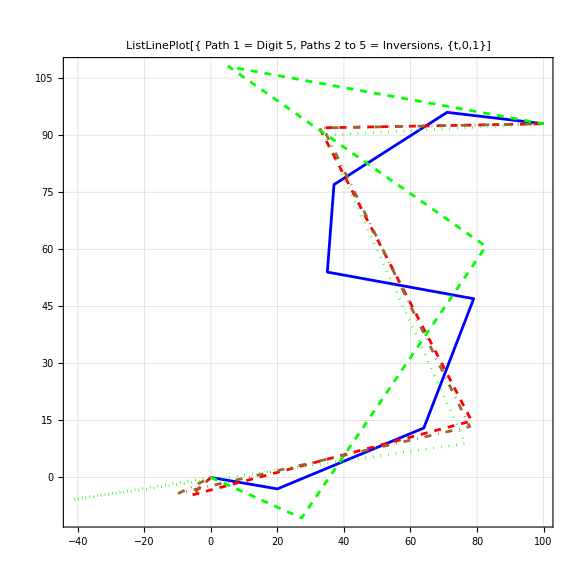

```mathematica
ListLinePlot[{
digit5,
flistpath[soldigit5p4[[1]],{0,0}],
flistpath[soldigit5p4v2[[1]],{0,0}],
flistpath[soldigit5p4v3[[1]],{0,0}],
flistpath[soldigit5p4v3[[2]],{0,0}]},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue, {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}, {Dashed,Green}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 = Digit 5,
Paths 2 to 5 = Inversions,
 {t,0,1}]"],16]]
```

```mathematica
{Length[Flatten[chen5z5core]],Length[Flatten[semicirclecore5]],Length[vars5line2dchen]}
```

{14,14,10}

```mathematica
Timing[solsemicircle5=solve3lines[Expand[Flatten[chen5z5core]],Flatten[semicirclecore5],vars5line2dchen,
{{4},{8},{14},{13}},{},2]]
```

$Aborted

```mathematica
{Length[Flatten[chen5z5core]],Length[Flatten[circlecore5]],Length[vars5line2dchen]}
```

{14,14,10}

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
eqs5lineschen2345=MapThread[Equal,{Expand[Flatten[chen5z5core]],Flatten[circlecore5]}];
```

```mathematica
Grid[Transpose[{eqs5lineschen2345}],Frame->All]
```

a_1+a_2+a_3+a_4+a_5==0
b_1+b_2+b_3+b_4+b_5==0
(a_1 b_1)/2+a_1 b_2+(a_2 b_2)/2+a_1 b_3+a_2 b_3+(a_3 b_3)/2+a_1 b_4+a_2 b_4+a_3 b_4+(a_4 b_4)/2+a_1 b_5+a_2 b_5+a_3 b_5+a_4 b_5+(a_5 b_5)/2==π
1/6 a_1^2 b_1+1/2 a_1^2 b_2+1/2 a_1 a_2 b_2+1/6 a_2^2 b_2+1/2 a_1^2 b_3+a_1 a_2 b_3+1/2 a_2^2 b_3+1/2 a_1 a_3 b_3+1/2 a_2 a_3 b_3+1/6 a_3^2 b_3+1/2 a_1^2 b_4+a_1 a_2 b_4+1/2 a_2^2 b_4+a_1 a_3 b_4+a_2 a_3 b_4+1/2 a_3^2 b_4+1/2 a_1 a_4 b_4+1/2 a_2 a_4 b_4+1/2 a_3 a_4 b_4+1/6 a_4^2 b_4+1/2 a_1^2 b_5+a_1 a_2 b_5+1/2 a_2^2 b_5+a_1 a_3 b_5+a_2 a_3 b_5+1/2 a_3^2 b_5+a_1 a_4 b_5+a_2 a_4 b_5+a_3 a_4 b_5+1/2 a_4^2 b_5+1/2 a_1 a_5 b_5+1/2 a_2 a_5 b_5+1/2 a_3 a_5 b_5+1/2 a_4 a_5 b_5+1/6 a_5^2 b_5==-π
1/6 a_1 b_1^2+1/2 a_1 b_1 b_2+1/2 a_1 b_2^2+1/6 a_2 b_2^2+1/2 a_1 b_1 b_3+a_1 b_2 b_3+1/2 a_2 b_2 b_3+1/2 a_1 b_3^2+1/2 a_2 b_3^2+1/6 a_3 b_3^2+1/2 a_1 b_1 b_4+a_1 b_2 b_4+1/2 a_2 b_2 b_4+a_1 b_3 b_4+a_2 b_3 b_4+1/2 a_3 b_3 b_4+1/2 a_1 b_4^2+1/2 a_2 b_4^2+1/2 a_3 b_4^2+1/6 a_4 b_4^2+1/2 a_1 b_1 b_5+a_1 b_2 b_5+1/2 a_2 b_2 b_5+a_1 b_3 b_5+a_2 b_3 b_5+1/2 a_3 b_3 b_5+a_1 b_4 b_5+a_2 b_4 b_5+a_3 b_4 b_5+1/2 a_4 b_4 b_5+1/2 a_1 b_5^2+1/2 a_2 b_5^2+1/2 a_3 b_5^2+1/2 a_4 b_5^2+1/6 a_5 b_5^2==0
1/24 a_1^3 b_1+1/6 a_1^3 b_2+1/4 a_1^2 a_2 b_2+1/6 a_1 a_2^2 b_2+1/24 a_2^3 b_2+1/6 a_1^3 b_3+1/2 a_1^2 a_2 b_3+1/2 a_1 a_2^2 b_3+1/6 a_2^3 b_3+1/4 a_1^2 a_3 b_3+1/2 a_1 a_2 a_3 b_3+1/4 a_2^2 a_3 b_3+1/6 a_1 a_3^2 b_3+1/6 a_2 a_3^2 b_3+1/24 a_3^3 b_3+1/6 a_1^3 b_4+1/2 a_1^2 a_2 b_4+1/2 a_1 a_2^2 b_4+1/6 a_2^3 b_4+1/2 a_1^2 a_3 b_4+a_1 a_2 a_3 b_4+1/2 a_2^2 a_3 b_4+1/2 a_1 a_3^2 b_4+1/2 a_2 a_3^2 b_4+1/6 a_3^3 b_4+1/4 a_1^2 a_4 b_4+1/2 a_1 a_2 a_4 b_4+1/4 a_2^2 a_4 b_4+1/2 a_1 a_3 a_4 b_4+1/2 a_2 a_3 a_4 b_4+1/4 a_3^2 a_4 b_4+1/6 a_1 a_4^2 b_4+1/6 a_2 a_4^2 b_4+1/6 a_3 a_4^2 b_4+1/24 a_4^3 b_4+1/6 a_1^3 b_5+1/2 a_1^2 a_2 b_5+1/2 a_1 a_2^2 b_5+1/6 a_2^3 b_5+1/2 a_1^2 a_3 b_5+a_1 a_2 a_3 b_5+1/2 a_2^2 a_3 b_5+1/2 a_1 a_3^2 b_5+1/2 a_2 a_3^2 b_5+1/6 a_3^3 b_5+1/2 a_1^2 a_4 b_5+a_1 a_2 a_4 b_5+1/2 a_2^2 a_4 b_5+a_1 a_3 a_4 b_5+a_2 a_3 a_4 b_5+1/2 a_3^2 a_4 b_5+1/2 a_1 a_4^2 b_5+1/2 a_2 a_4^2 b_5+1/2 a_3 a_4^2 b_5+1/6 a_4^3 b_5+1/4 a_1^2 a_5 b_5+1/2 a_1 a_2 a_5 b_5+1/4 a_2^2 a_5 b_5+1/2 a_1 a_3 a_5 b_5+1/2 a_2 a_3 a_5 b_5+1/4 a_3^2 a_5 b_5+1/2 a_1 a_4 a_5 b_5+1/2 a_2 a_4 a_5 b_5+1/2 a_3 a_4 a_5 b_5+1/4 a_4^2 a_5 b_5+1/6 a_1 a_5^2 b_5+1/6 a_2 a_5^2 b_5+1/6 a_3 a_5^2 b_5+1/6 a_4 a_5^2 b_5+1/24 a_5^3 b_5==(5 π)/8
1/24 a_1^2 b_1^2+1/6 a_1^2 b_1 b_2+1/4 a_1^2 b_2^2+1/6 a_1 a_2 b_2^2+1/24 a_2^2 b_2^2+1/6 a_1^2 b_1 b_3+1/2 a_1^2 b_2 b_3+1/2 a_1 a_2 b_2 b_3+1/6 a_2^2 b_2 b_3+1/4 a_1^2 b_3^2+1/2 a_1 a_2 b_3^2+1/4 a_2^2 b_3^2+1/6 a_1 a_3 b_3^2+1/6 a_2 a_3 b_3^2+1/24 a_3^2 b_3^2+1/6 a_1^2 b_1 b_4+1/2 a_1^2 b_2 b_4+1/2 a_1 a_2 b_2 b_4+1/6 a_2^2 b_2 b_4+1/2 a_1^2 b_3 b_4+a_1 a_2 b_3 b_4+1/2 a_2^2 b_3 b_4+1/2 a_1 a_3 b_3 b_4+1/2 a_2 a_3 b_3 b_4+1/6 a_3^2 b_3 b_4+1/4 a_1^2 b_4^2+1/2 a_1 a_2 b_4^2+1/4 a_2^2 b_4^2+1/2 a_1 a_3 b_4^2+1/2 a_2 a_3 b_4^2+1/4 a_3^2 b_4^2+1/6 a_1 a_4 b_4^2+1/6 a_2 a_4 b_4^2+1/6 a_3 a_4 b_4^2+1/24 a_4^2 b_4^2+1/6 a_1^2 b_1 b_5+1/2 a_1^2 b_2 b_5+1/2 a_1 a_2 b_2 b_5+1/6 a_2^2 b_2 b_5+1/2 a_1^2 b_3 b_5+a_1 a_2 b_3 b_5+1/2 a_2^2 b_3 b_5+1/2 a_1 a_3 b_3 b_5+1/2 a_2 a_3 b_3 b_5+1/6 a_3^2 b_3 b_5+1/2 a_1^2 b_4 b_5+a_1 a_2 b_4 b_5+1/2 a_2^2 b_4 b_5+a_1 a_3 b_4 b_5+a_2 a_3 b_4 b_5+1/2 a_3^2 b_4 b_5+1/2 a_1 a_4 b_4 b_5+1/2 a_2 a_4 b_4 b_5+1/2 a_3 a_4 b_4 b_5+1/6 a_4^2 b_4 b_5+1/4 a_1^2 b_5^2+1/2 a_1 a_2 b_5^2+1/4 a_2^2 b_5^2+1/2 a_1 a_3 b_5^2+1/2 a_2 a_3 b_5^2+1/4 a_3^2 b_5^2+1/2 a_1 a_4 b_5^2+1/2 a_2 a_4 b_5^2+1/2 a_3 a_4 b_5^2+1/4 a_4^2 b_5^2+1/6 a_1 a_5 b_5^2+1/6 a_2 a_5 b_5^2+1/6 a_3 a_5 b_5^2+1/6 a_4 a_5 b_5^2+1/24 a_5^2 b_5^2==0
1/24 a_1 b_1^3+1/6 a_1 b_1^2 b_2+1/4 a_1 b_1 b_2^2+1/6 a_1 b_2^3+1/24 a_2 b_2^3+1/6 a_1 b_1^2 b_3+1/2 a_1 b_1 b_2 b_3+1/2 a_1 b_2^2 b_3+1/6 a_2 b_2^2 b_3+1/4 a_1 b_1 b_3^2+1/2 a_1 b_2 b_3^2+1/4 a_2 b_2 b_3^2+1/6 a_1 b_3^3+1/6 a_2 b_3^3+1/24 a_3 b_3^3+1/6 a_1 b_1^2 b_4+1/2 a_1 b_1 b_2 b_4+1/2 a_1 b_2^2 b_4+1/6 a_2 b_2^2 b_4+1/2 a_1 b_1 b_3 b_4+a_1 b_2 b_3 b_4+1/2 a_2 b_2 b_3 b_4+1/2 a_1 b_3^2 b_4+1/2 a_2 b_3^2 b_4+1/6 a_3 b_3^2 b_4+1/4 a_1 b_1 b_4^2+1/2 a_1 b_2 b_4^2+1/4 a_2 b_2 b_4^2+1/2 a_1 b_3 b_4^2+1/2 a_2 b_3 b_4^2+1/4 a_3 b_3 b_4^2+1/6 a_1 b_4^3+1/6 a_2 b_4^3+1/6 a_3 b_4^3+1/24 a_4 b_4^3+1/6 a_1 b_1^2 b_5+1/2 a_1 b_1 b_2 b_5+1/2 a_1 b_2^2 b_5+1/6 a_2 b_2^2 b_5+1/2 a_1 b_1 b_3 b_5+a_1 b_2 b_3 b_5+1/2 a_2 b_2 b_3 b_5+1/2 a_1 b_3^2 b_5+1/2 a_2 b_3^2 b_5+1/6 a_3 b_3^2 b_5+1/2 a_1 b_1 b_4 b_5+a_1 b_2 b_4 b_5+1/2 a_2 b_2 b_4 b_5+a_1 b_3 b_4 b_5+a_2 b_3 b_4 b_5+1/2 a_3 b_3 b_4 b_5+1/2 a_1 b_4^2 b_5+1/2 a_2 b_4^2 b_5+1/2 a_3 b_4^2 b_5+1/6 a_4 b_4^2 b_5+1/4 a_1 b_1 b_5^2+1/2 a_1 b_2 b_5^2+1/4 a_2 b_2 b_5^2+1/2 a_1 b_3 b_5^2+1/2 a_2 b_3 b_5^2+1/4 a_3 b_3 b_5^2+1/2 a_1 b_4 b_5^2+1/2 a_2 b_4 b_5^2+1/2 a_3 b_4 b_5^2+1/4 a_4 b_4 b_5^2+1/6 a_1 b_5^3+1/6 a_2 b_5^3+1/6 a_3 b_5^3+1/6 a_4 b_5^3+1/24 a_5 b_5^3==π/8
1/120 a_1^4 b_1+1/24 a_1^4 b_2+1/12 a_1^3 a_2 b_2+1/12 a_1^2 a_2^2 b_2+1/24 a_1 a_2^3 b_2+1/120 a_2^4 b_2+1/24 a_1^4 b_3+1/6 a_1^3 a_2 b_3+1/4 a_1^2 a_2^2 b_3+1/6 a_1 a_2^3 b_3+1/24 a_2^4 b_3+1/12 a_1^3 a_3 b_3+1/4 a_1^2 a_2 a_3 b_3+1/4 a_1 a_2^2 a_3 b_3+1/12 a_2^3 a_3 b_3+1/12 a_1^2 a_3^2 b_3+1/6 a_1 a_2 a_3^2 b_3+1/12 a_2^2 a_3^2 b_3+1/24 a_1 a_3^3 b_3+1/24 a_2 a_3^3 b_3+1/120 a_3^4 b_3+1/24 a_1^4 b_4+1/6 a_1^3 a_2 b_4+1/4 a_1^2 a_2^2 b_4+1/6 a_1 a_2^3 b_4+1/24 a_2^4 b_4+1/6 a_1^3 a_3 b_4+1/2 a_1^2 a_2 a_3 b_4+1/2 a_1 a_2^2 a_3 b_4+1/6 a_2^3 a_3 b_4+1/4 a_1^2 a_3^2 b_4+1/2 a_1 a_2 a_3^2 b_4+1/4 a_2^2 a_3^2 b_4+1/6 a_1 a_3^3 b_4+1/6 a_2 a_3^3 b_4+1/24 a_3^4 b_4+1/12 a_1^3 a_4 b_4+1/4 a_1^2 a_2 a_4 b_4+1/4 a_1 a_2^2 a_4 b_4+1/12 a_2^3 a_4 b_4+1/4 a_1^2 a_3 a_4 b_4+1/2 a_1 a_2 a_3 a_4 b_4+1/4 a_2^2 a_3 a_4 b_4+1/4 a_1 a_3^2 a_4 b_4+1/4 a_2 a_3^2 a_4 b_4+1/12 a_3^3 a_4 b_4+1/12 a_1^2 a_4^2 b_4+1/6 a_1 a_2 a_4^2 b_4+1/12 a_2^2 a_4^2 b_4+1/6 a_1 a_3 a_4^2 b_4+1/6 a_2 a_3 a_4^2 b_4+1/12 a_3^2 a_4^2 b_4+1/24 a_1 a_4^3 b_4+1/24 a_2 a_4^3 b_4+1/24 a_3 a_4^3 b_4+1/120 a_4^4 b_4+1/24 a_1^4 b_5+1/6 a_1^3 a_2 b_5+1/4 a_1^2 a_2^2 b_5+1/6 a_1 a_2^3 b_5+1/24 a_2^4 b_5+1/6 a_1^3 a_3 b_5+1/2 a_1^2 a_2 a_3 b_5+1/2 a_1 a_2^2 a_3 b_5+1/6 a_2^3 a_3 b_5+1/4 a_1^2 a_3^2 b_5+1/2 a_1 a_2 a_3^2 b_5+1/4 a_2^2 a_3^2 b_5+1/6 a_1 a_3^3 b_5+1/6 a_2 a_3^3 b_5+1/24 a_3^4 b_5+1/6 a_1^3 a_4 b_5+1/2 a_1^2 a_2 a_4 b_5+1/2 a_1 a_2^2 a_4 b_5+1/6 a_2^3 a_4 b_5+1/2 a_1^2 a_3 a_4 b_5+a_1 a_2 a_3 a_4 b_5+1/2 a_2^2 a_3 a_4 b_5+1/2 a_1 a_3^2 a_4 b_5+1/2 a_2 a_3^2 a_4 b_5+1/6 a_3^3 a_4 b_5+1/4 a_1^2 a_4^2 b_5+1/2 a_1 a_2 a_4^2 b_5+1/4 a_2^2 a_4^2 b_5+1/2 a_1 a_3 a_4^2 b_5+1/2 a_2 a_3 a_4^2 b_5+1/4 a_3^2 a_4^2 b_5+1/6 a_1 a_4^3 b_5+1/6 a_2 a_4^3 b_5+1/6 a_3 a_4^3 b_5+1/24 a_4^4 b_5+1/12 a_1^3 a_5 b_5+1/4 a_1^2 a_2 a_5 b_5+1/4 a_1 a_2^2 a_5 b_5+1/12 a_2^3 a_5 b_5+1/4 a_1^2 a_3 a_5 b_5+1/2 a_1 a_2 a_3 a_5 b_5+1/4 a_2^2 a_3 a_5 b_5+1/4 a_1 a_3^2 a_5 b_5+1/4 a_2 a_3^2 a_5 b_5+1/12 a_3^3 a_5 b_5+1/4 a_1^2 a_4 a_5 b_5+1/2 a_1 a_2 a_4 a_5 b_5+1/4 a_2^2 a_4 a_5 b_5+1/2 a_1 a_3 a_4 a_5 b_5+1/2 a_2 a_3 a_4 a_5 b_5+1/4 a_3^2 a_4 a_5 b_5+1/4 a_1 a_4^2 a_5 b_5+1/4 a_2 a_4^2 a_5 b_5+1/4 a_3 a_4^2 a_5 b_5+1/12 a_4^3 a_5 b_5+1/12 a_1^2 a_5^2 b_5+1/6 a_1 a_2 a_5^2 b_5+1/12 a_2^2 a_5^2 b_5+1/6 a_1 a_3 a_5^2 b_5+1/6 a_2 a_3 a_5^2 b_5+1/12 a_3^2 a_5^2 b_5+1/6 a_1 a_4 a_5^2 b_5+1/6 a_2 a_4 a_5^2 b_5+1/6 a_3 a_4 a_5^2 b_5+1/12 a_4^2 a_5^2 b_5+1/24 a_1 a_5^3 b_5+1/24 a_2 a_5^3 b_5+1/24 a_3 a_5^3 b_5+1/24 a_4 a_5^3 b_5+1/120 a_5^4 b_5==-(7 π)/24
1/120 a_1^3 b_1^2+1/24 a_1^3 b_1 b_2+1/12 a_1^3 b_2^2+1/12 a_1^2 a_2 b_2^2+1/24 a_1 a_2^2 b_2^2+1/120 a_2^3 b_2^2+1/24 a_1^3 b_1 b_3+1/6 a_1^3 b_2 b_3+1/4 a_1^2 a_2 b_2 b_3+1/6 a_1 a_2^2 b_2 b_3+1/24 a_2^3 b_2 b_3+1/12 a_1^3 b_3^2+1/4 a_1^2 a_2 b_3^2+1/4 a_1 a_2^2 b_3^2+1/12 a_2^3 b_3^2+1/12 a_1^2 a_3 b_3^2+1/6 a_1 a_2 a_3 b_3^2+1/12 a_2^2 a_3 b_3^2+1/24 a_1 a_3^2 b_3^2+1/24 a_2 a_3^2 b_3^2+1/120 a_3^3 b_3^2+1/24 a_1^3 b_1 b_4+1/6 a_1^3 b_2 b_4+1/4 a_1^2 a_2 b_2 b_4+1/6 a_1 a_2^2 b_2 b_4+1/24 a_2^3 b_2 b_4+1/6 a_1^3 b_3 b_4+1/2 a_1^2 a_2 b_3 b_4+1/2 a_1 a_2^2 b_3 b_4+1/6 a_2^3 b_3 b_4+1/4 a_1^2 a_3 b_3 b_4+1/2 a_1 a_2 a_3 b_3 b_4+1/4 a_2^2 a_3 b_3 b_4+1/6 a_1 a_3^2 b_3 b_4+1/6 a_2 a_3^2 b_3 b_4+1/24 a_3^3 b_3 b_4+1/12 a_1^3 b_4^2+1/4 a_1^2 a_2 b_4^2+1/4 a_1 a_2^2 b_4^2+1/12 a_2^3 b_4^2+1/4 a_1^2 a_3 b_4^2+1/2 a_1 a_2 a_3 b_4^2+1/4 a_2^2 a_3 b_4^2+1/4 a_1 a_3^2 b_4^2+1/4 a_2 a_3^2 b_4^2+1/12 a_3^3 b_4^2+1/12 a_1^2 a_4 b_4^2+1/6 a_1 a_2 a_4 b_4^2+1/12 a_2^2 a_4 b_4^2+1/6 a_1 a_3 a_4 b_4^2+1/6 a_2 a_3 a_4 b_4^2+1/12 a_3^2 a_4 b_4^2+1/24 a_1 a_4^2 b_4^2+1/24 a_2 a_4^2 b_4^2+1/24 a_3 a_4^2 b_4^2+1/120 a_4^3 b_4^2+1/24 a_1^3 b_1 b_5+1/6 a_1^3 b_2 b_5+1/4 a_1^2 a_2 b_2 b_5+1/6 a_1 a_2^2 b_2 b_5+1/24 a_2^3 b_2 b_5+1/6 a_1^3 b_3 b_5+1/2 a_1^2 a_2 b_3 b_5+1/2 a_1 a_2^2 b_3 b_5+1/6 a_2^3 b_3 b_5+1/4 a_1^2 a_3 b_3 b_5+1/2 a_1 a_2 a_3 b_3 b_5+1/4 a_2^2 a_3 b_3 b_5+1/6 a_1 a_3^2 b_3 b_5+1/6 a_2 a_3^2 b_3 b_5+1/24 a_3^3 b_3 b_5+1/6 a_1^3 b_4 b_5+1/2 a_1^2 a_2 b_4 b_5+1/2 a_1 a_2^2 b_4 b_5+1/6 a_2^3 b_4 b_5+1/2 a_1^2 a_3 b_4 b_5+a_1 a_2 a_3 b_4 b_5+1/2 a_2^2 a_3 b_4 b_5+1/2 a_1 a_3^2 b_4 b_5+1/2 a_2 a_3^2 b_4 b_5+1/6 a_3^3 b_4 b_5+1/4 a_1^2 a_4 b_4 b_5+1/2 a_1 a_2 a_4 b_4 b_5+1/4 a_2^2 a_4 b_4 b_5+1/2 a_1 a_3 a_4 b_4 b_5+1/2 a_2 a_3 a_4 b_4 b_5+1/4 a_3^2 a_4 b_4 b_5+1/6 a_1 a_4^2 b_4 b_5+1/6 a_2 a_4^2 b_4 b_5+1/6 a_3 a_4^2 b_4 b_5+1/24 a_4^3 b_4 b_5+1/12 a_1^3 b_5^2+1/4 a_1^2 a_2 b_5^2+1/4 a_1 a_2^2 b_5^2+1/12 a_2^3 b_5^2+1/4 a_1^2 a_3 b_5^2+1/2 a_1 a_2 a_3 b_5^2+1/4 a_2^2 a_3 b_5^2+1/4 a_1 a_3^2 b_5^2+1/4 a_2 a_3^2 b_5^2+1/12 a_3^3 b_5^2+1/4 a_1^2 a_4 b_5^2+1/2 a_1 a_2 a_4 b_5^2+1/4 a_2^2 a_4 b_5^2+1/2 a_1 a_3 a_4 b_5^2+1/2 a_2 a_3 a_4 b_5^2+1/4 a_3^2 a_4 b_5^2+1/4 a_1 a_4^2 b_5^2+1/4 a_2 a_4^2 b_5^2+1/4 a_3 a_4^2 b_5^2+1/12 a_4^3 b_5^2+1/12 a_1^2 a_5 b_5^2+1/6 a_1 a_2 a_5 b_5^2+1/12 a_2^2 a_5 b_5^2+1/6 a_1 a_3 a_5 b_5^2+1/6 a_2 a_3 a_5 b_5^2+1/12 a_3^2 a_5 b_5^2+1/6 a_1 a_4 a_5 b_5^2+1/6 a_2 a_4 a_5 b_5^2+1/6 a_3 a_4 a_5 b_5^2+1/12 a_4^2 a_5 b_5^2+1/24 a_1 a_5^2 b_5^2+1/24 a_2 a_5^2 b_5^2+1/24 a_3 a_5^2 b_5^2+1/24 a_4 a_5^2 b_5^2+1/120 a_5^3 b_5^2==0
1/120 a_1^3 b_1^2+1/24 a_1^3 b_1 b_2+1/12 a_1^2 a_2 b_1 b_2+1/12 a_1^2 a_2 b_2^2+1/24 a_1 a_2^2 b_2^2+1/120 a_2^3 b_2^2+1/24 a_1^3 b_1 b_3+1/6 a_1^2 a_2 b_1 b_3+1/12 a_1^2 a_3 b_1 b_3+1/4 a_1^2 a_2 b_2 b_3+1/6 a_1 a_2^2 b_2 b_3+1/24 a_2^3 b_2 b_3+1/4 a_1^2 a_3 b_2 b_3+1/4 a_1 a_2 a_3 b_2 b_3+1/12 a_2^2 a_3 b_2 b_3+1/12 a_1^2 a_3 b_3^2+1/6 a_1 a_2 a_3 b_3^2+1/12 a_2^2 a_3 b_3^2+1/24 a_1 a_3^2 b_3^2+1/24 a_2 a_3^2 b_3^2+1/120 a_3^3 b_3^2+1/24 a_1^3 b_1 b_4+1/6 a_1^2 a_2 b_1 b_4+1/6 a_1^2 a_3 b_1 b_4+1/12 a_1^2 a_4 b_1 b_4+1/4 a_1^2 a_2 b_2 b_4+1/6 a_1 a_2^2 b_2 b_4+1/24 a_2^3 b_2 b_4+1/2 a_1^2 a_3 b_2 b_4+1/2 a_1 a_2 a_3 b_2 b_4+1/6 a_2^2 a_3 b_2 b_4+1/4 a_1^2 a_4 b_2 b_4+1/4 a_1 a_2 a_4 b_2 b_4+1/12 a_2^2 a_4 b_2 b_4+1/4 a_1^2 a_3 b_3 b_4+1/2 a_1 a_2 a_3 b_3 b_4+1/4 a_2^2 a_3 b_3 b_4+1/6 a_1 a_3^2 b_3 b_4+1/6 a_2 a_3^2 b_3 b_4+1/24 a_3^3 b_3 b_4+1/4 a_1^2 a_4 b_3 b_4+1/2 a_1 a_2 a_4 b_3 b_4+1/4 a_2^2 a_4 b_3 b_4+1/4 a_1 a_3 a_4 b_3 b_4+1/4 a_2 a_3 a_4 b_3 b_4+1/12 a_3^2 a_4 b_3 b_4+1/12 a_1^2 a_4 b_4^2+1/6 a_1 a_2 a_4 b_4^2+1/12 a_2^2 a_4 b_4^2+1/6 a_1 a_3 a_4 b_4^2+1/6 a_2 a_3 a_4 b_4^2+1/12 a_3^2 a_4 b_4^2+1/24 a_1 a_4^2 b_4^2+1/24 a_2 a_4^2 b_4^2+1/24 a_3 a_4^2 b_4^2+1/120 a_4^3 b_4^2+1/24 a_1^3 b_1 b_5+1/6 a_1^2 a_2 b_1 b_5+1/6 a_1^2 a_3 b_1 b_5+1/6 a_1^2 a_4 b_1 b_5+1/12 a_1^2 a_5 b_1 b_5+1/4 a_1^2 a_2 b_2 b_5+1/6 a_1 a_2^2 b_2 b_5+1/24 a_2^3 b_2 b_5+1/2 a_1^2 a_3 b_2 b_5+1/2 a_1 a_2 a_3 b_2 b_5+1/6 a_2^2 a_3 b_2 b_5+1/2 a_1^2 a_4 b_2 b_5+1/2 a_1 a_2 a_4 b_2 b_5+1/6 a_2^2 a_4 b_2 b_5+1/4 a_1^2 a_5 b_2 b_5+1/4 a_1 a_2 a_5 b_2 b_5+1/12 a_2^2 a_5 b_2 b_5+1/4 a_1^2 a_3 b_3 b_5+1/2 a_1 a_2 a_3 b_3 b_5+1/4 a_2^2 a_3 b_3 b_5+1/6 a_1 a_3^2 b_3 b_5+1/6 a_2 a_3^2 b_3 b_5+1/24 a_3^3 b_3 b_5+1/2 a_1^2 a_4 b_3 b_5+a_1 a_2 a_4 b_3 b_5+1/2 a_2^2 a_4 b_3 b_5+1/2 a_1 a_3 a_4 b_3 b_5+1/2 a_2 a_3 a_4 b_3 b_5+1/6 a_3^2 a_4 b_3 b_5+1/4 a_1^2 a_5 b_3 b_5+1/2 a_1 a_2 a_5 b_3 b_5+1/4 a_2^2 a_5 b_3 b_5+1/4 a_1 a_3 a_5 b_3 b_5+1/4 a_2 a_3 a_5 b_3 b_5+1/12 a_3^2 a_5 b_3 b_5+1/4 a_1^2 a_4 b_4 b_5+1/2 a_1 a_2 a_4 b_4 b_5+1/4 a_2^2 a_4 b_4 b_5+1/2 a_1 a_3 a_4 b_4 b_5+1/2 a_2 a_3 a_4 b_4 b_5+1/4 a_3^2 a_4 b_4 b_5+1/6 a_1 a_4^2 b_4 b_5+1/6 a_2 a_4^2 b_4 b_5+1/6 a_3 a_4^2 b_4 b_5+1/24 a_4^3 b_4 b_5+1/4 a_1^2 a_5 b_4 b_5+1/2 a_1 a_2 a_5 b_4 b_5+1/4 a_2^2 a_5 b_4 b_5+1/2 a_1 a_3 a_5 b_4 b_5+1/2 a_2 a_3 a_5 b_4 b_5+1/4 a_3^2 a_5 b_4 b_5+1/4 a_1 a_4 a_5 b_4 b_5+1/4 a_2 a_4 a_5 b_4 b_5+1/4 a_3 a_4 a_5 b_4 b_5+1/12 a_4^2 a_5 b_4 b_5+1/12 a_1^2 a_5 b_5^2+1/6 a_1 a_2 a_5 b_5^2+1/12 a_2^2 a_5 b_5^2+1/6 a_1 a_3 a_5 b_5^2+1/6 a_2 a_3 a_5 b_5^2+1/12 a_3^2 a_5 b_5^2+1/6 a_1 a_4 a_5 b_5^2+1/6 a_2 a_4 a_5 b_5^2+1/6 a_3 a_4 a_5 b_5^2+1/12 a_4^2 a_5 b_5^2+1/24 a_1 a_5^2 b_5^2+1/24 a_2 a_5^2 b_5^2+1/24 a_3 a_5^2 b_5^2+1/24 a_4 a_5^2 b_5^2+1/120 a_5^3 b_5^2==-π^2/2
1/120 a_1^2 b_1^3+1/24 a_1^2 b_1^2 b_2+1/12 a_1^2 b_1 b_2^2+1/12 a_1^2 b_2^3+1/24 a_1 a_2 b_2^3+1/120 a_2^2 b_2^3+1/24 a_1^2 b_1^2 b_3+1/6 a_1^2 b_1 b_2 b_3+1/4 a_1^2 b_2^2 b_3+1/6 a_1 a_2 b_2^2 b_3+1/24 a_2^2 b_2^2 b_3+1/12 a_1^2 b_1 b_3^2+1/4 a_1^2 b_2 b_3^2+1/4 a_1 a_2 b_2 b_3^2+1/12 a_2^2 b_2 b_3^2+1/12 a_1^2 b_3^3+1/6 a_1 a_2 b_3^3+1/12 a_2^2 b_3^3+1/24 a_1 a_3 b_3^3+1/24 a_2 a_3 b_3^3+1/120 a_3^2 b_3^3+1/24 a_1^2 b_1^2 b_4+1/6 a_1^2 b_1 b_2 b_4+1/4 a_1^2 b_2^2 b_4+1/6 a_1 a_2 b_2^2 b_4+1/24 a_2^2 b_2^2 b_4+1/6 a_1^2 b_1 b_3 b_4+1/2 a_1^2 b_2 b_3 b_4+1/2 a_1 a_2 b_2 b_3 b_4+1/6 a_2^2 b_2 b_3 b_4+1/4 a_1^2 b_3^2 b_4+1/2 a_1 a_2 b_3^2 b_4+1/4 a_2^2 b_3^2 b_4+1/6 a_1 a_3 b_3^2 b_4+1/6 a_2 a_3 b_3^2 b_4+1/24 a_3^2 b_3^2 b_4+1/12 a_1^2 b_1 b_4^2+1/4 a_1^2 b_2 b_4^2+1/4 a_1 a_2 b_2 b_4^2+1/12 a_2^2 b_2 b_4^2+1/4 a_1^2 b_3 b_4^2+1/2 a_1 a_2 b_3 b_4^2+1/4 a_2^2 b_3 b_4^2+1/4 a_1 a_3 b_3 b_4^2+1/4 a_2 a_3 b_3 b_4^2+1/12 a_3^2 b_3 b_4^2+1/12 a_1^2 b_4^3+1/6 a_1 a_2 b_4^3+1/12 a_2^2 b_4^3+1/6 a_1 a_3 b_4^3+1/6 a_2 a_3 b_4^3+1/12 a_3^2 b_4^3+1/24 a_1 a_4 b_4^3+1/24 a_2 a_4 b_4^3+1/24 a_3 a_4 b_4^3+1/120 a_4^2 b_4^3+1/24 a_1^2 b_1^2 b_5+1/6 a_1^2 b_1 b_2 b_5+1/4 a_1^2 b_2^2 b_5+1/6 a_1 a_2 b_2^2 b_5+1/24 a_2^2 b_2^2 b_5+1/6 a_1^2 b_1 b_3 b_5+1/2 a_1^2 b_2 b_3 b_5+1/2 a_1 a_2 b_2 b_3 b_5+1/6 a_2^2 b_2 b_3 b_5+1/4 a_1^2 b_3^2 b_5+1/2 a_1 a_2 b_3^2 b_5+1/4 a_2^2 b_3^2 b_5+1/6 a_1 a_3 b_3^2 b_5+1/6 a_2 a_3 b_3^2 b_5+1/24 a_3^2 b_3^2 b_5+1/6 a_1^2 b_1 b_4 b_5+1/2 a_1^2 b_2 b_4 b_5+1/2 a_1 a_2 b_2 b_4 b_5+1/6 a_2^2 b_2 b_4 b_5+1/2 a_1^2 b_3 b_4 b_5+a_1 a_2 b_3 b_4 b_5+1/2 a_2^2 b_3 b_4 b_5+1/2 a_1 a_3 b_3 b_4 b_5+1/2 a_2 a_3 b_3 b_4 b_5+1/6 a_3^2 b_3 b_4 b_5+1/4 a_1^2 b_4^2 b_5+1/2 a_1 a_2 b_4^2 b_5+1/4 a_2^2 b_4^2 b_5+1/2 a_1 a_3 b_4^2 b_5+1/2 a_2 a_3 b_4^2 b_5+1/4 a_3^2 b_4^2 b_5+1/6 a_1 a_4 b_4^2 b_5+1/6 a_2 a_4 b_4^2 b_5+1/6 a_3 a_4 b_4^2 b_5+1/24 a_4^2 b_4^2 b_5+1/12 a_1^2 b_1 b_5^2+1/4 a_1^2 b_2 b_5^2+1/4 a_1 a_2 b_2 b_5^2+1/12 a_2^2 b_2 b_5^2+1/4 a_1^2 b_3 b_5^2+1/2 a_1 a_2 b_3 b_5^2+1/4 a_2^2 b_3 b_5^2+1/4 a_1 a_3 b_3 b_5^2+1/4 a_2 a_3 b_3 b_5^2+1/12 a_3^2 b_3 b_5^2+1/4 a_1^2 b_4 b_5^2+1/2 a_1 a_2 b_4 b_5^2+1/4 a_2^2 b_4 b_5^2+1/2 a_1 a_3 b_4 b_5^2+1/2 a_2 a_3 b_4 b_5^2+1/4 a_3^2 b_4 b_5^2+1/4 a_1 a_4 b_4 b_5^2+1/4 a_2 a_4 b_4 b_5^2+1/4 a_3 a_4 b_4 b_5^2+1/12 a_4^2 b_4 b_5^2+1/12 a_1^2 b_5^3+1/6 a_1 a_2 b_5^3+1/12 a_2^2 b_5^3+1/6 a_1 a_3 b_5^3+1/6 a_2 a_3 b_5^3+1/12 a_3^2 b_5^3+1/6 a_1 a_4 b_5^3+1/6 a_2 a_4 b_5^3+1/6 a_3 a_4 b_5^3+1/12 a_4^2 b_5^3+1/24 a_1 a_5 b_5^3+1/24 a_2 a_5 b_5^3+1/24 a_3 a_5 b_5^3+1/24 a_4 a_5 b_5^3+1/120 a_5^2 b_5^3==-π/8
1/120 a_1^2 b_1^3+1/24 a_1^2 b_1^2 b_2+1/12 a_1^2 b_1 b_2^2+1/12 a_1 a_2 b_1 b_2^2+1/24 a_1 a_2 b_2^3+1/120 a_2^2 b_2^3+1/24 a_1^2 b_1^2 b_3+1/6 a_1^2 b_1 b_2 b_3+1/4 a_1 a_2 b_1 b_2 b_3+1/6 a_1 a_2 b_2^2 b_3+1/24 a_2^2 b_2^2 b_3+1/12 a_1^2 b_1 b_3^2+1/4 a_1 a_2 b_1 b_3^2+1/12 a_1 a_3 b_1 b_3^2+1/4 a_1 a_2 b_2 b_3^2+1/12 a_2^2 b_2 b_3^2+1/6 a_1 a_3 b_2 b_3^2+1/12 a_2 a_3 b_2 b_3^2+1/24 a_1 a_3 b_3^3+1/24 a_2 a_3 b_3^3+1/120 a_3^2 b_3^3+1/24 a_1^2 b_1^2 b_4+1/6 a_1^2 b_1 b_2 b_4+1/4 a_1 a_2 b_1 b_2 b_4+1/6 a_1 a_2 b_2^2 b_4+1/24 a_2^2 b_2^2 b_4+1/6 a_1^2 b_1 b_3 b_4+1/2 a_1 a_2 b_1 b_3 b_4+1/4 a_1 a_3 b_1 b_3 b_4+1/2 a_1 a_2 b_2 b_3 b_4+1/6 a_2^2 b_2 b_3 b_4+1/2 a_1 a_3 b_2 b_3 b_4+1/4 a_2 a_3 b_2 b_3 b_4+1/6 a_1 a_3 b_3^2 b_4+1/6 a_2 a_3 b_3^2 b_4+1/24 a_3^2 b_3^2 b_4+1/12 a_1^2 b_1 b_4^2+1/4 a_1 a_2 b_1 b_4^2+1/4 a_1 a_3 b_1 b_4^2+1/12 a_1 a_4 b_1 b_4^2+1/4 a_1 a_2 b_2 b_4^2+1/12 a_2^2 b_2 b_4^2+1/2 a_1 a_3 b_2 b_4^2+1/4 a_2 a_3 b_2 b_4^2+1/6 a_1 a_4 b_2 b_4^2+1/12 a_2 a_4 b_2 b_4^2+1/4 a_1 a_3 b_3 b_4^2+1/4 a_2 a_3 b_3 b_4^2+1/12 a_3^2 b_3 b_4^2+1/6 a_1 a_4 b_3 b_4^2+1/6 a_2 a_4 b_3 b_4^2+1/12 a_3 a_4 b_3 b_4^2+1/24 a_1 a_4 b_4^3+1/24 a_2 a_4 b_4^3+1/24 a_3 a_4 b_4^3+1/120 a_4^2 b_4^3+1/24 a_1^2 b_1^2 b_5+1/6 a_1^2 b_1 b_2 b_5+1/4 a_1 a_2 b_1 b_2 b_5+1/6 a_1 a_2 b_2^2 b_5+1/24 a_2^2 b_2^2 b_5+1/6 a_1^2 b_1 b_3 b_5+1/2 a_1 a_2 b_1 b_3 b_5+1/4 a_1 a_3 b_1 b_3 b_5+1/2 a_1 a_2 b_2 b_3 b_5+1/6 a_2^2 b_2 b_3 b_5+1/2 a_1 a_3 b_2 b_3 b_5+1/4 a_2 a_3 b_2 b_3 b_5+1/6 a_1 a_3 b_3^2 b_5+1/6 a_2 a_3 b_3^2 b_5+1/24 a_3^2 b_3^2 b_5+1/6 a_1^2 b_1 b_4 b_5+1/2 a_1 a_2 b_1 b_4 b_5+1/2 a_1 a_3 b_1 b_4 b_5+1/4 a_1 a_4 b_1 b_4 b_5+1/2 a_1 a_2 b_2 b_4 b_5+1/6 a_2^2 b_2 b_4 b_5+a_1 a_3 b_2 b_4 b_5+1/2 a_2 a_3 b_2 b_4 b_5+1/2 a_1 a_4 b_2 b_4 b_5+1/4 a_2 a_4 b_2 b_4 b_5+1/2 a_1 a_3 b_3 b_4 b_5+1/2 a_2 a_3 b_3 b_4 b_5+1/6 a_3^2 b_3 b_4 b_5+1/2 a_1 a_4 b_3 b_4 b_5+1/2 a_2 a_4 b_3 b_4 b_5+1/4 a_3 a_4 b_3 b_4 b_5+1/6 a_1 a_4 b_4^2 b_5+1/6 a_2 a_4 b_4^2 b_5+1/6 a_3 a_4 b_4^2 b_5+1/24 a_4^2 b_4^2 b_5+1/12 a_1^2 b_1 b_5^2+1/4 a_1 a_2 b_1 b_5^2+1/4 a_1 a_3 b_1 b_5^2+1/4 a_1 a_4 b_1 b_5^2+1/12 a_1 a_5 b_1 b_5^2+1/4 a_1 a_2 b_2 b_5^2+1/12 a_2^2 b_2 b_5^2+1/2 a_1 a_3 b_2 b_5^2+1/4 a_2 a_3 b_2 b_5^2+1/2 a_1 a_4 b_2 b_5^2+1/4 a_2 a_4 b_2 b_5^2+1/6 a_1 a_5 b_2 b_5^2+1/12 a_2 a_5 b_2 b_5^2+1/4 a_1 a_3 b_3 b_5^2+1/4 a_2 a_3 b_3 b_5^2+1/12 a_3^2 b_3 b_5^2+1/2 a_1 a_4 b_3 b_5^2+1/2 a_2 a_4 b_3 b_5^2+1/4 a_3 a_4 b_3 b_5^2+1/6 a_1 a_5 b_3 b_5^2+1/6 a_2 a_5 b_3 b_5^2+1/12 a_3 a_5 b_3 b_5^2+1/4 a_1 a_4 b_4 b_5^2+1/4 a_2 a_4 b_4 b_5^2+1/4 a_3 a_4 b_4 b_5^2+1/12 a_4^2 b_4 b_5^2+1/6 a_1 a_5 b_4 b_5^2+1/6 a_2 a_5 b_4 b_5^2+1/6 a_3 a_5 b_4 b_5^2+1/12 a_4 a_5 b_4 b_5^2+1/24 a_1 a_5 b_5^3+1/24 a_2 a_5 b_5^3+1/24 a_3 a_5 b_5^3+1/24 a_4 a_5 b_5^3+1/120 a_5^2 b_5^3==(17 π)/24
1/120 a_1 b_1^4+1/24 a_1 b_1^3 b_2+1/12 a_1 b_1^2 b_2^2+1/12 a_1 b_1 b_2^3+1/24 a_1 b_2^4+1/120 a_2 b_2^4+1/24 a_1 b_1^3 b_3+1/6 a_1 b_1^2 b_2 b_3+1/4 a_1 b_1 b_2^2 b_3+1/6 a_1 b_2^3 b_3+1/24 a_2 b_2^3 b_3+1/12 a_1 b_1^2 b_3^2+1/4 a_1 b_1 b_2 b_3^2+1/4 a_1 b_2^2 b_3^2+1/12 a_2 b_2^2 b_3^2+1/12 a_1 b_1 b_3^3+1/6 a_1 b_2 b_3^3+1/12 a_2 b_2 b_3^3+1/24 a_1 b_3^4+1/24 a_2 b_3^4+1/120 a_3 b_3^4+1/24 a_1 b_1^3 b_4+1/6 a_1 b_1^2 b_2 b_4+1/4 a_1 b_1 b_2^2 b_4+1/6 a_1 b_2^3 b_4+1/24 a_2 b_2^3 b_4+1/6 a_1 b_1^2 b_3 b_4+1/2 a_1 b_1 b_2 b_3 b_4+1/2 a_1 b_2^2 b_3 b_4+1/6 a_2 b_2^2 b_3 b_4+1/4 a_1 b_1 b_3^2 b_4+1/2 a_1 b_2 b_3^2 b_4+1/4 a_2 b_2 b_3^2 b_4+1/6 a_1 b_3^3 b_4+1/6 a_2 b_3^3 b_4+1/24 a_3 b_3^3 b_4+1/12 a_1 b_1^2 b_4^2+1/4 a_1 b_1 b_2 b_4^2+1/4 a_1 b_2^2 b_4^2+1/12 a_2 b_2^2 b_4^2+1/4 a_1 b_1 b_3 b_4^2+1/2 a_1 b_2 b_3 b_4^2+1/4 a_2 b_2 b_3 b_4^2+1/4 a_1 b_3^2 b_4^2+1/4 a_2 b_3^2 b_4^2+1/12 a_3 b_3^2 b_4^2+1/12 a_1 b_1 b_4^3+1/6 a_1 b_2 b_4^3+1/12 a_2 b_2 b_4^3+1/6 a_1 b_3 b_4^3+1/6 a_2 b_3 b_4^3+1/12 a_3 b_3 b_4^3+1/24 a_1 b_4^4+1/24 a_2 b_4^4+1/24 a_3 b_4^4+1/120 a_4 b_4^4+1/24 a_1 b_1^3 b_5+1/6 a_1 b_1^2 b_2 b_5+1/4 a_1 b_1 b_2^2 b_5+1/6 a_1 b_2^3 b_5+1/24 a_2 b_2^3 b_5+1/6 a_1 b_1^2 b_3 b_5+1/2 a_1 b_1 b_2 b_3 b_5+1/2 a_1 b_2^2 b_3 b_5+1/6 a_2 b_2^2 b_3 b_5+1/4 a_1 b_1 b_3^2 b_5+1/2 a_1 b_2 b_3^2 b_5+1/4 a_2 b_2 b_3^2 b_5+1/6 a_1 b_3^3 b_5+1/6 a_2 b_3^3 b_5+1/24 a_3 b_3^3 b_5+1/6 a_1 b_1^2 b_4 b_5+1/2 a_1 b_1 b_2 b_4 b_5+1/2 a_1 b_2^2 b_4 b_5+1/6 a_2 b_2^2 b_4 b_5+1/2 a_1 b_1 b_3 b_4 b_5+a_1 b_2 b_3 b_4 b_5+1/2 a_2 b_2 b_3 b_4 b_5+1/2 a_1 b_3^2 b_4 b_5+1/2 a_2 b_3^2 b_4 b_5+1/6 a_3 b_3^2 b_4 b_5+1/4 a_1 b_1 b_4^2 b_5+1/2 a_1 b_2 b_4^2 b_5+1/4 a_2 b_2 b_4^2 b_5+1/2 a_1 b_3 b_4^2 b_5+1/2 a_2 b_3 b_4^2 b_5+1/4 a_3 b_3 b_4^2 b_5+1/6 a_1 b_4^3 b_5+1/6 a_2 b_4^3 b_5+1/6 a_3 b_4^3 b_5+1/24 a_4 b_4^3 b_5+1/12 a_1 b_1^2 b_5^2+1/4 a_1 b_1 b_2 b_5^2+1/4 a_1 b_2^2 b_5^2+1/12 a_2 b_2^2 b_5^2+1/4 a_1 b_1 b_3 b_5^2+1/2 a_1 b_2 b_3 b_5^2+1/4 a_2 b_2 b_3 b_5^2+1/4 a_1 b_3^2 b_5^2+1/4 a_2 b_3^2 b_5^2+1/12 a_3 b_3^2 b_5^2+1/4 a_1 b_1 b_4 b_5^2+1/2 a_1 b_2 b_4 b_5^2+1/4 a_2 b_2 b_4 b_5^2+1/2 a_1 b_3 b_4 b_5^2+1/2 a_2 b_3 b_4 b_5^2+1/4 a_3 b_3 b_4 b_5^2+1/4 a_1 b_4^2 b_5^2+1/4 a_2 b_4^2 b_5^2+1/4 a_3 b_4^2 b_5^2+1/12 a_4 b_4^2 b_5^2+1/12 a_1 b_1 b_5^3+1/6 a_1 b_2 b_5^3+1/12 a_2 b_2 b_5^3+1/6 a_1 b_3 b_5^3+1/6 a_2 b_3 b_5^3+1/12 a_3 b_3 b_5^3+1/6 a_1 b_4 b_5^3+1/6 a_2 b_4 b_5^3+1/6 a_3 b_4 b_5^3+1/12 a_4 b_4 b_5^3+1/24 a_1 b_5^4+1/24 a_2 b_5^4+1/24 a_3 b_5^4+1/24 a_4 b_5^4+1/120 a_5 b_5^4==0

```mathematica
Timing[solcircle5=solve3lines[Expand[Flatten[chen5z5core]],Flatten[circlecore5],vars5line2dchen,
{{4},{8},{14},{13}},{},2]]
```

$Aborted

```mathematica
fpw2d4[sollist_,t_]:=Module[{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5},
{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5}=sollist;
Piecewise[{{{a1,b1} 5t, 0≤t≤1/5}, {{a1,b1}+{a2,b2} 5(t-1/5), 1/5<t≤2/5}, {{a1,b1}+{a2,b2}+{a3,b3} 5(t-2/5), 2/5<t≤3/5}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4} 5(t-3/5), 3/5<t≤4/5}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4}+{a5,b5} 5(t-4/5), 4/5<t≤1}}]];
```

### Examples